## mencari eigenvalue

```mathematica
ClearAll[A]
```

```mathematica
$Assumptions=Element[{Subscript[c, 12],Subscript[s, 12],Subscript[c, 13],Subscript[s, 13],Subscript[c, 23],Subscript[s, 23],α,A,Energy,L,Subscript[m, 31],δ},Reals];
Subscript[U, 12]={{Subscript[c, 12],Subscript[s, 12],0},{-Subscript[s, 12],Subscript[c, 12],0},{0,0,1}}
Subscript[U, 13]={{Subscript[c, 13],0,Subscript[s, 13]},{0,1,0},{-Subscript[s, 13],0,Subscript[c, 13]}}
Subscript[U, 23]={{1,0,0},{0,Subscript[c, 23],Subscript[s, 23]},{0,-Subscript[s, 23],Subscript[c, 23]}}
Subscript[U, δ]=DiagonalMatrix[{1,1,Exp[I δ]}]
M=FullSimplify[Subscript[U, 13].Subscript[U, 12].DiagonalMatrix[{0,α,1}].(Subscript[U, 12])ᵀ.(Subscript[U, 13])ᵀ+DiagonalMatrix[{A,0,0}]]/.Subscript[c, 13]^2->1-Subscript[s, 13]^2
Subscript[M, 0]=Normal[Series[M,{α,0,0},{Subscript[s, 13],0,0}]]/.Subscript[c, 13]^2->1-Subscript[s, 13]^2//Simplify
Subscript[M, 1]=Normal[Series[M,{α,0,0},{Subscript[s, 13],0,1}]]-Subscript[M, 0]/.(Subscript[c, 13])^2->1-Subscript[s, 13]^2
Subscript[M, 2]=PolynomialMod[Normal[Series[M,{α,0,1},{Subscript[s, 13],0,2}]-Subscript[M, 0]-Subscript[M, 1]],α*Subscript[s, 13]]/.(Subscript[c, 13])^2->1-Subscript[s, 13]^2//Simplify
```

{{c_12,s_12,0},{-s_12,c_12,0},{0,0,1}}

{{c_13,0,s_13},{0,1,0},{-s_13,0,c_13}}

{{1,0,0},{0,c_23,s_23},{0,-s_23,c_23}}

{{1,0,0},{0,1,0},{0,0,ⅇ^(ⅈ δ)}}

{{A+s_13^2+α s_12^2 (1-s_13^2),α c_12 c_13 s_12,c_13 (1-α s_12^2) s_13},{α c_12 c_13 s_12,α c_12^2,-α c_12 s_12 s_13},{c_13 (1-α s_12^2) s_13,-α c_12 s_12 s_13,1-s_13^2+α s_12^2 s_13^2}}

{{A,0,0},{0,0,0},{0,0,1}}

{{0,0,c_13 s_13},{0,0,0},{c_13 s_13,0,0}}

{{α s_12^2+s_13^2,α c_12 c_13 s_12,0},{α c_12 c_13 s_12,α c_12^2,0},{0,0,-s_13^2}}

```mathematica
(Subscript[c, 12]|Subscript[s, 12]|Subscript[c, 13]|Subscript[s, 13]|Subscript[c, 23]|Subscript[s, 23]|α|A|Energy|L|Subscript[m, 31]|δ)∈Reals
```

(c_12|s_12|c_13|s_13|c_23|s_23|α|A|Energy|L|m_31|δ)∈ℝ

```mathematica
Subscript[M, 3]=PolynomialMod[Normal[Series[M,{α,0,1},{Subscript[s, 13],0,3}]-Subscript[M, 0]-Subscript[M, 1]-Subscript[M, 2]],α (Subscript[s, 13])^2]/.(Subscript[c, 13])^2->1-Subscript[s, 13]^2//Simplify //MatrixForm
```

(0 | 0 | -α c_13 s_12^2 s_13
0 | 0 | -α c_12 s_12 s_13
-α c_13 s_12^2 s_13 | -α c_12 s_12 s_13 | 0)

```mathematica
MatrixForm[M]
```

(A+s_13^2+α s_12^2 (1-s_13^2) | α c_12 c_13 s_12 | c_13 (1-α s_12^2) s_13
α c_12 c_13 s_12 | α c_12^2 | -α c_12 s_12 s_13
c_13 (1-α s_12^2) s_13 | -α c_12 s_12 s_13 | 1-s_13^2+α s_12^2 s_13^2)

```mathematica
MatrixForm[{{A,0,0},{0,0,0},{0,0,1}}]
```

(A | 0 | 0
0 | 0 | 0
0 | 0 | 1)

```mathematica
MatrixForm[{{0,0,Subscript[c, 13] Subscript[s, 13]},{0,0,0},{Subscript[c, 13] Subscript[s, 13],0,0}}]
```

(0 | 0 | c_13 s_13
0 | 0 | 0
c_13 s_13 | 0 | 0)

```mathematica
MatrixForm[{{α Subscript[s, 12]^2+Subscript[s, 13]^2,α Subscript[c, 12] Subscript[c, 13] Subscript[s, 12],0},{α Subscript[c, 12] Subscript[c, 13] Subscript[s, 12],α Subscript[c, 12]^2,0},{0,0,-Subscript[s, 13]^2}}]
```

(α s_12^2+s_13^2 | α c_12 c_13 s_12 | 0
α c_12 c_13 s_12 | α c_12^2 | 0
0 | 0 | -s_13^2)

```mathematica
Subscript[E, 1]=Assuming[(Subscript[c, 13])^2==1,FullSimplify[Subscript[m, 31]/(2 Energy) (Subscript[M, 0][[1,1]]+Subscript[M, 1][[1,1]]+Subscript[M, 2][[1,1]]+(Subscript[M, 1][[1,2]])^2/(Subscript[M, 0][[1,1]]-Subscript[M, 0][[2,2]])+(Subscript[M, 1][[1,3]])^2/(Subscript[M, 0][[1,1]]-Subscript[M, 0][[3,3]]))]]
```

(m_31 ((-1+A) (A+α s_12^2)+A s_13^2))/(2 (-1+A) Energy)

```mathematica
ReplaceAll[Subscript[E, 1],{(A-1)->B,(A-1)^2->C}]
```

(m_31 (B (A+α s_12^2)+A s_13^2))/(2 B Energy)

```mathematica
Subscript[E, 2]=Subscript[m, 31]/(2 Energy) (Subscript[M, 0][[2,2]]+Subscript[M, 1][[2,2]]+Subscript[M, 2][[2,2]]+(Subscript[M, 1][[2,1]])^2/(Subscript[M, 0][[2,2]]-Subscript[M, 0][[1,1]])+(Subscript[M, 1][[2,3]])^2/(Subscript[M, 0][[2,2]]-Subscript[M, 0][[3,3]]))
```

(α c_12^2 m_31)/(2 Energy)

```mathematica
ReplaceAll[Subscript[E, 2],{(A-1)->B,(A-1)^2->C}]
```

(α c_12^2 m_31)/(2 Energy)

```mathematica
Subscript[E, 3]=Assuming[(Subscript[c, 13])^2==1,FullSimplify[Subscript[m, 31]/(2 Energy) (Subscript[M, 0][[3,3]]+Subscript[M, 1][[3,3]]+Subscript[M, 2][[3,3]]+(Subscript[M, 1][[3,1]])^2/(Subscript[M, 0][[3,3]]-Subscript[M, 0][[1,1]])+(Subscript[M, 1][[3,2]])^2/(Subscript[M, 0][[3,3]]-Subscript[M, 0][[2,2]]))]]
```

(m_31 (-1+A-A s_13^2))/(2 (-1+A) Energy)

```mathematica
ReplaceAll[Subscript[E, 3],{(A-1)->B,(A-1)^2->C}]
```

(m_31 (B-A s_13^2))/(2 B Energy)

```mathematica
Subscript[E, 1 vac]=Limit[Subscript[E, 1],A->0]
Subscript[E, 2 vac]=Limit[Subscript[E, 2],A->0]
Subscript[E, 3 vac]=Limit[Subscript[E, 3],A->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(α m_31 s_12^2)/(2 Energy)

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(α c_12^2 m_31)/(2 Energy)

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

m_31/(2 Energy)

```mathematica
H=Simplify[Subscript[m, 31]/(2 Energy) Subscript[U, 23].Subscript[U, δ].M.Subscript[U, δ]†.Subscript[U, 23] ᵀ]
S=Exp[I Subscript[E, 1] L]/((Subscript[E, 1]-Subscript[E, 2])(Subscript[E, 1]-Subscript[E, 3])) (Subscript[E, 2] Subscript[E, 3] IdentityMatrix[3]-(Subscript[E, 2]+Subscript[E, 3]) H+H.H)+Exp[I Subscript[E, 2] L]/((Subscript[E, 2]-Subscript[E, 3])(Subscript[E, 2]-Subscript[E, 1])) (Subscript[E, 3] Subscript[E, 1] IdentityMatrix[3]-(Subscript[E, 3]+Subscript[E, 1]) H+H.H)+Exp[I Subscript[E, 3] L]/((Subscript[E, 3]-Subscript[E, 1])(Subscript[E, 3]-Subscript[E, 2])) (Subscript[E, 1] Subscript[E, 2] IdentityMatrix[3]-(Subscript[E, 1]+Subscript[E, 2]) H+H.H)
```

{{(m_31 (A+s_13^2+s_12^2 (α-α s_13^2)))/(2 Energy),(c_13 m_31 (α c_12 c_23 s_12+ⅇ^(-ⅈ δ) (1-α s_12^2) s_13 s_23))/(2 Energy),(c_13 m_31 (ⅇ^(-ⅈ δ) c_23 (1-α s_12^2) s_13-α c_12 s_12 s_23))/(2 Energy)},{(c_13 m_31 (α c_12 c_23 s_12-ⅇ^(ⅈ δ) (-1+α s_12^2) s_13 s_23))/(2 Energy),(ⅇ^(-ⅈ δ) m_31 (ⅇ^(ⅈ δ) α c_12^2 c_23^2-(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) (1+(-1+α s_12^2) s_13^2) s_23^2))/(2 Energy),(ⅇ^(-ⅈ δ) m_31 (-ⅇ^(ⅈ δ) α c_12^2 c_23 s_23+ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23-α c_12 s_12 s_13 (c_23^2-ⅇ^(2 ⅈ δ) s_23^2)))/(2 Energy)},{-(c_13 m_31 (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23))/(2 Energy),-(ⅇ^(-ⅈ δ) m_31 (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)))/(2 Energy),(ⅇ^(-ⅈ δ) m_31 (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2))/(2 Energy)}}

```mathematica
Limit[Subscript[E, 1],A->1]
Limit[Subscript[E, 2],A->1]
Limit[Subscript[E, 3],A->1]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(α c_12^2 m_31)/(2 Energy)

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

## mencari P_ee

```mathematica
Simplify[(Abs[S[[1,1]]])^2]
```

Abs[((1-A) ⅇ^((ⅈ L m_31 ((-1+A) (A+α s_12^2)+A s_13^2))/(2 (-1+A) Energy)) (1-A+(-1+A) α c_12^2+A s_13^2) (α c_12^2 (1-A+A s_13^2)-(1-A+(α-A α) c_12^2+A s_13^2) (A+s_13^2+s_12^2 (α-α s_13^2))+(1-A) (A+s_13^2+s_12^2 (α-α s_13^2))^2-(1-A) c_13^2 (ⅇ^(-ⅈ δ) c_23 (1-α s_12^2) s_13-α c_12 s_12 s_23) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23)+(1-A) c_13^2 (α c_12 c_23 s_12+ⅇ^(-ⅈ δ) (1-α s_12^2) s_13 s_23) (α c_12 c_23 s_12-ⅇ^(ⅈ δ) (-1+α s_12^2) s_13 s_23))+ⅇ^((ⅈ L α c_12^2 m_31)/(2 Energy)) ((-1+A)^2+(-1+A) α s_12^2+2 A s_13^2) ((1-A+A s_13^2) ((-1+A) (A+α s_12^2)+A s_13^2)+(-1+A)^2 (1+A+α s_12^2) (A+s_13^2+s_12^2 (α-α s_13^2))-(-1+A)^2 (A+s_13^2+s_12^2 (α-α s_13^2))^2+(-1+A)^2 c_13^2 (ⅇ^(-ⅈ δ) c_23 (1-α s_12^2) s_13-α c_12 s_12 s_23) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23)-(-1+A)^2 c_13^2 (α c_12 c_23 s_12+ⅇ^(-ⅈ δ) (1-α s_12^2) s_13 s_23) (α c_12 c_23 s_12-ⅇ^(ⅈ δ) (-1+α s_12^2) s_13 s_23))-(1-A) ⅇ^((ⅈ L m_31 (-1+A-A s_13^2))/(2 (-1+A) Energy)) (-((-1+A) α c_12^2)+(-1+A) (A+α s_12^2)+A s_13^2) (α c_12^2 ((1+(-1+A) α s_12^2) s_13^2+(-1+A) α c_13^2 s_12^2 (c_23^2+s_23^2))+s_13^2 (-((1+(-1+A) α s_12^2) (A+s_13^2+s_12^2 (α-α s_13^2)))+(-1+A) c_13^2 (-1+α s_12^2)^2 (c_23^2+s_23^2))))/((1-A+(-1+A) α c_12^2+A s_13^2) (-((-1+A) α c_12^2)+(-1+A) (A+α s_12^2)+A s_13^2) ((-1+A)^2+(-1+A) α s_12^2+2 A s_13^2))]^2

```mathematica
TrigReduce[ComplexExpand[%21]]
```

```mathematica
PolynomialMod[%22,α (Subscript[s, 13])^2]
```

```mathematica
Normal[Series[Simplify[%23],{α,0,1},{Subscript[s, 13],0,3}]]
```

1-1/((-1+A)^2 A)2 s_13^2 (-1+2 A-A^2 Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-2 A Cos[(A L m_31)/(2 Energy)]+A^2 Cos[(A L m_31)/(2 Energy)]+c_13^2 c_23^2-A c_13^2 c_23^2-A Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2+A^2 Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2-Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2+2 A Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2-A^2 Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2+c_13^2 s_23^2-A c_13^2 s_23^2-A Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_23^2+A^2 Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_23^2-Cos[(A L m_31)/(2 Energy)] c_13^2 s_23^2+2 A Cos[(A L m_31)/(2 Energy)] c_13^2 s_23^2-A^2 Cos[(A L m_31)/(2 Energy)] c_13^2 s_23^2)+α s_13^2 (1/((-1+A)^3 A^2)4 (-c_12^2+A^2 c_12^2+s_12^2-2 A s_12^2) (1-A-4 A^2+A^3+A^2 Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]+2 A Cos[(A L m_31)/(2 Energy)]-A^2 Cos[(A L m_31)/(2 Energy)]-c_13^2 c_23^2+A c_13^2 c_23^2+A Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2-A^2 Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2+Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2-2 A Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2+A^2 Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2-c_13^2 s_23^2+A c_13^2 s_23^2+A Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_23^2-A^2 Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_23^2+Cos[(A L m_31)/(2 Energy)] c_13^2 s_23^2-2 A Cos[(A L m_31)/(2 Energy)] c_13^2 s_23^2+A^2 Cos[(A L m_31)/(2 Energy)] c_13^2 s_23^2)+1/((-1+A)^3 A Energy)(4 Energy c_12^2-16 A Energy c_12^2+16 A^3 Energy c_12^2-4 A^4 Energy c_12^2+L Sin[(A L m_31)/(2 Energy)] c_12^2 m_31-3 A L Sin[(A L m_31)/(2 Energy)] c_12^2 m_31+3 A^2 L Sin[(A L m_31)/(2 Energy)] c_12^2 m_31-A^3 L Sin[(A L m_31)/(2 Energy)] c_12^2 m_31-L Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31+3 A L Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31-3 A^2 L Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31+A^3 L Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31-4 Energy s_12^2+24 A Energy s_12^2-36 A^2 Energy s_12^2+8 A^3 Energy s_12^2+A^2 L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2-A^3 L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2-L Sin[(A L m_31)/(2 Energy)] m_31 s_12^2+3 A L Sin[(A L m_31)/(2 Energy)] m_31 s_12^2-3 A^2 L Sin[(A L m_31)/(2 Energy)] m_31 s_12^2+A^3 L Sin[(A L m_31)/(2 Energy)] m_31 s_12^2+A L Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2-2 A^2 L Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2+A^3 L Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2+L Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2-3 A L Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2+3 A^2 L Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2-A^3 L Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2-L Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_23^2+3 A L Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_23^2-3 A^2 L Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_23^2+A^3 L Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_23^2+A L Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_23^2-2 A^2 L Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_23^2+A^3 L Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_23^2+L Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_23^2-3 A L Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_23^2+3 A^2 L Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_23^2-A^3 L Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_23^2))

```mathematica
TrigReduce[%24]
```

1-(4 s_13^2)/(-1+A)^2+(2 s_13^2)/((-1+A)^2 A)+(4 α c_12^2 s_13^2)/(-1+A)^3-(4 α c_12^2 s_13^2)/((-1+A)^3 A^2)+(8 α c_12^2 s_13^2)/((-1+A)^3 A)-(8 A α c_12^2 s_13^2)/(-1+A)^3+(2 c_13^2 c_23^2 s_13^2)/(-1+A)^2-(2 c_13^2 c_23^2 s_13^2)/((-1+A)^2 A)-(4 α c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(4 α c_12^2 c_13^2 c_23^2 s_13^2)/((-1+A)^3 A^2)-(4 α c_12^2 c_13^2 c_23^2 s_13^2)/((-1+A)^3 A)+(4 A α c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(16 α s_12^2 s_13^2)/(-1+A)^3+(4 α s_12^2 s_13^2)/((-1+A)^3 A^2)-(16 α s_12^2 s_13^2)/((-1+A)^3 A)-(8 α c_13^2 c_23^2 s_12^2 s_13^2)/(-1+A)^3-(4 α c_13^2 c_23^2 s_12^2 s_13^2)/((-1+A)^3 A^2)+(12 α c_13^2 c_23^2 s_12^2 s_13^2)/((-1+A)^3 A)+(A Cos[((-1+A) L m_31)/(2 Energy)] s_13^2-ⅈ A Sin[((-1+A) L m_31)/(2 Energy)] s_13^2)/(-1+A)^2+(A Cos[((-1+A) L m_31)/(2 Energy)] s_13^2+ⅈ A Sin[((-1+A) L m_31)/(2 Energy)] s_13^2)/(-1+A)^2+(2 Cos[(A L m_31)/(2 Energy)] s_13^2-2 ⅈ Sin[(A L m_31)/(2 Energy)] s_13^2)/(-1+A)^2+(2 Cos[(A L m_31)/(2 Energy)] s_13^2+2 ⅈ Sin[(A L m_31)/(2 Energy)] s_13^2)/(-1+A)^2+(-(Cos[(A L m_31)/(2 Energy)] s_13^2)/A-(ⅈ Sin[(A L m_31)/(2 Energy)] s_13^2)/A)/(-1+A)^2+(-(Cos[(A L m_31)/(2 Energy)] s_13^2)/A+(ⅈ Sin[(A L m_31)/(2 Energy)] s_13^2)/A)/(-1+A)^2+(-A Cos[(A L m_31)/(2 Energy)] s_13^2-ⅈ A Sin[(A L m_31)/(2 Energy)] s_13^2)/(-1+A)^2+(-A Cos[(A L m_31)/(2 Energy)] s_13^2+ⅈ A Sin[(A L m_31)/(2 Energy)] s_13^2)/(-1+A)^2+(-2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 s_13^2-2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 s_13^2)/(-1+A)^3+(-2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 s_13^2+2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 s_13^2)/(-1+A)^3+(2 A^2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 s_13^2-2 ⅈ A^2 α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 s_13^2)/(-1+A)^3+(2 A^2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 s_13^2+2 ⅈ A^2 α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 s_13^2)/(-1+A)^3+((2 α Cos[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/A^2-(2 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/A^2)/(-1+A)^3+((2 α Cos[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/A^2+(2 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/A^2)/(-1+A)^3+(-(4 α Cos[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/A-(4 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/A)/(-1+A)^3+(-(4 α Cos[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/A+(4 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/A)/(-1+A)^3+(4 A α Cos[(A L m_31)/(2 Energy)] c_12^2 s_13^2-4 ⅈ A α Sin[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/(-1+A)^3+(4 A α Cos[(A L m_31)/(2 Energy)] c_12^2 s_13^2+4 ⅈ A α Sin[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/(-1+A)^3+(-2 A^2 α Cos[(A L m_31)/(2 Energy)] c_12^2 s_13^2-2 ⅈ A^2 α Sin[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/(-1+A)^3+(-2 A^2 α Cos[(A L m_31)/(2 Energy)] c_12^2 s_13^2+2 ⅈ A^2 α Sin[(A L m_31)/(2 Energy)] c_12^2 s_13^2)/(-1+A)^3+(Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2-ⅈ Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/(-1+A)^2+(Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2+ⅈ Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/(-1+A)^2+(-A Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2-ⅈ A Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/(-1+A)^2+(-A Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2+ⅈ A Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/(-1+A)^2+(-2 Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2-2 ⅈ Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/(-1+A)^2+(-2 Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2+2 ⅈ Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/(-1+A)^2+((Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/A-(ⅈ Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/A)/(-1+A)^2+((Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/A+(ⅈ Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/A)/(-1+A)^2+(A Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2-ⅈ A Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/(-1+A)^2+(A Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2+ⅈ A Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2)/(-1+A)^2+(2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2-2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2+2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(-(2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A-(2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A)/(-1+A)^3+(-(2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A+(2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A)/(-1+A)^3+(2 A α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2-2 ⅈ A α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(2 A α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2+2 ⅈ A α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(-2 A^2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2-2 ⅈ A^2 α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(-2 A^2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2+2 ⅈ A^2 α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(-(2 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A^2-(2 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A^2)/(-1+A)^3+(-(2 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A^2+(2 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A^2)/(-1+A)^3+((4 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A-(4 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A)/(-1+A)^3+((4 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A+(4 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/A)/(-1+A)^3+(-4 A α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2-4 ⅈ A α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(-4 A α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2+4 ⅈ A α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(2 A^2 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2-2 ⅈ A^2 α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(2 A^2 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2+2 ⅈ A^2 α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 s_13^2)/(-1+A)^3+(-(3 ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy)-(3 L α Sin[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+((3 ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy)-(3 L α Sin[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 A Energy)+(L α Sin[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 A Energy))/(-1+A)^3+((ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 A Energy)+(L α Sin[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 A Energy))/(-1+A)^3+(-(3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy)+(3 A L α Sin[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+((3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy)+(3 A L α Sin[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy)-(A^2 L α Sin[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+((ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy)-(A^2 L α Sin[(A L m_31)/(2 Energy)] c_12^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+(-(3 ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy)+(3 L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+((3 ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy)+(3 L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 A Energy)-(L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 A Energy))/(-1+A)^3+((ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 A Energy)-(L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 A Energy))/(-1+A)^3+(-(3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy)-(3 A L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+((3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy)-(3 A L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy)+(A^2 L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+((ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy)+(A^2 L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 c_23^2 m_31 s_13^2)/(2 Energy))/(-1+A)^3+(2 α Cos[((-1+A) L m_31)/(2 Energy)] s_12^2 s_13^2-2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] s_12^2 s_13^2)/(-1+A)^3+(2 α Cos[((-1+A) L m_31)/(2 Energy)] s_12^2 s_13^2+2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] s_12^2 s_13^2)/(-1+A)^3+(-4 A α Cos[((-1+A) L m_31)/(2 Energy)] s_12^2 s_13^2-4 ⅈ A α Sin[((-1+A) L m_31)/(2 Energy)] s_12^2 s_13^2)/(-1+A)^3+(-4 A α Cos[((-1+A) L m_31)/(2 Energy)] s_12^2 s_13^2+4 ⅈ A α Sin[((-1+A) L m_31)/(2 Energy)] s_12^2 s_13^2)/(-1+A)^3+(-10 α Cos[(A L m_31)/(2 Energy)] s_12^2 s_13^2-10 ⅈ α Sin[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/(-1+A)^3+(-10 α Cos[(A L m_31)/(2 Energy)] s_12^2 s_13^2+10 ⅈ α Sin[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/(-1+A)^3+(-(2 α Cos[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/A^2-(2 ⅈ α Sin[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/A^2)/(-1+A)^3+(-(2 α Cos[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/A^2+(2 ⅈ α Sin[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/A^2)/(-1+A)^3+((8 α Cos[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/A-(8 ⅈ α Sin[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/A)/(-1+A)^3+((8 α Cos[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/A+(8 ⅈ α Sin[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/A)/(-1+A)^3+(4 A α Cos[(A L m_31)/(2 Energy)] s_12^2 s_13^2-4 ⅈ A α Sin[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/(-1+A)^3+(4 A α Cos[(A L m_31)/(2 Energy)] s_12^2 s_13^2+4 ⅈ A α Sin[(A L m_31)/(2 Energy)] s_12^2 s_13^2)/(-1+A)^3+(-6 α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2-6 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/(-1+A)^3+(-6 α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2+6 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/(-1+A)^3+((2 α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A-(2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A)/(-1+A)^3+((2 α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A+(2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A)/(-1+A)^3+(4 A α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2-4 ⅈ A α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/(-1+A)^3+(4 A α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2+4 ⅈ A α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/(-1+A)^3+(10 α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2-10 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/(-1+A)^3+(10 α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2+10 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/(-1+A)^3+((2 α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A^2-(2 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A^2)/(-1+A)^3+((2 α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A^2+(2 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A^2)/(-1+A)^3+(-(8 α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A-(8 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A)/(-1+A)^3+(-(8 α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A+(8 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/A)/(-1+A)^3+(-4 A α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2-4 ⅈ A α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/(-1+A)^3+(-4 A α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2+4 ⅈ A α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_12^2 s_13^2)/(-1+A)^3+(-(ⅈ A L α Cos[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy)+(A L α Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+((ⅈ A L α Cos[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy)+(A L α Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ A^2 L α Cos[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy)-(A^2 L α Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+((ⅈ A^2 L α Cos[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy)-(A^2 L α Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+(-(3 ⅈ L α Cos[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy)+(3 L α Sin[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+((3 ⅈ L α Cos[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy)+(3 L α Sin[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ L α Cos[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 A Energy)-(L α Sin[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 A Energy))/(-1+A)^3+((ⅈ L α Cos[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 A Energy)-(L α Sin[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 A Energy))/(-1+A)^3+(-(3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy)-(3 A L α Sin[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+((3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy)-(3 A L α Sin[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy)+(A^2 L α Sin[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+((ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy)+(A^2 L α Sin[(A L m_31)/(2 Energy)] m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy)+(L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+((ⅈ L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy)+(L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ A L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/Energy-(A L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/Energy)/(-1+A)^3+((ⅈ A L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/Energy-(A L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/Energy)/(-1+A)^3+(-(ⅈ A^2 L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy)+(A^2 L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+((ⅈ A^2 L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy)+(A^2 L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+(-(3 ⅈ L α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy)-(3 L α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+((3 ⅈ L α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy)-(3 L α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ L α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 A Energy)+(L α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 A Energy))/(-1+A)^3+((ⅈ L α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 A Energy)+(L α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 A Energy))/(-1+A)^3+(-(3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy)+(3 A L α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+((3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy)+(3 A L α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+(-(ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy)-(A^2 L α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+((ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy)-(A^2 L α Sin[(A L m_31)/(2 Energy)] c_13^2 c_23^2 m_31 s_12^2 s_13^2)/(2 Energy))/(-1+A)^3+(2 c_13^2 s_13^2 s_23^2)/(-1+A)^2-(2 c_13^2 s_13^2 s_23^2)/((-1+A)^2 A)-(4 α c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(4 α c_12^2 c_13^2 s_13^2 s_23^2)/((-1+A)^3 A^2)-(4 α c_12^2 c_13^2 s_13^2 s_23^2)/((-1+A)^3 A)+(4 A α c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3-(8 α c_13^2 s_12^2 s_13^2 s_23^2)/(-1+A)^3-(4 α c_13^2 s_12^2 s_13^2 s_23^2)/((-1+A)^3 A^2)+(12 α c_13^2 s_12^2 s_13^2 s_23^2)/((-1+A)^3 A)+(Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2-ⅈ Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/(-1+A)^2+(Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2+ⅈ Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/(-1+A)^2+(-A Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2-ⅈ A Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/(-1+A)^2+(-A Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2+ⅈ A Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/(-1+A)^2+(-2 Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2-2 ⅈ Sin[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/(-1+A)^2+(-2 Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2+2 ⅈ Sin[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/(-1+A)^2+((Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/A-(ⅈ Sin[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/A)/(-1+A)^2+((Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/A+(ⅈ Sin[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/A)/(-1+A)^2+(A Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2-ⅈ A Sin[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/(-1+A)^2+(A Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2+ⅈ A Sin[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)/(-1+A)^2+(2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2-2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2+2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(-(2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A-(2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A)/(-1+A)^3+(-(2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A+(2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A)/(-1+A)^3+(2 A α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2-2 ⅈ A α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(2 A α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2+2 ⅈ A α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(-2 A^2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2-2 ⅈ A^2 α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(-2 A^2 α Cos[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2+2 ⅈ A^2 α Sin[((-1+A) L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(-(2 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A^2-(2 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A^2)/(-1+A)^3+(-(2 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A^2+(2 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A^2)/(-1+A)^3+((4 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A-(4 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A)/(-1+A)^3+((4 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A+(4 ⅈ α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/A)/(-1+A)^3+(-4 A α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2-4 ⅈ A α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(-4 A α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2+4 ⅈ A α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(2 A^2 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2-2 ⅈ A^2 α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(2 A^2 α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2+2 ⅈ A^2 α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 s_13^2 s_23^2)/(-1+A)^3+(-(3 ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy)+(3 L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+((3 ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy)+(3 L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+(-(ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 A Energy)-(L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 A Energy))/(-1+A)^3+((ⅈ L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 A Energy)-(L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 A Energy))/(-1+A)^3+(-(3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy)-(3 A L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+((3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy)-(3 A L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+(-(ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy)+(A^2 L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+((ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy)+(A^2 L α Sin[(A L m_31)/(2 Energy)] c_12^2 c_13^2 m_31 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+(-6 α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2-6 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/(-1+A)^3+(-6 α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2+6 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/(-1+A)^3+((2 α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A-(2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A)/(-1+A)^3+((2 α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A+(2 ⅈ α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A)/(-1+A)^3+(4 A α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2-4 ⅈ A α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/(-1+A)^3+(4 A α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2+4 ⅈ A α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/(-1+A)^3+(10 α Cos[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2-10 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/(-1+A)^3+(10 α Cos[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2+10 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/(-1+A)^3+((2 α Cos[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A^2-(2 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A^2)/(-1+A)^3+((2 α Cos[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A^2+(2 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A^2)/(-1+A)^3+(-(8 α Cos[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A-(8 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A)/(-1+A)^3+(-(8 α Cos[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A+(8 ⅈ α Sin[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/A)/(-1+A)^3+(-4 A α Cos[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2-4 ⅈ A α Sin[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/(-1+A)^3+(-4 A α Cos[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2+4 ⅈ A α Sin[(A L m_31)/(2 Energy)] c_13^2 s_12^2 s_13^2 s_23^2)/(-1+A)^3+(-(ⅈ L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy)+(L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+((ⅈ L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy)+(L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+(-(ⅈ A L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/Energy-(A L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/Energy)/(-1+A)^3+((ⅈ A L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/Energy-(A L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/Energy)/(-1+A)^3+(-(ⅈ A^2 L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy)+(A^2 L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+((ⅈ A^2 L α Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy)+(A^2 L α Sin[((-1+A) L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+(-(3 ⅈ L α Cos[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy)-(3 L α Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+((3 ⅈ L α Cos[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy)-(3 L α Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+(-(ⅈ L α Cos[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 A Energy)+(L α Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 A Energy))/(-1+A)^3+((ⅈ L α Cos[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 A Energy)+(L α Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 A Energy))/(-1+A)^3+(-(3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy)+(3 A L α Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+((3 ⅈ A L α Cos[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy)+(3 A L α Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+(-(ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy)-(A^2 L α Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3+((ⅈ A^2 L α Cos[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy)-(A^2 L α Sin[(A L m_31)/(2 Energy)] c_13^2 m_31 s_12^2 s_13^2 s_23^2)/(2 Energy))/(-1+A)^3

```mathematica
PolynomialMod[Out[25],α (Subscript[s, 13])^2]
```

1/(-A^2 Energy+3 A^3 Energy-3 A^4 Energy+A^5 Energy)(-A^2 Energy+3 A^3 Energy-3 A^4 Energy+A^5 Energy-2 A Energy s_13^2+6 A^2 Energy s_13^2-4 A^3 Energy s_13^2-2 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] s_13^2+2 A^4 Energy Cos[((-1+A) L m_31)/(2 Energy)] s_13^2+2 A Energy Cos[(A L m_31)/(2 Energy)] s_13^2-6 A^2 Energy Cos[(A L m_31)/(2 Energy)] s_13^2+6 A^3 Energy Cos[(A L m_31)/(2 Energy)] s_13^2-2 A^4 Energy Cos[(A L m_31)/(2 Energy)] s_13^2+2 A Energy c_13^2 c_23^2 s_13^2-4 A^2 Energy c_13^2 c_23^2 s_13^2+2 A^3 Energy c_13^2 c_23^2 s_13^2-2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2+4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2-2 A^4 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2-2 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2+6 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2-6 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2+2 A^4 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2+2 A Energy c_13^2 s_13^2 s_23^2-4 A^2 Energy c_13^2 s_13^2 s_23^2+2 A^3 Energy c_13^2 s_13^2 s_23^2-2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2+4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2-2 A^4 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2-2 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2+6 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2-6 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2+2 A^4 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^2)

```mathematica
FullSimplify[Out[26],{Subscript[s, 12]^2+Subscript[c, 12]^2==1,Subscript[s, 23]^2+Subscript[c, 23]^2==1}]/.Subscript[c, 13]^2->1
```

1+(2 (1-2 A+A^2 Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A)^2 Cos[(A L m_31)/(2 Energy)]+(-1+A) (1-A Cos[((-1+A) L m_31)/(2 Energy)]+(-1+A) Cos[(A L m_31)/(2 Energy)])) s_13^2)/((-1+A)^2 A)

```mathematica
Subscript[P, ee]=FullSimplify[Out[27],{Subscript[s, 12]^2+Subscript[c, 12]^2==1,Subscript[s, 23]^2+Subscript[c, 23]^2==1}]/.Subscript[c, 13]^2->1
```

1+(2 (1-2 A+A^2 Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A)^2 Cos[(A L m_31)/(2 Energy)]+(-1+A) (1-A Cos[((-1+A) L m_31)/(2 Energy)]+(-1+A) Cos[(A L m_31)/(2 Energy)])) s_13^2)/((-1+A)^2 A)

```mathematica
Subscript[P, ee]=Collect[1+(2 (1-2 A+A^2 Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-(-1+A)^2 Cos[(A L Subscript[m, 31])/(2 Energy)]+(-1+A) (1-A Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]+(-1+A) Cos[(A L Subscript[m, 31])/(2 Energy)])) Subscript[s, 13]^2)/((-1+A)^2 A),Subscript[s, 13]]
```

1+(2 (1-2 A+A^2 Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A)^2 Cos[(A L m_31)/(2 Energy)]+(-1+A) (1-A Cos[((-1+A) L m_31)/(2 Energy)]+(-1+A) Cos[(A L m_31)/(2 Energy)])) s_13^2)/((-1+A)^2 A)

```mathematica
ReplaceAll[Subscript[P, ee],{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[49.26 Degree], Subscript[c, 23]->Cos[49.26 Degree], α->(7.50/2.55) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

1+1/((-1+8.89412×10^-17 Energy)^2 Energy)4.94731×10^14 (1-1. (-1+8.89412×10^-17 Energy)^2-1.77882×10^-16 Energy+7.91053×10^-33 Energy^2 Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]+(-1+8.89412×10^-17 Energy) (1+1. (-1+8.89412×10^-17 Energy)-8.89412×10^-17 Energy Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]))

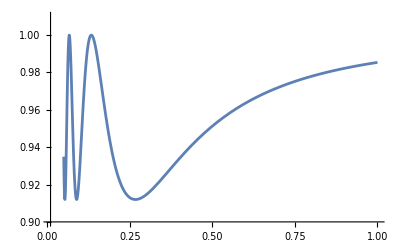

```mathematica
Plot[%58,{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9,10^10},{0.90,1.01}}]
```

```mathematica
Subscript[P, ee vacuum]=Limit[Subscript[P, ee],A->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1-4 Sin[(L m_31)/(4 Energy)]^2 s_13^2

```mathematica
ReplaceAll[Subscript[P, ee vacuum],{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[49.26 Degree], Subscript[c, 23]->Cos[49.26 Degree], α->(7.50/2.55) 10^-2, δ->3.4383}]
```

1-0.0880039 Sin[(4.19475×10^9)/Energy]^2

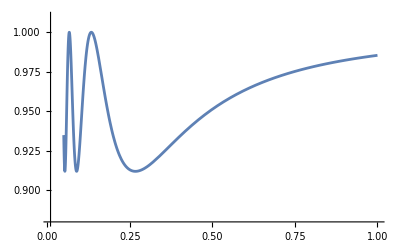

```mathematica
Plot[1-0.08800387853387907 Sin[(4.1947499999999995*^9)/Energy]^2,{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9,10^10},{0.88,1.01}}]
```

## P_eμ (2)

```mathematica
TrigReduce[%21]
```

```mathematica
PolynomialMod[%35,α (Subscript[s, 13])^2]
```

```mathematica
Normal[Series[Simplify[%36],{α,0,1},{Subscript[s, 13],0,3}]]
```

-1/((-1+A)^6 A^2)2 c_13^2 s_13^2 s_23^2 ((-1+A)^4 (-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) c_23^4-(-1+A)^4 c_23^2 ((-1+A) (A Cos[(L m_31)/(2 Energy)]-A Cos[((-1+A) L m_31)/(2 Energy)]+(-2+A) (-1+Cos[(A L m_31)/(2 Energy)]))-2 (-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) s_23^2)+(-1+A)^4 (-2 (-1+A)^2 Sin[(A L m_31)/(4 Energy)]^2+(-1+A) (-A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]-(-2+A) (-1+Cos[(A L m_31)/(2 Energy)])) s_23^2+(-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) s_23^4))+α (-1/((-1+A)^2 A^2)2 (1-A) c_12 c_13^2 c_23 s_12 s_13 s_23 (-2 Cos[δ]+2 A Cos[δ]+Cos[δ-(A L m_31)/(2 Energy)]-A Cos[δ-(A L m_31)/(2 Energy)]+Cos[δ+(A L m_31)/(2 Energy)]-A Cos[δ+(A L m_31)/(2 Energy)]-((-2+A) Cos[δ]-A Cos[δ+(L m_31)/(2 Energy)]+A Cos[δ-((-1+A) L m_31)/(2 Energy)]+Cos[δ-(A L m_31)/(2 Energy)]-A Cos[δ-(A L m_31)/(2 Energy)]+Cos[δ+(A L m_31)/(2 Energy)]) c_23^2+2 Cos[δ] s_23^2-A Cos[δ] s_23^2+A Cos[δ+(L m_31)/(2 Energy)] s_23^2-A Cos[δ-((-1+A) L m_31)/(2 Energy)] s_23^2-Cos[δ-(A L m_31)/(2 Energy)] s_23^2+A Cos[δ-(A L m_31)/(2 Energy)] s_23^2-Cos[δ+(A L m_31)/(2 Energy)] s_23^2)-1/A^2 2 (-1+A)^2 c_13^2 s_13^3 (1/(-1+A)^6 2 (1-A) (1-4 A+A^2) c_12 c_23 s_12 s_23 (-2 Cos[δ]+2 A Cos[δ]+Cos[δ-(A L m_31)/(2 Energy)]-A Cos[δ-(A L m_31)/(2 Energy)]+Cos[δ+(A L m_31)/(2 Energy)]-A Cos[δ+(A L m_31)/(2 Energy)]-((-2+A) Cos[δ]-A Cos[δ+(L m_31)/(2 Energy)]+A Cos[δ-((-1+A) L m_31)/(2 Energy)]+Cos[δ-(A L m_31)/(2 Energy)]-A Cos[δ-(A L m_31)/(2 Energy)]+Cos[δ+(A L m_31)/(2 Energy)]) c_23^2+2 Cos[δ] s_23^2-A Cos[δ] s_23^2+A Cos[δ+(L m_31)/(2 Energy)] s_23^2-A Cos[δ-((-1+A) L m_31)/(2 Energy)] s_23^2-Cos[δ-(A L m_31)/(2 Energy)] s_23^2+A Cos[δ-(A L m_31)/(2 Energy)] s_23^2-Cos[δ+(A L m_31)/(2 Energy)] s_23^2)-1/(2 (-1+A)^4 Energy)c_12 c_23 s_12 s_23 (A L Sin[δ-(A L m_31)/(2 Energy)] m_31-A^2 L Sin[δ-(A L m_31)/(2 Energy)] m_31-A L Sin[δ+(A L m_31)/(2 Energy)] m_31+A^2 L Sin[δ+(A L m_31)/(2 Energy)] m_31+A^2 L Sin[δ+(L m_31)/(2 Energy)] c_23^2 m_31-2 A^2 L Sin[δ-((-1+A) L m_31)/(2 Energy)] c_23^2 m_31-A L Sin[δ-(A L m_31)/(2 Energy)] c_23^2 m_31+A^2 L Sin[δ-(A L m_31)/(2 Energy)] c_23^2 m_31+A L Sin[δ+(A L m_31)/(2 Energy)] c_23^2 m_31+A^2 L Sin[δ+(L m_31)/(2 Energy)] m_31 s_23^2-2 A^2 L Sin[δ-((-1+A) L m_31)/(2 Energy)] m_31 s_23^2-A L Sin[δ-(A L m_31)/(2 Energy)] m_31 s_23^2+A^2 L Sin[δ-(A L m_31)/(2 Energy)] m_31 s_23^2+A L Sin[δ+(A L m_31)/(2 Energy)] m_31 s_23^2))-2 (-1+A)^2 c_13^2 s_13^2 (-1/((-1+A)^16 A^4)(-2 (-1+A)^8 A (1+A) c_12^2+2 (-1+A)^7 A (-1+2 A) s_12^2) s_23^2 ((-1+A)^4 (-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) c_23^4-(-1+A)^4 c_23^2 ((-1+A) (A Cos[(L m_31)/(2 Energy)]-A Cos[((-1+A) L m_31)/(2 Energy)]+(-2+A) (-1+Cos[(A L m_31)/(2 Energy)]))-2 (-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) s_23^2)+(-1+A)^4 (-2 (-1+A)^2 Sin[(A L m_31)/(4 Energy)]^2+(-1+A) (-A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]-(-2+A) (-1+Cos[(A L m_31)/(2 Energy)])) s_23^2+(-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) s_23^4))+1/((-1+A)^8 A^2)s_23^2 ((-1+A)^4 c_23^4 (((-1+A) A L Sin[(L m_31)/(2 Energy)] c_12^2 m_31)/(2 Energy)-(A L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2)/(2 Energy)+(L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)-(A L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy))-(-1+A)^4 c_23^2 ((-1+A) ((A L Sin[(L m_31)/(2 Energy)] c_12^2 m_31)/(2 Energy)+(A L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2)/(2 Energy)+((-2+A) L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy))-2 (((-1+A) A L Sin[(L m_31)/(2 Energy)] c_12^2 m_31)/(2 Energy)-(A L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2)/(2 Energy)+(L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)-(A L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)) s_23^2)+(-1+A)^4 (((-1+A)^2 L Cos[(A L m_31)/(4 Energy)] Sin[(A L m_31)/(4 Energy)] m_31 (c_12^2-s_12^2))/Energy+(-1+A) (-(A L Sin[(L m_31)/(2 Energy)] c_12^2 m_31)/(2 Energy)-(A L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2)/(2 Energy)-((-2+A) L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)) s_23^2+(((-1+A) A L Sin[(L m_31)/(2 Energy)] c_12^2 m_31)/(2 Energy)-(A L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2)/(2 Energy)+(L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)-(A L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)) s_23^4))))

```mathematica
PolynomialMod[%39,α (Subscript[s, 13])^2]
```

1/(-A^3 Energy+3 A^4 Energy-3 A^5 Energy+A^6 Energy)(-4 A Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23+12 A^2 Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23-12 A^3 Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23+4 A^4 Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23+2 A Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23-6 A^2 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23+6 A^3 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23-2 A^4 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23+2 A Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23-6 A^2 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23+6 A^3 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23-2 A^4 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23+4 A Energy α Cos[δ] c_12 c_13^2 c_23^3 s_12 s_13 s_23-10 A^2 Energy α Cos[δ] c_12 c_13^2 c_23^3 s_12 s_13 s_23+8 A^3 Energy α Cos[δ] c_12 c_13^2 c_23^3 s_12 s_13 s_23-2 A^4 Energy α Cos[δ] c_12 c_13^2 c_23^3 s_12 s_13 s_23+2 A^2 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-4 A^3 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+2 A^4 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-2 A^2 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+4 A^3 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-2 A^4 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-2 A Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+6 A^2 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-6 A^3 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+2 A^4 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-2 A Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+4 A^2 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-2 A^3 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-4 A Energy Sin[(A L m_31)/(4 Energy)]^2 c_13^2 s_13^2 s_23^2+12 A^2 Energy Sin[(A L m_31)/(4 Energy)]^2 c_13^2 s_13^2 s_23^2-12 A^3 Energy Sin[(A L m_31)/(4 Energy)]^2 c_13^2 s_13^2 s_23^2+4 A^4 Energy Sin[(A L m_31)/(4 Energy)]^2 c_13^2 s_13^2 s_23^2+4 A Energy c_13^2 c_23^2 s_13^2 s_23^2-10 A^2 Energy c_13^2 c_23^2 s_13^2 s_23^2+8 A^3 Energy c_13^2 c_23^2 s_13^2 s_23^2-2 A^4 Energy c_13^2 c_23^2 s_13^2 s_23^2+2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-2 A^4 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-4 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+10 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-8 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+2 A^4 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-2 A Energy c_13^2 c_23^4 s_13^2 s_23^2+4 A^2 Energy c_13^2 c_23^4 s_13^2 s_23^2-4 A^3 Energy c_13^2 c_23^4 s_13^2 s_23^2+2 A^4 Energy c_13^2 c_23^4 s_13^2 s_23^2-2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-2 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+2 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-4 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+2 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+4 A Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23^3-10 A^2 Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23^3+8 A^3 Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23^3-2 A^4 Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23^3+2 A^2 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-4 A^3 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+2 A^4 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-2 A^2 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+4 A^3 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-2 A^4 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-2 A Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+6 A^2 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-6 A^3 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+2 A^4 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-2 A Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+4 A^2 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-2 A^3 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+4 A Energy c_13^2 s_13^2 s_23^4-10 A^2 Energy c_13^2 s_13^2 s_23^4+8 A^3 Energy c_13^2 s_13^2 s_23^4-2 A^4 Energy c_13^2 s_13^2 s_23^4+2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^4-4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^4+2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^4-2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^4+4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^4-2 A^4 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^4-4 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^4+10 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^4-8 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^4+2 A^4 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^4-4 A Energy c_13^2 c_23^2 s_13^2 s_23^4+8 A^2 Energy c_13^2 c_23^2 s_13^2 s_23^4-8 A^3 Energy c_13^2 c_23^2 s_13^2 s_23^4+4 A^4 Energy c_13^2 c_23^2 s_13^2 s_23^4-4 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+8 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4-4 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+4 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4-4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+4 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4-8 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+4 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4-2 A Energy c_13^2 s_13^2 s_23^6+4 A^2 Energy c_13^2 s_13^2 s_23^6-4 A^3 Energy c_13^2 s_13^2 s_23^6+2 A^4 Energy c_13^2 s_13^2 s_23^6-2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^6+4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^6-2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^6+2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^6-2 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^6+2 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^6-4 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^6+2 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 s_13^2 s_23^6)

```mathematica
FullSimplify[%40,{Subscript[s, 12]^2+Subscript[c, 12]^2==1,Subscript[s, 23]^2+Subscript[c, 23]^2==1}]/.Subscript[c, 13]^2->1
```

(2 s_13 s_23 ((-1+A) α (Cos[δ]+Cos[δ+(L m_31)/(2 Energy)]-Cos[δ-((-1+A) L m_31)/(2 Energy)]-Cos[δ+(A L m_31)/(2 Energy)]) c_12 c_23 s_12+2 A Sin[((-1+A) L m_31)/(4 Energy)]^2 s_13 s_23))/((-1+A)^2 A)

```mathematica
Subscript[P, eμ]=Collect[(2 Subscript[s, 13] Subscript[s, 23] ((-1+A) α (Cos[δ]+Cos[δ+(L Subscript[m, 31])/(2 Energy)]-Cos[δ-((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[δ+(A L Subscript[m, 31])/(2 Energy)]) Subscript[c, 12] Subscript[c, 23] Subscript[s, 12]+2 A Sin[((-1+A) L Subscript[m, 31])/(4 Energy)]^2 Subscript[s, 13] Subscript[s, 23]))/((-1+A)^2 A),Subscript[s, 13]]
```

(2 α (Cos[δ]+Cos[δ+(L m_31)/(2 Energy)]-Cos[δ-((-1+A) L m_31)/(2 Energy)]-Cos[δ+(A L m_31)/(2 Energy)]) c_12 c_23 s_12 s_13 s_23)/((-1+A) A)+(4 Sin[((-1+A) L m_31)/(4 Energy)]^2 s_13^2 s_23^2)/(-1+A)^2

```mathematica
ReplaceAll[Subscript[P, eμ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

(2.52401×10^15 (0.00890308 (-1+8.89412×10^-17 Energy) (-2.15081×10^-7+Cos[3.4383+(8.27106×10^9)/Energy]-Cos[3.4383-(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy])+1.99662×10^-17 Energy Sin[(4.13553×10^9 (-1+8.89412×10^-17 Energy))/Energy]^2))/((-1+8.89412×10^-17 Energy)^2 Energy)

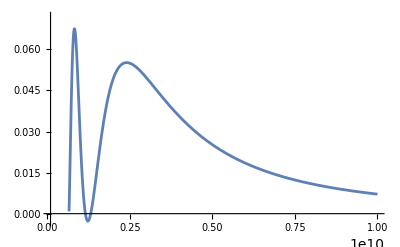

```mathematica
Plot[%43,{Energy,0.66×10^9,10^10},PlotRange->{{0.1 10^9,10^10},{-0.003,0.072}}]
```

## mencari P_eτ

```mathematica
Simplify[(Abs[S[[3,1]]])^2]
```

(Abs[((1-A) c_13 (-ⅇ^((ⅈ L α c_12^2 m_31)/(2 Energy)) ((-1+A)^2+(-1+A) α s_12^2+2 A s_13^2) (-((-1+A) (1+A+α s_12^2) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23))-(1-A) (A+s_13^2+s_12^2 (α-α s_13^2)) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23)+(-1+A) ⅇ^(-ⅈ δ) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2)+(-1+A) ⅇ^(-ⅈ δ) (α c_12 c_23 s_12-ⅇ^(ⅈ δ) (-1+α s_12^2) s_13 s_23) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)))+ⅇ^((ⅈ L m_31 (-1+A-A s_13^2))/(2 (-1+A) Energy)) (-((-1+A) α c_12^2)+(-1+A) (A+α s_12^2)+A s_13^2) ((-((-1+A) α c_12^2)-(-1+A) (A+α s_12^2)-A s_13^2) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23)-(1-A) (A+s_13^2+s_12^2 (α-α s_13^2)) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23)+(-1+A) ⅇ^(-ⅈ δ) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2)+(-1+A) ⅇ^(-ⅈ δ) (α c_12 c_23 s_12-ⅇ^(ⅈ δ) (-1+α s_12^2) s_13 s_23) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)))+ⅇ^((ⅈ L m_31 ((-1+A) (A+α s_12^2)+A s_13^2))/(2 (-1+A) Energy)) (1-A+(-1+A) α c_12^2+A s_13^2) ((1-A+(α-A α) c_12^2+A s_13^2) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23)-(1-A) (A+s_13^2+s_12^2 (α-α s_13^2)) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23)+(-1+A) ⅇ^(-ⅈ δ) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2)+(-1+A) ⅇ^(-ⅈ δ) (α c_12 c_23 s_12-ⅇ^(ⅈ δ) (-1+α s_12^2) s_13 s_23) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)))))/((1-A+(-1+A) α c_12^2+A s_13^2) (-((-1+A) α c_12^2)+(-1+A) (A+α s_12^2)+A s_13^2) ((-1+A)^2+(-1+A) α s_12^2+2 A s_13^2))])^2

```mathematica
TrigReduce[ComplexExpand[%54]]
```

```mathematica
Collect[%66,δ]
```

```mathematica
PolynomialMod[%55,α (Subscript[s, 13])^2]
```

```mathematica
Normal[Series[Simplify[%56],{α,0,1},{Subscript[s, 13],0,3}]]
```

-1/((-1+A)^6 A^2)2 c_13^2 s_13^2 ((-1+A)^4 (-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) c_23^6+(-1+A)^4 c_23^4 ((-1+A) (-A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]-(-2+A) (-1+Cos[(A L m_31)/(2 Energy)]))+2 (-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) s_23^2)+(-1+A)^4 c_23^2 (-2 (-1+A)^2 Sin[(A L m_31)/(4 Energy)]^2+(-1+A) (-A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]-(-2+A) (-1+Cos[(A L m_31)/(2 Energy)])) s_23^2+(-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) s_23^4))+α (-1/((-1+A)^6 A^2)2 c_13^2 s_13 (-(-1+A)^5 (-2 Cos[δ]+A Cos[δ]-A Cos[δ+(L m_31)/(2 Energy)]+A Cos[δ-((-1+A) L m_31)/(2 Energy)]+Cos[δ-(A L m_31)/(2 Energy)]-A Cos[δ-(A L m_31)/(2 Energy)]+Cos[δ+(A L m_31)/(2 Energy)]) c_12 c_23^3 s_12 s_23+(1-A) (-1+A)^4 c_12 c_23 s_12 s_23 (-4 (-1+A) Cos[δ] Sin[(A L m_31)/(4 Energy)]^2+((-2+A) Cos[δ]-A Cos[δ+(L m_31)/(2 Energy)]+A Cos[δ-((-1+A) L m_31)/(2 Energy)]+Cos[δ-(A L m_31)/(2 Energy)]-A Cos[δ-(A L m_31)/(2 Energy)]+Cos[δ+(A L m_31)/(2 Energy)]) s_23^2))-1/A^2 2 (-1+A)^2 c_13^2 s_13^3 (1/(-1+A)^10 2 (1-4 A+A^2) (-(-1+A)^5 (-2 Cos[δ]+A Cos[δ]-A Cos[δ+(L m_31)/(2 Energy)]+A Cos[δ-((-1+A) L m_31)/(2 Energy)]+Cos[δ-(A L m_31)/(2 Energy)]-A Cos[δ-(A L m_31)/(2 Energy)]+Cos[δ+(A L m_31)/(2 Energy)]) c_12 c_23^3 s_12 s_23+(1-A) (-1+A)^4 c_12 c_23 s_12 s_23 (-4 (-1+A) Cos[δ] Sin[(A L m_31)/(4 Energy)]^2+((-2+A) Cos[δ]-A Cos[δ+(L m_31)/(2 Energy)]+A Cos[δ-((-1+A) L m_31)/(2 Energy)]+Cos[δ-(A L m_31)/(2 Energy)]-A Cos[δ-(A L m_31)/(2 Energy)]+Cos[δ+(A L m_31)/(2 Energy)]) s_23^2))+1/(-1+A)^8(((-1+A)^4 c_12 c_23^3 (A^2 L Sin[δ+(L m_31)/(2 Energy)] m_31-2 A^2 L Sin[δ-((-1+A) L m_31)/(2 Energy)] m_31-A L Sin[δ-(A L m_31)/(2 Energy)] m_31+A^2 L Sin[δ-(A L m_31)/(2 Energy)] m_31+A L Sin[δ+(A L m_31)/(2 Energy)] m_31) s_12 s_23)/(2 Energy)+(1-A) (-1+A)^4 c_12 c_23 s_12 s_23 (-(2 A L Cos[δ] Cos[(A L m_31)/(4 Energy)] Sin[(A L m_31)/(4 Energy)] m_31)/Energy-((A^2 L Sin[δ+(L m_31)/(2 Energy)] m_31-2 A^2 L Sin[δ-((-1+A) L m_31)/(2 Energy)] m_31-A L Sin[δ-(A L m_31)/(2 Energy)] m_31+A^2 L Sin[δ-(A L m_31)/(2 Energy)] m_31+A L Sin[δ+(A L m_31)/(2 Energy)] m_31) s_23^2)/(2 (-1+A) Energy))))-2 (-1+A)^2 c_13^2 s_13^2 (-1/((-1+A)^16 A^4)(-2 (-1+A)^8 A (1+A) c_12^2+2 (-1+A)^7 A (-1+2 A) s_12^2) ((-1+A)^4 (-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) c_23^6+(-1+A)^4 c_23^4 ((-1+A) (-A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]-(-2+A) (-1+Cos[(A L m_31)/(2 Energy)]))+2 (-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) s_23^2)+(-1+A)^4 c_23^2 (-2 (-1+A)^2 Sin[(A L m_31)/(4 Energy)]^2+(-1+A) (-A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]-(-2+A) (-1+Cos[(A L m_31)/(2 Energy)])) s_23^2+(-1+A-A^2+(-1+A) A Cos[(L m_31)/(2 Energy)]+A Cos[((-1+A) L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]-A Cos[(A L m_31)/(2 Energy)]) s_23^4))+1/((-1+A)^8 A^2)((-1+A)^4 c_23^6 (((-1+A) A L Sin[(L m_31)/(2 Energy)] c_12^2 m_31)/(2 Energy)-(A L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2)/(2 Energy)+(L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)-(A L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy))+(-1+A)^4 c_23^4 ((-1+A) (-(A L Sin[(L m_31)/(2 Energy)] c_12^2 m_31)/(2 Energy)-(A L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2)/(2 Energy)-((-2+A) L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy))+2 (((-1+A) A L Sin[(L m_31)/(2 Energy)] c_12^2 m_31)/(2 Energy)-(A L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2)/(2 Energy)+(L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)-(A L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)) s_23^2)+(-1+A)^4 c_23^2 (((-1+A)^2 L Cos[(A L m_31)/(4 Energy)] Sin[(A L m_31)/(4 Energy)] m_31 (c_12^2-s_12^2))/Energy+(-1+A) (-(A L Sin[(L m_31)/(2 Energy)] c_12^2 m_31)/(2 Energy)-(A L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2)/(2 Energy)-((-2+A) L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)) s_23^2+(((-1+A) A L Sin[(L m_31)/(2 Energy)] c_12^2 m_31)/(2 Energy)-(A L Sin[((-1+A) L m_31)/(2 Energy)] m_31 s_12^2)/(2 Energy)+(L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)-(A L Sin[(A L m_31)/(2 Energy)] m_31 (c_12^2-s_12^2))/(2 Energy)) s_23^4))))

```mathematica
PolynomialMod[%58,α (Subscript[s, 13])^2]
```

1/(-A^3 Energy+3 A^4 Energy-3 A^5 Energy+A^6 Energy)(-4 A Energy Sin[(A L m_31)/(4 Energy)]^2 c_13^2 c_23^2 s_13^2+12 A^2 Energy Sin[(A L m_31)/(4 Energy)]^2 c_13^2 c_23^2 s_13^2-12 A^3 Energy Sin[(A L m_31)/(4 Energy)]^2 c_13^2 c_23^2 s_13^2+4 A^4 Energy Sin[(A L m_31)/(4 Energy)]^2 c_13^2 c_23^2 s_13^2+4 A Energy c_13^2 c_23^4 s_13^2-10 A^2 Energy c_13^2 c_23^4 s_13^2+8 A^3 Energy c_13^2 c_23^4 s_13^2-2 A^4 Energy c_13^2 c_23^4 s_13^2+2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2+2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2+4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-2 A^4 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-4 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2+10 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-8 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2+2 A^4 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-2 A Energy c_13^2 c_23^6 s_13^2+4 A^2 Energy c_13^2 c_23^6 s_13^2-4 A^3 Energy c_13^2 c_23^6 s_13^2+2 A^4 Energy c_13^2 c_23^6 s_13^2-2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2+4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2-2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2+2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2-2 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2+2 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2-4 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2+2 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2+8 A Energy α Cos[δ] Sin[(A L m_31)/(4 Energy)]^2 c_12 c_13^2 c_23 s_12 s_13 s_23-24 A^2 Energy α Cos[δ] Sin[(A L m_31)/(4 Energy)]^2 c_12 c_13^2 c_23 s_12 s_13 s_23+24 A^3 Energy α Cos[δ] Sin[(A L m_31)/(4 Energy)]^2 c_12 c_13^2 c_23 s_12 s_13 s_23-8 A^4 Energy α Cos[δ] Sin[(A L m_31)/(4 Energy)]^2 c_12 c_13^2 c_23 s_12 s_13 s_23-4 A Energy α Cos[δ] c_12 c_13^2 c_23^3 s_12 s_13 s_23+10 A^2 Energy α Cos[δ] c_12 c_13^2 c_23^3 s_12 s_13 s_23-8 A^3 Energy α Cos[δ] c_12 c_13^2 c_23^3 s_12 s_13 s_23+2 A^4 Energy α Cos[δ] c_12 c_13^2 c_23^3 s_12 s_13 s_23-2 A^2 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+4 A^3 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-2 A^4 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+2 A^2 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-4 A^3 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+2 A^4 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+2 A Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-6 A^2 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+6 A^3 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-2 A^4 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+2 A Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23-4 A^2 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+2 A^3 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23^3 s_12 s_13 s_23+4 A Energy c_13^2 c_23^2 s_13^2 s_23^2-10 A^2 Energy c_13^2 c_23^2 s_13^2 s_23^2+8 A^3 Energy c_13^2 c_23^2 s_13^2 s_23^2-2 A^4 Energy c_13^2 c_23^2 s_13^2 s_23^2+2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-2 A^4 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-4 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+10 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-8 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+2 A^4 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-4 A Energy c_13^2 c_23^4 s_13^2 s_23^2+8 A^2 Energy c_13^2 c_23^4 s_13^2 s_23^2-8 A^3 Energy c_13^2 c_23^4 s_13^2 s_23^2+4 A^4 Energy c_13^2 c_23^4 s_13^2 s_23^2-4 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+8 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-4 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+4 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+4 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-8 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+4 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-4 A Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23^3+10 A^2 Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23^3-8 A^3 Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23^3+2 A^4 Energy α Cos[δ] c_12 c_13^2 c_23 s_12 s_13 s_23^3-2 A^2 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+4 A^3 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-2 A^4 Energy α Cos[δ+(L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+2 A^2 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-4 A^3 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+2 A^4 Energy α Cos[δ-((-1+A) L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+2 A Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-6 A^2 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+6 A^3 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-2 A^4 Energy α Cos[δ-(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+2 A Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-4 A^2 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3+2 A^3 Energy α Cos[δ+(A L m_31)/(2 Energy)] c_12 c_13^2 c_23 s_12 s_13 s_23^3-2 A Energy c_13^2 c_23^2 s_13^2 s_23^4+4 A^2 Energy c_13^2 c_23^2 s_13^2 s_23^4-4 A^3 Energy c_13^2 c_23^2 s_13^2 s_23^4+2 A^4 Energy c_13^2 c_23^2 s_13^2 s_23^4-2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4-2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4-2 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+2 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4-4 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+2 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4)

```mathematica
FullSimplify[%63,{Subscript[s, 12]^2+Subscript[c, 12]^2==1,Subscript[s, 23]^2+Subscript[c, 23]^2==1}]/.Subscript[c, 13]^2->1
```

(2 s_13 (-((-1+A) α (Cos[δ]+Cos[δ+(L m_31)/(2 Energy)]-Cos[δ-((-1+A) L m_31)/(2 Energy)]-Cos[δ+(A L m_31)/(2 Energy)]) c_12 c_23 s_12 s_23)+A (-1+Cos[((-1+A) L m_31)/(2 Energy)]) s_13 (-1+s_23^2)))/((-1+A)^2 A)

```mathematica
Subscript[P, eτ]=Collect[(2 Subscript[s, 13] (-((-1+A) α (Cos[δ]+Cos[δ+(L Subscript[m, 31])/(2 Energy)]-Cos[δ-((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[δ+(A L Subscript[m, 31])/(2 Energy)]) Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 23])+A (-1+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]) Subscript[s, 13] (-1+Subscript[s, 23]^2)))/((-1+A)^2 A),Subscript[s, 13]]
```

(2 (1-A) α (Cos[δ]+Cos[δ+(L m_31)/(2 Energy)]-Cos[δ-((-1+A) L m_31)/(2 Energy)]-Cos[δ+(A L m_31)/(2 Energy)]) c_12 c_23 s_12 s_13 s_23)/((-1+A)^2 A)+(2 (-1+Cos[((-1+A) L m_31)/(2 Energy)]) s_13^2 (-1+s_23^2))/(-1+A)^2

```mathematica
ReplaceAll[%64,{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[49.26 Degree], Subscript[c, 23]->Cos[49.26 Degree], α->(7.50/2.55) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

(3.3354×10^15 (-0.00677045 (-1+8.89412×10^-17 Energy) (-2.18161×10^-7+Cos[3.4383+(8.3895×10^9)/Energy]-Cos[3.4383-(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy])-5.61894×10^-18 Energy (-1+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy])))/((-1+8.89412×10^-17 Energy)^2 Energy)

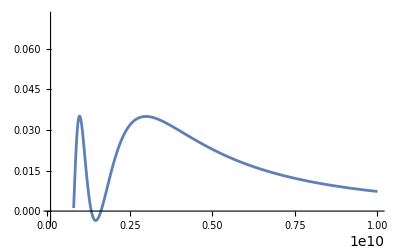

```mathematica
Plot[%65,{Energy,0.8 10^9,10^10},PlotRange->{{0.1 10^9,10^10},{-0.004,0.072}}]
```

```mathematica
PolynomialMod[Out[31],α Subscript[s, 13]]
```

(-2 A Energy c_13^2 c_23^2 s_13^2+6 A^2 Energy c_13^2 c_23^2 s_13^2-6 A^3 Energy c_13^2 c_23^2 s_13^2+2 A^4 Energy c_13^2 c_23^2 s_13^2+2 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2-6 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2+6 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2-2 A^4 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2+4 A Energy c_13^2 c_23^4 s_13^2-10 A^2 Energy c_13^2 c_23^4 s_13^2+8 A^3 Energy c_13^2 c_23^4 s_13^2-2 A^4 Energy c_13^2 c_23^4 s_13^2+2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2+2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2+4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-2 A^4 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-4 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2+10 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-8 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2+2 A^4 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2-2 A Energy c_13^2 c_23^6 s_13^2+4 A^2 Energy c_13^2 c_23^6 s_13^2-4 A^3 Energy c_13^2 c_23^6 s_13^2+2 A^4 Energy c_13^2 c_23^6 s_13^2-2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2+4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2-2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2+2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2-2 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2+2 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2-4 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2+2 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^6 s_13^2+4 A Energy c_13^2 c_23^2 s_13^2 s_23^2-10 A^2 Energy c_13^2 c_23^2 s_13^2 s_23^2+8 A^3 Energy c_13^2 c_23^2 s_13^2 s_23^2-2 A^4 Energy c_13^2 c_23^2 s_13^2 s_23^2+2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-2 A^4 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-4 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+10 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-8 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2+2 A^4 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^2-4 A Energy c_13^2 c_23^4 s_13^2 s_23^2+8 A^2 Energy c_13^2 c_23^4 s_13^2 s_23^2-8 A^3 Energy c_13^2 c_23^4 s_13^2 s_23^2+4 A^4 Energy c_13^2 c_23^4 s_13^2 s_23^2-4 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+8 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-4 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+4 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-4 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+4 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-8 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2+4 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^4 s_13^2 s_23^2-2 A Energy c_13^2 c_23^2 s_13^2 s_23^4+4 A^2 Energy c_13^2 c_23^2 s_13^2 s_23^4-4 A^3 Energy c_13^2 c_23^2 s_13^2 s_23^4+2 A^4 Energy c_13^2 c_23^2 s_13^2 s_23^4-2 A^2 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+4 A^3 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4-2 A^4 Energy Cos[(L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+2 A^2 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4-2 A^3 Energy Cos[((-1+A) L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+2 A Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4-4 A^2 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4+2 A^3 Energy Cos[(A L m_31)/(2 Energy)] c_13^2 c_23^2 s_13^2 s_23^4)/(-A^3 Energy+3 A^4 Energy-3 A^5 Energy+A^6 Energy)

```mathematica
Subscript[P, eτ]=FullSimplify[Out[32],{Subscript[s, 12]^2+Subscript[c, 12]^2==1,Subscript[s, 23]^2+Subscript[c, 23]^2==1}]/.Subscript[c, 13]^2->1
```

(2 (-1+Cos[((-1+A) L m_31)/(2 Energy)]) s_13^2 (-1+s_23^2))/(-1+A)^2

```mathematica
ReplaceAll[Subscript[P, eτ],{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[49.26 Degree], Subscript[c, 23]->Cos[49.26 Degree], α->(7.50/2.55) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

-(0.0187414 (-1+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]))/((-1+8.89412×10^-17 Energy)^2)

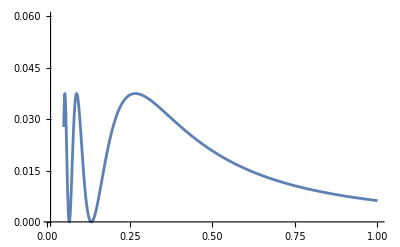

```mathematica
Plot[-(0.018741424034597515 (-1+Cos[(8.389499999999999*^9 (-1+8.894117647058826*^-17 Energy))/Energy]))/((-1+8.894117647058826*^-17 Energy)^2),{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9,10^10},{0,0.06}}]
```

```mathematica
Subscript[P, eτ vacuum]=Limit[Subscript[P, eτ],A->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

2 (-1+Cos[(L m_31)/(2 Energy)]) s_13^2 (-1+s_23^2)

```mathematica
ReplaceAll[Subscript[P, eτ vacuum],{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[49.26 Degree], Subscript[c, 23]->Cos[49.26 Degree], α->(7.50/2.55) 10^-2, δ->3.4383}]
```

-0.0187414 (-1+Cos[(8.3895×10^9)/Energy])

```mathematica
Plot[-0.018741424034597515 (-1+Cos[(8.389499999999999*^9)/Energy]),{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9,10^10},{0,0.06}}]
```

-Graphics-

## mencari P_μμ

```mathematica
Simplify[(Abs[S[[2,2]]])^2]
```

(Abs[(ⅇ^((ⅈ L α c_12^2 m_31)/(2 Energy)) ((-1+A)^2+(-1+A) α s_12^2+2 A s_13^2) ((1-A+A s_13^2) ((-1+A) (A+α s_12^2)+A s_13^2)-(-1+A)^2 c_13^2 (α c_12 c_23 s_12+ⅇ^(-ⅈ δ) (1-α s_12^2) s_13 s_23) (α c_12 c_23 s_12-ⅇ^(ⅈ δ) (-1+α s_12^2) s_13 s_23)+(-1+A)^2 ⅇ^(-ⅈ δ) (1+A+α s_12^2) (ⅇ^(ⅈ δ) α c_12^2 c_23^2-(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) (1+(-1+α s_12^2) s_13^2) s_23^2)-(-1+A)^2 ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23^2-(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) (1+(-1+α s_12^2) s_13^2) s_23^2)^2+(-1+A)^2 ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)) (-ⅇ^(ⅈ δ) α c_12^2 c_23 s_23+ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23-α c_12 s_12 s_13 (c_23^2-ⅇ^(2 ⅈ δ) s_23^2)))-(1-A) ⅇ^((ⅈ L m_31 (-1+A-A s_13^2))/(2 (-1+A) Energy)) (-((-1+A) α c_12^2)+(-1+A) (A+α s_12^2)+A s_13^2) (α c_12^2 ((-1+A) (A+α s_12^2)+A s_13^2)-(1-A) c_13^2 (α c_12 c_23 s_12+ⅇ^(-ⅈ δ) (1-α s_12^2) s_13 s_23) (α c_12 c_23 s_12-ⅇ^(ⅈ δ) (-1+α s_12^2) s_13 s_23)+ⅇ^(-ⅈ δ) ((-1+A) α c_12^2+(-1+A) α s_12^2+A (-1+A+s_13^2)) (-ⅇ^(ⅈ δ) α c_12^2 c_23^2+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23-ⅇ^(ⅈ δ) (1+(-1+α s_12^2) s_13^2) s_23^2)+(-1+A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23^2-(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) (1+(-1+α s_12^2) s_13^2) s_23^2)^2-(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (c_23^2-ⅇ^(2 ⅈ δ) s_23^2)))+(1-A) ⅇ^((ⅈ L m_31 ((-1+A) (A+α s_12^2)+A s_13^2))/(2 (-1+A) Energy)) (1-A+(-1+A) α c_12^2+A s_13^2) (α c_12^2 (1-A+A s_13^2)+(1-A) c_13^2 (α c_12 c_23 s_12+ⅇ^(-ⅈ δ) (1-α s_12^2) s_13 s_23) (α c_12 c_23 s_12-ⅇ^(ⅈ δ) (-1+α s_12^2) s_13 s_23)+ⅇ^(-ⅈ δ) (-1+A+(-1+A) α c_12^2-A s_13^2) (ⅇ^(ⅈ δ) α c_12^2 c_23^2-(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) (1+(-1+α s_12^2) s_13^2) s_23^2)+(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23^2-(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) (1+(-1+α s_12^2) s_13^2) s_23^2)^2+(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (c_23^2-ⅇ^(2 ⅈ δ) s_23^2))))/((1-A+(-1+A) α c_12^2+A s_13^2) (-((-1+A) α c_12^2)+(-1+A) (A+α s_12^2)+A s_13^2) ((-1+A)^2+(-1+A) α s_12^2+2 A s_13^2))])^2

```mathematica
TrigReduce[ComplexExpand[%28]]
```

```mathematica
PolynomialMod[%29,α (Subscript[s, 13])^2]
```

```mathematica
Normal[Series[%30,{α,0,1},{Subscript[s, 13],0,3}]]
```

```mathematica
TrigReduce[%31]
```

```mathematica
PolynomialMod[%33,α (Subscript[s, 13])^2]
```

```mathematica
TrigReduce[%34]
```

```mathematica
FullSimplify[Out[36],{Subscript[s, 12]^2+Subscript[c, 12]^2==1,Subscript[s, 23]^2+Subscript[c, 23]^2==1}]/.Subscript[c, 13]^2->1
```

1+1/((-1+A)^2 A Energy)s_23 (-4 (-1+A) Energy α Cos[δ] c_12 c_23 s_12 s_13 (1-A+A Cos[(L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]+2 Sin[(L m_31)/(4 Energy)] ((-1+2 A) Sin[(L m_31)/(4 Energy)]+Sin[((1-2 A) L m_31)/(4 Energy)]) s_23^2+2 (-1+A) A Sin[(L m_31)/(4 Energy)]^2 (-1+2 s_23^2))+s_23 ((-1+A) A L Sin[(L m_31)/(2 Energy)] m_31 ((-1+A) α (-1+s_12^2)-A s_13^2) (-1+s_23^2)+2 Energy (2 (-1+A)^2 A Sin[(L m_31)/(4 Energy)]^2 (-1+s_23^2)+s_13^2 (-(-1+A)^2+(-2+A) A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1+2 (-2+A) A+(-1-2 (-2+A) A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2+(-1+A) (-1+A-A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2)))))

```mathematica
Subscript[P, μμ]=Collect[1+1/((-1+A)^2 A Energy)Subscript[s, 23] (-4 (-1+A) Energy α Cos[δ] Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] (1-A+A Cos[(L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)]+2 Sin[(L Subscript[m, 31])/(4 Energy)] ((-1+2 A) Sin[(L Subscript[m, 31])/(4 Energy)]+Sin[((1-2 A) L Subscript[m, 31])/(4 Energy)]) Subscript[s, 23]^2+2 (-1+A) A Sin[(L Subscript[m, 31])/(4 Energy)]^2 (-1+2 Subscript[s, 23]^2))+Subscript[s, 23] ((-1+A) A L Sin[(L Subscript[m, 31])/(2 Energy)] Subscript[m, 31] ((-1+A) α (-1+Subscript[s, 12]^2)-A Subscript[s, 13]^2) (-1+Subscript[s, 23]^2)+2 Energy (2 (-1+A)^2 A Sin[(L Subscript[m, 31])/(4 Energy)]^2 (-1+Subscript[s, 23]^2)+Subscript[s, 13]^2 (-(-1+A)^2+(-2+A) A Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[(A L Subscript[m, 31])/(2 Energy)]+(1+2 (-2+A) A+(-1-2 (-2+A) A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 23]^2+(-1+A) (-1+A-A Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[(A L Subscript[m, 31])/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 23]^2))))),Subscript[s, 13]]
```

1+4 Sin[(L m_31)/(4 Energy)]^2 s_23^2 (-1+s_23^2)+(L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) s_23^2 (-1+s_23^2))/Energy-(4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (1-A+A Cos[(L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]+2 Sin[(L m_31)/(4 Energy)] ((-1+2 A) Sin[(L m_31)/(4 Energy)]+Sin[((1-2 A) L m_31)/(4 Energy)]) s_23^2+2 (-1+A) A Sin[(L m_31)/(4 Energy)]^2 (-1+2 s_23^2)))/((-1+A) A)+s_13^2 (-(A L Sin[(L m_31)/(2 Energy)] m_31 s_23^2 (-1+s_23^2))/((-1+A) Energy)+1/((-1+A)^2 A)2 s_23^2 (-(-1+A)^2+(-2+A) A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1+2 (-2+A) A+(-1-2 (-2+A) A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2+(-1+A) (-1+A-A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2)))

```mathematica
ReplaceAll[%37,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

1+1/((-1+8.89412×10^-17 Energy)^2 Energy^2)8.49835×10^15 (0.755853 (2 Energy (0.0220522 (1.-(-1+8.89412×10^-17 Energy)^2+8.89412×10^-17 (-2+8.89412×10^-17 Energy) Energy Cos[(8.27106×10^9)/Energy]+0.571314 (2.70561×10^-13+1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy+(-1-1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy])+(-1+8.89412×10^-17 Energy) (-2.70561×10^-13+8.89412×10^-17 Energy-8.89412×10^-17 Energy Cos[(8.27106×10^9)/Energy]+0.571314 (2.70561×10^-13-1.77882×10^-16 Energy+(-1+1.77882×10^-16 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy])))-7.62556×10^-17 (-1+8.89412×10^-17 Energy)^2 Energy Sin[(4.13553×10^9)/Energy]^2)-6.30715×10^-7 (-0.02042 (-1+8.89412×10^-17 Energy)-1.96135×10^-18 Energy) (-1+8.89412×10^-17 Energy) Energy Sin[(8.27106×10^9)/Energy])+0.00505734 (-1+8.89412×10^-17 Energy) Energy (2.70561×10^-13-8.89412×10^-17 Energy+8.89412×10^-17 Energy Cos[(8.27106×10^9)/Energy]+2.53712×10^-17 (-1+8.89412×10^-17 Energy) Energy Sin[(4.13553×10^9)/Energy]^2+1.14263 Sin[(4.13553×10^9)/Energy] ((-1+1.77882×10^-16 Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (1-1.77882×10^-16 Energy))/Energy])))

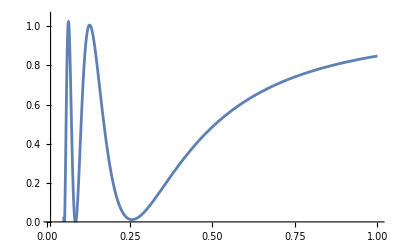

```mathematica
Plot[%38,{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.05}}]
```

```mathematica
Subscript[P, μμ]=1+1/((-1+A)^2 A Energy)Subscript[s, 23]^2 ((-1+A) A L Sin[(L Subscript[m, 31])/(2 Energy)] Subscript[m, 31] ((-1+A) α (-1+Subscript[s, 12]^2)-A Subscript[s, 13]^2) (-1+Subscript[s, 23]^2)+2 Energy (2 (-1+A)^2 A Sin[(L Subscript[m, 31])/(4 Energy)]^2 (-1+Subscript[s, 23]^2)+Subscript[s, 13]^2 (-(-1+A)^2+(-2+A) A Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[(A L Subscript[m, 31])/(2 Energy)]+(1+2 (-2+A) A+(-1-2 (-2+A) A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 23]^2+(-1+A) (-1+A-A Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[(A L Subscript[m, 31])/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 23]^2))))
```

1+1/((-1+A)^2 A Energy)s_23^2 ((-1+A) A L Sin[(L m_31)/(2 Energy)] m_31 ((-1+A) α (-1+s_12^2)-A s_13^2) (-1+s_23^2)+2 Energy (2 (-1+A)^2 A Sin[(L m_31)/(4 Energy)]^2 (-1+s_23^2)+s_13^2 (-(-1+A)^2+(-2+A) A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1+2 (-2+A) A+(-1-2 (-2+A) A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2+(-1+A) (-1+A-A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2))))

```mathematica
ReplaceAll[Subscript[P, μμ],{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[49.26 Degree], Subscript[c, 23]->Cos[49.26 Degree], α->(7.50/2.55) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

1+1/((-1+8.89412×10^-17 Energy)^2 Energy^2)6.45457×10^15 (2 Energy (0.022001 (1.-(-1+8.89412×10^-17 Energy)^2+8.89412×10^-17 (-2+8.89412×10^-17 Energy) Energy Cos[(8.3895×10^9)/Energy]+0.574077 (2.78333×10^-13+1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy+(-1-1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy) Cos[(8.3895×10^9)/Energy]+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy])+(-1+8.89412×10^-17 Energy) (-2.78333×10^-13+8.89412×10^-17 Energy-8.89412×10^-17 Energy Cos[(8.3895×10^9)/Energy]+0.574077 (2.78333×10^-13-1.77882×10^-16 Energy+(-1+1.77882×10^-16 Energy) Cos[(8.3895×10^9)/Energy]+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy])))-7.57641×10^-17 (-1+8.89412×10^-17 Energy)^2 Energy Sin[(4.19475×10^9)/Energy]^2)-6.35623×10^-7 (-0.0200717 (-1+8.89412×10^-17 Energy)-1.95679×10^-18 Energy) (-1+8.89412×10^-17 Energy) Energy Sin[(8.3895×10^9)/Energy])

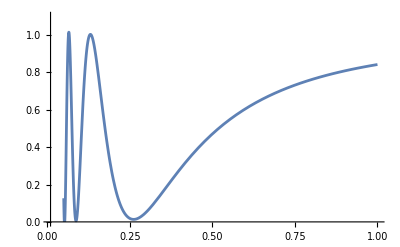

```mathematica
Plot[%27,{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.05}}]
```

```mathematica
Subscript[P, μμ vacuum]=Limit[Subscript[P, μμ],A->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1+(s_23^2 (L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) (-1+s_23^2)-4 Energy Sin[(L m_31)/(4 Energy)]^2 (1-s_23^2+s_13^2 (-1+2 s_23^2))))/Energy

```mathematica
ReplaceAll[Subscript[P, μμ vacuum],{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[49.26 Degree], Subscript[c, 23]->Cos[49.26 Degree], α->(7.50/2.55) 10^-2, δ->3.4383}]
```

1+(0.574077 (-1.71673 Energy Sin[(4.19475×10^9)/Energy]^2+1.43444×10^8 Sin[(8.3895×10^9)/Energy]))/Energy

```mathematica
Plot[1+(0.574077316890469 (-1.716728914833613 Energy Sin[(4.1947499999999995*^9)/Energy]^2+1.434436665829252*^8 Sin[(8.389499999999999*^9)/Energy]))/Energy,{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

-Graphics-

## mencari P_μτ

```mathematica
Simplify[(Abs[S[[3,2]]])^2]
```

(Abs[((1-A) (-ⅇ^((ⅈ L α c_12^2 m_31)/(2 Energy)) ((-1+A)^2+(-1+A) α s_12^2+2 A s_13^2) ((1-A) c_13^2 (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23) (α c_12 c_23 s_12+ⅇ^(-ⅈ δ) (1-α s_12^2) s_13 s_23)+(-1+A) ⅇ^(-ⅈ δ) (1+A+α s_12^2) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2))+(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2))+(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23^2-(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) (1+(-1+α s_12^2) s_13^2) s_23^2) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)))+ⅇ^((ⅈ L m_31 ((-1+A) (A+α s_12^2)+A s_13^2))/(2 (-1+A) Energy)) (1-A+(-1+A) α c_12^2+A s_13^2) ((1-A) c_13^2 (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23) (α c_12 c_23 s_12+ⅇ^(-ⅈ δ) (1-α s_12^2) s_13 s_23)+ⅇ^(-ⅈ δ) (-1+A+(-1+A) α c_12^2-A s_13^2) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2))+(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2))+(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23^2-(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) (1+(-1+α s_12^2) s_13^2) s_23^2) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)))+ⅇ^((ⅈ L m_31 (-1+A-A s_13^2))/(2 (-1+A) Energy)) (-((-1+A) α c_12^2)+(-1+A) (A+α s_12^2)+A s_13^2) ((1-A) c_13^2 (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23) (α c_12 c_23 s_12+ⅇ^(-ⅈ δ) (1-α s_12^2) s_13 s_23)+ⅇ^(-ⅈ δ) ((-1+A) α c_12^2+(-1+A) α s_12^2+A (-1+A+s_13^2)) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2))+(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2))+(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23^2-(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) (1+(-1+α s_12^2) s_13^2) s_23^2) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)))))/((1-A+(-1+A) α c_12^2+A s_13^2) (-((-1+A) α c_12^2)+(-1+A) (A+α s_12^2)+A s_13^2) ((-1+A)^2+(-1+A) α s_12^2+2 A s_13^2))])^2

```mathematica
TrigReduce[ComplexExpand[%21]]
```

```mathematica
PolynomialMod[Out[22],α (Subscript[s, 13])^2]
```

```mathematica
Normal[Series[%23,{α,0,1},{Subscript[s, 13],0,2}]]
```

```mathematica
TrigReduce[%24]
```

```mathematica
PolynomialMod[%25,α (Subscript[s, 13])^2]
```

```mathematica
Subscript[P, μτ]=FullSimplify[%26,{Subscript[s, 12]^2+Subscript[c, 12]^2==1,Subscript[s, 23]^2+Subscript[c, 23]^2==1}]/.Subscript[c, 13]^2->1
```

-1/((-1+A)^2 A Energy)s_23 (-((-4 (-1+A)^2 A Energy Sin[(L m_31)/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)])+Cos[(A L m_31)/(2 Energy)]) s_13^2-(-1+A) A L Sin[(L m_31)/(2 Energy)] m_31 ((-1+A) α (-1+s_12^2)-A s_13^2)) s_23 (-1+s_23^2))+4 (-1+A) Energy α Sin[(L m_31)/(4 Energy)] c_12 c_23 s_12 s_13 ((Cos[(L m_31)/(4 Energy)]-Cos[((-1+2 A) L m_31)/(4 Energy)]) Sin[δ]+Cos[δ] ((1-2 A-2 (-1+A) A) Sin[(L m_31)/(4 Energy)]+Sin[((-1+2 A) L m_31)/(4 Energy)]) (-1+2 s_23^2)))

```mathematica
Subscript[P, μτ]=Collect[-1/((-1+A)^2 A Energy)Subscript[s, 23] (-((-4 (-1+A)^2 A Energy Sin[(L Subscript[m, 31])/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L Subscript[m, 31])/(2 Energy)]-Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)])+Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 13]^2-(-1+A) A L Sin[(L Subscript[m, 31])/(2 Energy)] Subscript[m, 31] ((-1+A) α (-1+Subscript[s, 12]^2)-A Subscript[s, 13]^2)) Subscript[s, 23] (-1+Subscript[s, 23]^2))+4 (-1+A) Energy α Sin[(L Subscript[m, 31])/(4 Energy)] Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] ((Cos[(L Subscript[m, 31])/(4 Energy)]-Cos[((-1+2 A) L Subscript[m, 31])/(4 Energy)]) Sin[δ]+Cos[δ] ((1-2 A-2 (-1+A) A) Sin[(L Subscript[m, 31])/(4 Energy)]+Sin[((-1+2 A) L Subscript[m, 31])/(4 Energy)]) (-1+2 Subscript[s, 23]^2))),Subscript[s, 13]]
```

-1/((-1+A)^2 A Energy)s_13^2 s_23 (-2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)])+Cos[(A L m_31)/(2 Energy)]) s_23 (-1+s_23^2)+(1-A) A^2 L Sin[(L m_31)/(2 Energy)] m_31 s_23 (-1+s_23^2))-(s_23 (4 (-1+A)^2 A Energy Sin[(L m_31)/(4 Energy)]^2 s_23 (-1+s_23^2)-(1-A) (-1+A) A L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) s_23 (-1+s_23^2)))/((-1+A)^2 A Energy)-(4 α Sin[(L m_31)/(4 Energy)] c_12 c_23 s_12 s_13 s_23 ((Cos[(L m_31)/(4 Energy)]-Cos[((-1+2 A) L m_31)/(4 Energy)]) Sin[δ]+Cos[δ] ((1-2 A-2 (-1+A) A) Sin[(L m_31)/(4 Energy)]+Sin[((-1+2 A) L m_31)/(4 Energy)]) (-1+2 s_23^2)))/((-1+A) A)

```mathematica
ReplaceAll[%27,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

-1/((-1+8.89412×10^-17 Energy)^2 Energy^2)8.49835×10^15 (0.324023 (0.0441044 Energy (-2.70561×10^-13-1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy+(1+1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy]-(-1+8.89412×10^-17 Energy) (2.70561×10^-13-1.77882×10^-16 Energy+(-1+1.77882×10^-16 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy]))-3.55765×10^-16 (-1+8.89412×10^-17 Energy)^2 Energy^2 Sin[(4.13553×10^9)/Energy]^2-1.47128×10^-6 (-0.02042 (-1+8.89412×10^-17 Energy)-1.96135×10^-18 Energy) (-1+8.89412×10^-17 Energy) Energy Sin[(8.27106×10^9)/Energy])+0.00528842 (-1+8.89412×10^-17 Energy) Energy Sin[(4.13553×10^9)/Energy] (-0.292373 (Cos[(4.13553×10^9)/Energy]-Cos[(4.13553×10^9 (-1+1.77882×10^-16 Energy))/Energy])-0.136397 ((1-1.77882×10^-16 Energy-1.77882×10^-16 (-1+8.89412×10^-17 Energy) Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (-1+1.77882×10^-16 Energy))/Energy])))

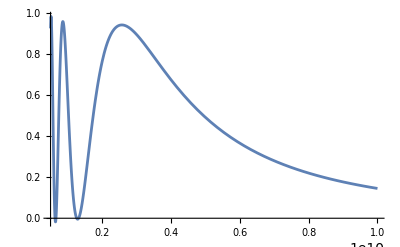

```mathematica
Plot[%29,{Energy,0.5 10^9,10^10}]
```

```mathematica
Subscript[P, μτ]=1/((-1+A)^2 A Energy)(-4 (-1+A)^2 A Energy Sin[(L Subscript[m, 31])/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L Subscript[m, 31])/(2 Energy)]-Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)])+Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 13]^2-(-1+A) A L Sin[(L Subscript[m, 31])/(2 Energy)] Subscript[m, 31] ((-1+A) α (-1+Subscript[s, 12]^2)-A Subscript[s, 13]^2)) Subscript[s, 23]^2 (-1+Subscript[s, 23]^2)
```

1/((-1+A)^2 A Energy)(-4 (-1+A)^2 A Energy Sin[(L m_31)/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)])+Cos[(A L m_31)/(2 Energy)]) s_13^2-(-1+A) A L Sin[(L m_31)/(2 Energy)] m_31 ((-1+A) α (-1+s_12^2)-A s_13^2)) s_23^2 (-1+s_23^2)

```mathematica
ReplaceAll[Subscript[P, μτ],{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[49.26 Degree], Subscript[c, 23]->Cos[49.26 Degree], α->(7.50/2.55) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

-1/((-1+8.89412×10^-17 Energy)^2 Energy^2)2.74915×10^15 (0.0440019 Energy (-2.78333×10^-13-1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy+(1+1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy) Cos[(8.3895×10^9)/Energy]-Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]-(-1+8.89412×10^-17 Energy) (2.78333×10^-13-1.77882×10^-16 Energy+(-1+1.77882×10^-16 Energy) Cos[(8.3895×10^9)/Energy]+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]))-3.55765×10^-16 (-1+8.89412×10^-17 Energy)^2 Energy^2 Sin[(4.19475×10^9)/Energy]^2-1.49234×10^-6 (-0.0200717 (-1+8.89412×10^-17 Energy)-1.95679×10^-18 Energy) (-1+8.89412×10^-17 Energy) Energy Sin[(8.3895×10^9)/Energy])

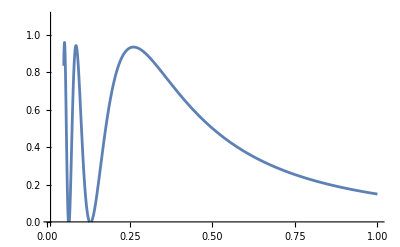

```mathematica
Plot[%44,{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

```mathematica
Subscript[P, μτ vacuum]=Limit[Subscript[P, μτ],A->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

((-L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2)+4 Energy Sin[(L m_31)/(4 Energy)]^2 (-1+2 s_13^2)) s_23^2 (-1+s_23^2))/Energy

```mathematica
ReplaceAll[Subscript[P, μτ vacuum],{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[49.26 Degree], Subscript[c, 23]->Cos[49.26 Degree], α->(7.50/2.55) 10^-2, δ->3.4383}]
```

-(0.244513 (-3.82399 Energy Sin[(4.19475×10^9)/Energy]^2+3.36783×10^8 Sin[(8.3895×10^9)/Energy]))/Energy

```mathematica
Plot[-(0.24451255112230902 (-3.823992242932242 Energy Sin[(4.1947499999999995*^9)/Energy]^2+3.3678334653530765*^8 Sin[(8.389499999999999*^9)/Energy]))/Energy,{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

-Graphics-

## mencari P_ττ

```mathematica
Subscript[P, μτ_]=Simplify[(Abs[S[[3,3]]])^2]
```

(Abs[(ⅇ^((ⅈ L α c_12^2 m_31)/(2 Energy)) ((-1+A)^2+(-1+A) α s_12^2+2 A s_13^2) ((1-A+A s_13^2) ((-1+A) (A+α s_12^2)+A s_13^2)+(-1+A)^2 c_13^2 (ⅇ^(-ⅈ δ) c_23 (1-α s_12^2) s_13-α c_12 s_12 s_23) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23)+(-1+A)^2 ⅇ^(-ⅈ δ) (1+A+α s_12^2) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2)-(-1+A)^2 ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2)^2+(-1+A)^2 ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)) (-ⅇ^(ⅈ δ) α c_12^2 c_23 s_23+ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23-α c_12 s_12 s_13 (c_23^2-ⅇ^(2 ⅈ δ) s_23^2)))-(1-A) ⅇ^((ⅈ L m_31 (-1+A-A s_13^2))/(2 (-1+A) Energy)) (-((-1+A) α c_12^2)+(-1+A) (A+α s_12^2)+A s_13^2) (α c_12^2 ((-1+A) (A+α s_12^2)+A s_13^2)+(1-A) c_13^2 (ⅇ^(-ⅈ δ) c_23 (1-α s_12^2) s_13-α c_12 s_12 s_23) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23)-ⅇ^(-ⅈ δ) ((-1+A) α c_12^2+(-1+A) α s_12^2+A (-1+A+s_13^2)) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2)+(-1+A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2)^2-(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (c_23^2-ⅇ^(2 ⅈ δ) s_23^2)))+(1-A) ⅇ^((ⅈ L m_31 ((-1+A) (A+α s_12^2)+A s_13^2))/(2 (-1+A) Energy)) (1-A+(-1+A) α c_12^2+A s_13^2) (α c_12^2 (1-A+A s_13^2)-(1-A) c_13^2 (ⅇ^(-ⅈ δ) c_23 (1-α s_12^2) s_13-α c_12 s_12 s_23) (ⅇ^(ⅈ δ) c_23 (-1+α s_12^2) s_13+α c_12 s_12 s_23)+ⅇ^(-ⅈ δ) (-1+A+(-1+A) α c_12^2-A s_13^2) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2)+(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) c_23^2 (1+(-1+α s_12^2) s_13^2)+(1+ⅇ^(2 ⅈ δ)) α c_12 c_23 s_12 s_13 s_23+ⅇ^(ⅈ δ) α c_12^2 s_23^2)^2+(1-A) ⅇ^(-2 ⅈ δ) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (ⅇ^(2 ⅈ δ) c_23^2-s_23^2)) (ⅇ^(ⅈ δ) α c_12^2 c_23 s_23-ⅇ^(ⅈ δ) c_23 (1+(-1+α s_12^2) s_13^2) s_23+α c_12 s_12 s_13 (c_23^2-ⅇ^(2 ⅈ δ) s_23^2))))/((1-A+(-1+A) α c_12^2+A s_13^2) (-((-1+A) α c_12^2)+(-1+A) (A+α s_12^2)+A s_13^2) ((-1+A)^2+(-1+A) α s_12^2+2 A s_13^2))])^2

```mathematica
TrigReduce[ComplexExpand[%20]]
```

```mathematica
PolynomialMod[Out[21],α (Subscript[s, 13])^2]
```

```mathematica
Normal[Series[%22,{α,0,1},{Subscript[s, 13],0,3}]]
```

```mathematica
TrigReduce[%23]
```

```mathematica
PolynomialMod[%24,α (Subscript[s, 13])^2]
```

```mathematica
Subscript[P, ττ]=FullSimplify[%25,{Subscript[s, 12]^2+Subscript[c, 12]^2==1,Subscript[s, 23]^2+Subscript[c, 23]^2==1}]/.Subscript[c, 13]^2->1
```

1+1/((-1+A)^2 A Energy)(-((-1+s_23^2) (2 Energy ((-2+A) A-(-1+A)^2 Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]+(-1+A) (-A+(-1+A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)])) s_13^2+(-4 (-1+A)^2 A Energy Sin[(L m_31)/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)])+Cos[(A L m_31)/(2 Energy)]) s_13^2-(-1+A) A L Sin[(L m_31)/(2 Energy)] m_31 ((-1+A) α (-1+s_12^2)-A s_13^2)) s_23^2))+4 (-1+A) Energy α Cos[δ] c_12 c_23 s_12 s_13 s_23 (A-(-1+A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2+(-1+A) A (-1+Cos[(L m_31)/(2 Energy)]) (-1+2 s_23^2)))

```mathematica
Subscript[P, ττ]=Collect[1+1/((-1+A)^2 A Energy)(-((-1+Subscript[s, 23]^2) (2 Energy ((-2+A) A-(-1+A)^2 Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]+(-1+A) (-A+(-1+A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)])) Subscript[s, 13]^2+(-4 (-1+A)^2 A Energy Sin[(L Subscript[m, 31])/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L Subscript[m, 31])/(2 Energy)]-Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)])+Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 13]^2-(-1+A) A L Sin[(L Subscript[m, 31])/(2 Energy)] Subscript[m, 31] ((-1+A) α (-1+Subscript[s, 12]^2)-A Subscript[s, 13]^2)) Subscript[s, 23]^2))+4 (-1+A) Energy α Cos[δ] Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] Subscript[s, 23] (A-(-1+A) Cos[(L Subscript[m, 31])/(2 Energy)]-Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 23]^2+(-1+A) A (-1+Cos[(L Subscript[m, 31])/(2 Energy)]) (-1+2 Subscript[s, 23]^2))),Subscript[s, 13]]
```

1-4 Sin[(L m_31)/(4 Energy)]^2 s_23^2 (1-s_23^2)+((1-A) L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) s_23^2 (1-s_23^2))/((-1+A) Energy)+s_13^2 ((2 ((-2+A) A-(-1+A)^2 Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]+(-1+A) (-A+(-1+A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)])) (1-s_23^2))/((-1+A)^2 A)+(2 (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)])+Cos[(A L m_31)/(2 Energy)]) s_23^2 (1-s_23^2))/((-1+A)^2 A)+(A L Sin[(L m_31)/(2 Energy)] m_31 s_23^2 (1-s_23^2))/((-1+A) Energy))+(4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (A-(-1+A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2+(-1+A) A (-1+Cos[(L m_31)/(2 Energy)]) (-1+2 s_23^2)))/((-1+A) A)

```mathematica
ReplaceAll[%26,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

1+1/((-1+8.89412×10^-17 Energy)^2 Energy^2)1.12434×10^16 (-0.00382261 (-1+8.89412×10^-17 Energy) Energy (8.89412×10^-17 Energy+1.26856×10^-17 (-1+8.89412×10^-17 Energy) Energy (-1+Cos[(8.27106×10^9)/Energy])-(-1+8.89412×10^-17 Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy]+0.571314 (2.70561×10^-13-1.77882×10^-16 Energy+(-1+1.77882×10^-16 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy]))+0.428686 (0.0441044 Energy (8.89412×10^-17 (-2+8.89412×10^-17 Energy) Energy-(-1+8.89412×10^-17 Energy)^2 Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy]+(-1+8.89412×10^-17 Energy) (-8.89412×10^-17 Energy+(-1+8.89412×10^-17 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy]))+0.571314 (0.0441044 Energy (-2.70561×10^-13-1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy+(1+1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy]-(-1+8.89412×10^-17 Energy) (2.70561×10^-13-1.77882×10^-16 Energy+(-1+1.77882×10^-16 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-17 Energy))/Energy]))-3.55765×10^-16 (-1+8.89412×10^-17 Energy)^2 Energy^2 Sin[(4.13553×10^9)/Energy]^2-1.47128×10^-6 (-0.02042 (-1+8.89412×10^-17 Energy)-1.96135×10^-18 Energy) (-1+8.89412×10^-17 Energy) Energy Sin[(8.27106×10^9)/Energy])))

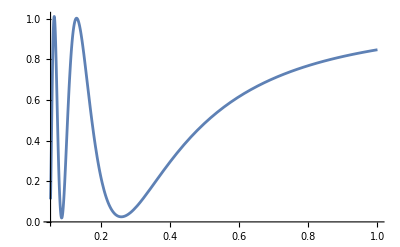

```mathematica
Plot[%27,{Energy,0.54 10^9,10^10}]
```

```mathematica
Subscript[P, ττ]=1-1/((-1+A)^2 A Energy)(-1+Subscript[s, 23]^2) (2 Energy ((-2+A) A-(-1+A)^2 Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]+(-1+A) (-A+(-1+A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)])) Subscript[s, 13]^2+(-4 (-1+A)^2 A Energy Sin[(L Subscript[m, 31])/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L Subscript[m, 31])/(2 Energy)]-Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)])+Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 13]^2-(-1+A) A L Sin[(L Subscript[m, 31])/(2 Energy)] Subscript[m, 31] ((-1+A) α (-1+Subscript[s, 12]^2)-A Subscript[s, 13]^2)) Subscript[s, 23]^2)
```

1-1/((-1+A)^2 A Energy)(-1+s_23^2) (2 Energy ((-2+A) A-(-1+A)^2 Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]+(-1+A) (-A+(-1+A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)])) s_13^2+(-4 (-1+A)^2 A Energy Sin[(L m_31)/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)])+Cos[(A L m_31)/(2 Energy)]) s_13^2-(-1+A) A L Sin[(L m_31)/(2 Energy)] m_31 ((-1+A) α (-1+s_12^2)-A s_13^2)) s_23^2)

```mathematica
ReplaceAll[Subscript[P, ττ],{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[50 Degree], Subscript[c, 23]->Cos[50 Degree], α->(7.50/2.55) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

1+1/((-1+8.89412×10^-17 Energy)^2 Energy^2)4.6455×10^15 (0.0440019 Energy (8.89412×10^-17 (-2+8.89412×10^-17 Energy) Energy-(-1+8.89412×10^-17 Energy)^2 Cos[(8.3895×10^9)/Energy]+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]+(-1+8.89412×10^-17 Energy) (-8.89412×10^-17 Energy+(-1+8.89412×10^-17 Energy) Cos[(8.3895×10^9)/Energy]+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]))+Cos[40 °]^2 (0.0440019 Energy (-2.78333×10^-13-1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy+(1+1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy) Cos[(8.3895×10^9)/Energy]-Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]-(-1+8.89412×10^-17 Energy) (2.78333×10^-13-1.77882×10^-16 Energy+(-1+1.77882×10^-16 Energy) Cos[(8.3895×10^9)/Energy]+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]))-3.55765×10^-16 (-1+8.89412×10^-17 Energy)^2 Energy^2 Sin[(4.19475×10^9)/Energy]^2-1.49234×10^-6 (-0.0200717 (-1+8.89412×10^-17 Energy)-1.95679×10^-18 Energy) (-1+8.89412×10^-17 Energy) Energy Sin[(8.3895×10^9)/Energy]))

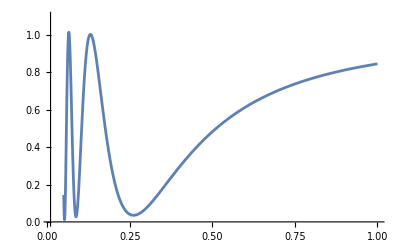

```mathematica
Plot[%22,{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

```mathematica
Subscript[P, μe]+Subscript[P, μμ]+Subscript[P, μτ]
```

1+(4 Sin[((-1+A) L m_31)/(4 Energy)]^2 s_13^2 s_23^2)/(-1+A)^2+1/((-1+A)^2 A Energy)(-4 (-1+A)^2 A Energy Sin[(L m_31)/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)])+Cos[(A L m_31)/(2 Energy)]) s_13^2-(-1+A) A L Sin[(L m_31)/(2 Energy)] m_31 ((-1+A) α (-1+s_12^2)-A s_13^2)) s_23^2 (-1+s_23^2)+1/((-1+A)^2 A Energy)s_23^2 ((-1+A) A L Sin[(L m_31)/(2 Energy)] m_31 ((-1+A) α (-1+s_12^2)-A s_13^2) (-1+s_23^2)+2 Energy (2 (-1+A)^2 A Sin[(L m_31)/(4 Energy)]^2 (-1+s_23^2)+s_13^2 (-(-1+A)^2+(-2+A) A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1+2 (-2+A) A+(-1-2 (-2+A) A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2+(-1+A) (-1+A-A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2))))

```mathematica
ReplaceAll[%29,{L->6.58 10^12, Subscript[m, 31]->2.55 10^-3, Subscript[s, 12]->Sin[34.3 Degree],Subscript[c, 12]->Cos[34.3 Degree],Subscript[s, 13]->Sin[8.53 Degree],Subscript[c, 13]->Cos[8.53 Degree], Subscript[s, 23]->Sin[50 Degree], Subscript[c, 23]->Cos[50 Degree], α->(7.50/2.55) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

1-1/((-1+8.89412×10^-17 Energy)^2 Energy^2)2.72609×10^15 (0.0440019 Energy (-2.78333×10^-13-1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy+(1+1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy) Cos[(8.3895×10^9)/Energy]-Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]-(-1+8.89412×10^-17 Energy) (2.78333×10^-13-1.77882×10^-16 Energy+(-1+1.77882×10^-16 Energy) Cos[(8.3895×10^9)/Energy]+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy]))-3.55765×10^-16 (-1+8.89412×10^-17 Energy)^2 Energy^2 Sin[(4.19475×10^9)/Energy]^2-1.49234×10^-6 (-0.0200717 (-1+8.89412×10^-17 Energy)-1.95679×10^-18 Energy) (-1+8.89412×10^-17 Energy) Energy Sin[(8.3895×10^9)/Energy])+1/((-1+8.89412×10^-17 Energy)^2 Energy^2)6.59789×10^15 (2 Energy (0.022001 (1.-(-1+8.89412×10^-17 Energy)^2+8.89412×10^-17 (-2+8.89412×10^-17 Energy) Energy Cos[(8.3895×10^9)/Energy]+Cos[40 °]^2 (2.78333×10^-13+1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy+(-1-1.77882×10^-16 (-2+8.89412×10^-17 Energy) Energy) Cos[(8.3895×10^9)/Energy]+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy])+(-1+8.89412×10^-17 Energy) (-2.78333×10^-13+8.89412×10^-17 Energy-8.89412×10^-17 Energy Cos[(8.3895×10^9)/Energy]+Cos[40 °]^2 (2.78333×10^-13-1.77882×10^-16 Energy+(-1+1.77882×10^-16 Energy) Cos[(8.3895×10^9)/Energy]+Cos[(8.3895×10^9 (-1+8.89412×10^-17 Energy))/Energy])))-7.34967×10^-17 (-1+8.89412×10^-17 Energy)^2 Energy Sin[(4.19475×10^9)/Energy]^2)-6.16601×10^-7 (-0.0200717 (-1+8.89412×10^-17 Energy)-1.95679×10^-18 Energy) (-1+8.89412×10^-17 Energy) Energy Sin[(8.3895×10^9)/Energy])+(0.0516428 Sin[(4.19475×10^9 (-1+8.89412×10^-17 Energy))/Energy]^2)/((-1+8.89412×10^-17 Energy)^2)

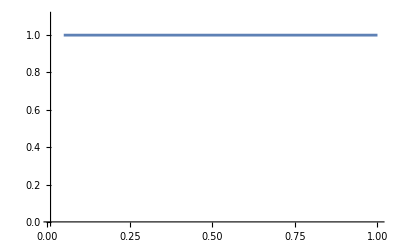

```mathematica
Plot[%30,{Energy,0.5 10^9,10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

## rumus2 probabilitas yg dihitung

```mathematica
Subscript[P, ee]=Collect[1+1/((-1+A)^2 A)2 (1-2 A+A^2 Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-(-1+A)^2 Cos[(A L Subscript[m, 31])/(2 Energy)]+(-1+A) (1-A Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]+(-1+A) Cos[(A L Subscript[m, 31])/(2 Energy)])) Subscript[s, 13]^2,Subscript[s, 13]]
```

1+(2 (1-2 A+A^2 Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A)^2 Cos[(A L m_31)/(2 Energy)]+(-1+A) (1-A Cos[((-1+A) L m_31)/(2 Energy)]+(-1+A) Cos[(A L m_31)/(2 Energy)])) s_13^2)/((-1+A)^2 A)

```mathematica
ReplaceAll[Subscript[P, ee],{(A-1)->B,(1-A)->-B,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,(Subscript[m, 31])/(4 Energy) -> Δ,(Subscript[m, 31])/( Energy) ->4 Δ}]
```

1+(2 (1-2 A+A^2 Cos[2 (-1+A) L Δ]-B^2 Cos[2 A L Δ]+B (1-A Cos[2 (-1+A) L Δ]+B Cos[2 A L Δ])) s_13^2)/(A B^2)

```mathematica
ReplaceAll[%381,{(A-1)->B,(1-A)->-B,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,(Subscript[m, 31])/(4 Energy) -> Δ,(Subscript[m, 31])/( Energy) ->4 Δ}]
```

```mathematica
%32
```

1+(2 (1-2 A+A^2 Cos[2 (-1+A) L Δ]-B^2 Cos[2 A L Δ]+B (1-A Cos[2 (-1+A) L Δ]+B Cos[2 A L Δ])) s_13^2)/(A B^2)

```mathematica
Collect[Simplify[%169],Subscript[s, 13]]
```

1+(2 (1-2 A+B+A (A-B) Cos[2 (-1+A) L Δ]) s_13^2)/(A B^2)

```mathematica
1+(2 (-1+ Cos[2 B L Δ]) Subscript[s, 13]^2)/B^2
```

```mathematica
Subscript[P, ee vac]=Limit[Subscript[P, ee],A->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1-4 Sin[(L m_31)/(4 Energy)]^2 s_13^2

```mathematica
Subscript[P, eμ]=Collect[(2 Subscript[s, 13] Subscript[s, 23] ((-1+A) α (Cos[δ]+Cos[δ+(L Subscript[m, 31])/(2 Energy)]-Cos[δ-((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[δ+(A L Subscript[m, 31])/(2 Energy)]) Subscript[c, 12] Subscript[c, 23] Subscript[s, 12]+2 A Sin[((-1+A) L Subscript[m, 31])/(4 Energy)]^2 Subscript[s, 13] Subscript[s, 23]))/((-1+A)^2 A),Subscript[s, 13]]
```

(2 α (Cos[δ]+Cos[δ+(L m_31)/(2 Energy)]-Cos[δ-((-1+A) L m_31)/(2 Energy)]-Cos[δ+(A L m_31)/(2 Energy)]) c_12 c_23 s_12 s_13 s_23)/((-1+A) A)+(4 Sin[((-1+A) L m_31)/(4 Energy)]^2 s_13^2 s_23^2)/(-1+A)^2

```mathematica
ReplaceAll[Subscript[P, eμ],{(A-1)->B,(1-A)->-B,(A-1)^2->B^2,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,(Subscript[m, 31])/(4 Energy) -> Δ,(Subscript[m, 31])/( Energy) ->4 Δ,2 L Δ->D}]
```

(2 α (Cos[δ]+Cos[δ+2 L Δ]-Cos[δ-2 (-1+A) L Δ]-Cos[δ+2 A L Δ]) c_12 c_23 s_12 s_13 s_23)/(A B)+(4 Sin[(-1+A) L Δ]^2 s_13^2 s_23^2)/B^2

```mathematica
ReplaceAll[%183,{(A-1)->B,(A-1)^2->C,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,B^2->C,2 L Δ->2D,(-2 L Δ)->-2D}]
```

(2 α (-Cos[2 (-1+A) D-δ]+Cos[δ]+Cos[2 D+δ]-Cos[2 A D+δ]) c_12 c_23 s_12 s_13 s_23)/(A B)+(4 Sin[B L Δ]^2 s_13^2 s_23^2)/B^2

```mathematica
Collect[FullSimplify[%199],Subscript[s, 13]]
```

-(8 α Cos[D+δ] Sin[A D] Sin[D-A D] c_12 c_23 s_12 s_13 s_23)/(A B)+(4 Sin[B L Δ]^2 s_13^2 s_23^2)/B^2

```mathematica
FullSimplify[(2 α (Cos[δ]+Cos[δ+2D]-Cos[δ-2(A-1)D]-Cos[δ+2AD]) Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] Subscript[s, 23])/((A-1) A)+(4 Sin[B L Δ]^2 Subscript[s, 13]^2 Subscript[s, 23]^2)/B^2]
```

2 s_13 s_23 ((α (Cos[δ]-Cos[2 AD+δ]-2 Sin[A D] Sin[2 D-A D+δ]) c_12 c_23 s_12)/((-1+A) A)+(2 Sin[B L Δ]^2 s_13 s_23)/B^2)

```mathematica
FullSimplify[(2 α (-Cos[(-1+A) D-δ]+Cos[δ]+Cos[D+δ]-Cos[A D+δ]) Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] Subscript[s, 23])/(A B)+(4 Sin[B L Δ]^2 Subscript[s, 13]^2 Subscript[s, 23]^2)/B^2]
```

(4 s_13 s_23 (-2 B α Cos[D/2+δ] Sin[(A D)/2] Sin[1/2 (D-A D)] c_12 c_23 s_12+A Sin[B L Δ]^2 s_13 s_23))/(A B^2)

```mathematica
Subscript[P, eμ vac]=Limit[Subscript[P, eμ],A->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(2 Sin[(L m_31)/(4 Energy)] s_13 s_23 (L α Cos[δ+(L m_31)/(4 Energy)] c_12 c_23 m_31 s_12+2 Energy Sin[(L m_31)/(4 Energy)] s_13 s_23))/Energy

```mathematica
Collect[%247,Subscript[s, 13]]
```

%247

```mathematica
Subscript[P, eτ]=Collect[(2 Subscript[s, 13] (-((-1+A) α (Cos[δ]+Cos[δ+(L Subscript[m, 31])/(2 Energy)]-Cos[δ-((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[δ+(A L Subscript[m, 31])/(2 Energy)]) Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 23])+A (-1+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]) Subscript[s, 13] (-1+Subscript[s, 23]^2)))/((-1+A)^2 A),Subscript[s, 13]]
```

(2 (1-A) α (Cos[δ]+Cos[δ+(L m_31)/(2 Energy)]-Cos[δ-((-1+A) L m_31)/(2 Energy)]-Cos[δ+(A L m_31)/(2 Energy)]) c_12 c_23 s_12 s_13 s_23)/((-1+A)^2 A)+(2 (-1+Cos[((-1+A) L m_31)/(2 Energy)]) s_13^2 (-1+s_23^2))/(-1+A)^2

```mathematica
ReplaceAll[Subscript[P, eτ],{(A-1)->B,(A-1)^2->C,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(4 Energy) -> Δ,B^2->C,2 L Δ->2D,(-2 L Δ)->-2D}]
```

(2 (1-A) α (Cos[δ]+Cos[δ+2 L Δ]-Cos[δ+2 A L Δ]-Cos[δ-(B L m_31)/(2 Energy)]) c_12 c_23 s_12 s_13 s_23)/(A B^2)+(2 (-1+Cos[2 (-1+A) L Δ]) s_13^2 (-1+s_23^2))/B^2

```mathematica
ReplaceAll[%201,{(A-1)->B,(1-A)->-B,(A-1)^2->C,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,B^2->C,2 L Δ->2D,(-2 L Δ)->-2D}]
```

-(2 α (Cos[δ]+Cos[2 D+δ]-Cos[2 A D+δ]-Cos[δ-2 B L Δ]) c_12 c_23 s_12 s_13 s_23)/(A B)+(2 (-1+Cos[2 (-1+A) D]) s_13^2 (-1+s_23^2))/B^2

```mathematica
Collect[FullSimplify[%202],Subscript[s, 13]]
```

(2 α (-Cos[δ]-Cos[2 D+δ]+Cos[2 A D+δ]+Cos[δ-2 B L Δ]) c_12 c_23 s_12 s_13 s_23)/(A B)-(4 Sin[(-1+A) D]^2 s_13^2 (-1+s_23^2))/B^2

```mathematica
Collect[FullSimplify[(2 α (-Cos[δ]-Cos[2 D+δ]+Cos[2 A D+δ]+Cos[δ-2 (A-1) D]) Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] Subscript[s, 23])/(A B)-(4 Sin[B D]^2 Subscript[s, 13]^2 (-1+Subscript[s, 23]^2))/B^2],Subscript[s, 13]]
```

(8 α Cos[D+δ] Sin[A D] Sin[D-A D] c_12 c_23 s_12 s_13 s_23)/(A B)-(4 Sin[B D]^2 s_13^2 (-1+s_23^2))/B^2

```mathematica
Subscript[P, eτ vac]=Collect[Limit[Subscript[P, eτ],A->0],Subscript[s, 13]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-(2 L α Cos[δ+(L m_31)/(4 Energy)] Sin[(L m_31)/(4 Energy)] c_12 c_23 m_31 s_12 s_13 s_23)/Energy-4 Sin[(L m_31)/(4 Energy)]^2 s_13^2 (-1+s_23^2)

```mathematica
Subscript[P, μμ]=Collect[1+1/((-1+A)^2 A Energy)Subscript[s, 23] (-4 (-1+A) Energy α Cos[δ] Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] (1-A+A Cos[(L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)]+2 Sin[(L Subscript[m, 31])/(4 Energy)] ((-1+2 A) Sin[(L Subscript[m, 31])/(4 Energy)]+Sin[((1-2 A) L Subscript[m, 31])/(4 Energy)]) Subscript[s, 23]^2+2 (-1+A) A Sin[(L Subscript[m, 31])/(4 Energy)]^2 (-1+2 Subscript[s, 23]^2))+Subscript[s, 23] ((-1+A) A L Sin[(L Subscript[m, 31])/(2 Energy)] Subscript[m, 31] ((-1+A) α (-1+Subscript[s, 12]^2)-A Subscript[s, 13]^2) (-1+Subscript[s, 23]^2)+2 Energy (2 (-1+A)^2 A Sin[(L Subscript[m, 31])/(4 Energy)]^2 (-1+Subscript[s, 23]^2)+Subscript[s, 13]^2 (-(-1+A)^2+(-2+A) A Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[(A L Subscript[m, 31])/(2 Energy)]+(1+2 (-2+A) A+(-1-2 (-2+A) A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 23]^2+(-1+A) (-1+A-A Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[(A L Subscript[m, 31])/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 23]^2))))),Subscript[s, 13]]
```

1+4 Sin[(L m_31)/(4 Energy)]^2 s_23^2 (-1+s_23^2)+(L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) s_23^2 (-1+s_23^2))/Energy-1/((-1+A) A)4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (1-A+A Cos[(L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]+2 Sin[(L m_31)/(4 Energy)] ((-1+2 A) Sin[(L m_31)/(4 Energy)]+Sin[((1-2 A) L m_31)/(4 Energy)]) s_23^2+2 (-1+A) A Sin[(L m_31)/(4 Energy)]^2 (-1+2 s_23^2))+s_13^2 (-(A L Sin[(L m_31)/(2 Energy)] m_31 s_23^2 (-1+s_23^2))/((-1+A) Energy)+1/((-1+A)^2 A)2 s_23^2 (-(-1+A)^2+(-2+A) A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1+2 (-2+A) A+(-1-2 (-2+A) A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2+(-1+A) (-1+A-A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2)))

```mathematica
1+4 Sin[D]^2 Subscript[s, 23]^2 (-1+Subscript[s, 23]^2)+4D α Sin[2D]  (-1+Subscript[s, 12]^2) Subscript[s, 23]^2 (-1+Subscript[s, 23]^2)-1/(B A)4 α Cos[δ] Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] Subscript[s, 23] (-B+A Cos[2D]-Cos[2AD]+2 Sin[D] ((A+B) Sin[D]-Sin[(A+B) D]) Subscript[s, 23]^2+2 B A Sin[D]^2 (-1+2 Subscript[s, 23]^2))+Subscript[s, 13]^2 (-(4 A D Sin[2D] Subscript[s, 23]^2 (-1+Subscript[s, 23]^2))/B+1/(B^2 A)2 Subscript[s, 23]^2 (-B^2+(B-1) A Cos[2D]+Cos[2AD]+(1+2 (B-1) A+(-1-2 (B-1) A) Cos[2D]+Cos[2BD]-Cos[2AD]) Subscript[s, 23]^2+B (B-A Cos[2D]+Cos[2AD]+(-(A+B)+(A+B) Cos[2D]+Cos[2BD]-Cos[2AD]) Subscript[s, 23]^2)))
```

```mathematica
ReplaceAll[Subscript[P, μμ],{(A-1)->B,(1-A)->-B,(A-1)^2->B^2,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,(Subscript[m, 31])/(4 Energy) -> Δ,(Subscript[m, 31])/( Energy) ->4 Δ, L Δ->D}]
```

1+4 Sin[L Δ]^2 s_23^2 (-1+s_23^2)+4 L α Δ Sin[(L m_31)/(2 Energy)] (-1+s_12^2) s_23^2 (-1+s_23^2)-(4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (-B+A Cos[(L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]+2 Sin[(L m_31)/(4 Energy)] ((-1+2 A) Sin[(L m_31)/(4 Energy)]+Sin[((1-2 A) L m_31)/(4 Energy)]) s_23^2+2 (-1+A) A Sin[(L m_31)/(4 Energy)]^2 (-1+2 s_23^2)))/(A B)+s_13^2 (-(4 A L Δ Sin[(L m_31)/(2 Energy)] s_23^2 (-1+s_23^2))/(-1+A)+1/(A B^2)2 s_23^2 (-B^2+(-2+A) A Cos[2 L Δ]+Cos[2 A L Δ]+(1+2 (-2+A) A+(-1-2 (-2+A) A) Cos[2 L Δ]+Cos[2 (-1+A) L Δ]-Cos[2 A L Δ]) s_23^2+B (B-A Cos[(L m_31)/(2 Energy)]+Cos[(A L m_31)/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2)))

```mathematica
ReplaceAll[%48,{(A-1)->B,(1-A)->-B,(A-1)^2->B^2,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,(Subscript[m, 31])/(4 Energy) -> Δ,(Subscript[m, 31])/( Energy) ->4 Δ,L Δ->D}]
```

1+4 Sin[D]^2 s_23^2 (-1+s_23^2)+4 D α Sin[(L m_31)/(2 Energy)] (-1+s_12^2) s_23^2 (-1+s_23^2)-(4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (-B+A Cos[2 L Δ]-Cos[2 A L Δ]+2 Sin[L Δ] ((-1+2 A) Sin[L Δ]+Sin[(1-2 A) L Δ]) s_23^2+2 A B Sin[L Δ]^2 (-1+2 s_23^2)))/(A B)+s_13^2 (-(4 A D Sin[(L m_31)/(2 Energy)] s_23^2 (-1+s_23^2))/(-1+A)+1/(A B^2)2 s_23^2 (-B^2+(-2+A) A Cos[2 D]+Cos[2 A D]+(1+2 (-2+A) A+(-1-2 (-2+A) A) Cos[2 D]+Cos[2 (-1+A) D]-Cos[2 A D]) s_23^2+B (B-A Cos[2 L Δ]+Cos[2 A L Δ]+(1-2 A+(-1+2 A) Cos[2 L Δ]+Cos[2 (-1+A) L Δ]-Cos[2 A L Δ]) s_23^2)))

```mathematica
Collect[Simplify[%122],Subscript[s, 13]]
```

1+4 Sin[D]^2 s_23^2 (-1+s_23^2)+4 D α Sin[(L m_31)/(2 Energy)] (-1+s_12^2) s_23^2 (-1+s_23^2)-(4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (-B+A Cos[2 L Δ]-Cos[2 A L Δ]-2 A B Sin[L Δ]^2+2 Sin[L Δ] ((-1+2 A (1+B)) Sin[L Δ]+Sin[(1-2 A) L Δ]) s_23^2))/(A B)+(2 s_13^2 s_23^2 (-(2 A^2 D Sin[(L m_31)/(2 Energy)] (-1+s_23^2))/(-1+A)+((-2+A) A Cos[2 D]+Cos[2 A D]-A B Cos[2 L Δ]+B Cos[2 A L Δ]+(1-4 A+2 A^2+B-2 A B+(-1+4 A-2 A^2) Cos[2 D]+Cos[2 (-1+A) D]-Cos[2 A D]-B Cos[2 L Δ]+2 A B Cos[2 L Δ]+B Cos[2 (-1+A) L Δ]-B Cos[2 A L Δ]) s_23^2)/B^2))/A

```mathematica
Subscript[P, μμ vac]=Collect[Limit[Subscript[P, μμ],A->0],Subscript[s, 13]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-(2 L α Cos[δ] Sin[(L m_31)/(2 Energy)] c_12 c_23 m_31 s_12 s_13 s_23^3)/Energy+(s_13^2 (4 Energy Sin[(L m_31)/(4 Energy)]^2 s_23^2-8 Energy Sin[(L m_31)/(4 Energy)]^2 s_23^4))/Energy+(Energy-4 Energy Sin[(L m_31)/(4 Energy)]^2 s_23^2-L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) s_23^2+4 Energy Sin[(L m_31)/(4 Energy)]^2 s_23^4+L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) s_23^4)/Energy

```mathematica
ReplaceAll[%251,{(A-1)->B,(1-A)->-B,(A-1)^2->C,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,(Subscript[m, 31])/(4 Energy) -> Δ,(Subscript[m, 31])/( Energy) ->4 Δ,B^2->C}]
```

%251

```mathematica
Subscript[P, μτ]=Collect[-1/((-1+A)^2 A Energy)Subscript[s, 23] (-((-4 (-1+A)^2 A Energy Sin[(L Subscript[m, 31])/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L Subscript[m, 31])/(2 Energy)]-Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)])+Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 13]^2-(-1+A) A L Sin[(L Subscript[m, 31])/(2 Energy)] Subscript[m, 31] ((-1+A) α (-1+Subscript[s, 12]^2)-A Subscript[s, 13]^2)) Subscript[s, 23] (-1+Subscript[s, 23]^2))+4 (-1+A) Energy α Sin[(L Subscript[m, 31])/(4 Energy)] Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] ((Cos[(L Subscript[m, 31])/(4 Energy)]-Cos[((-1+2 A) L Subscript[m, 31])/(4 Energy)]) Sin[δ]+Cos[δ] ((1-2 A-2 (-1+A) A) Sin[(L Subscript[m, 31])/(4 Energy)]+Sin[((-1+2 A) L Subscript[m, 31])/(4 Energy)]) (-1+2 Subscript[s, 23]^2))),Subscript[s, 13]]
```

-1/((-1+A)^2 A Energy)s_13^2 s_23 (-2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)])+Cos[(A L m_31)/(2 Energy)]) s_23 (-1+s_23^2)+(1-A) A^2 L Sin[(L m_31)/(2 Energy)] m_31 s_23 (-1+s_23^2))-(s_23 (4 (-1+A)^2 A Energy Sin[(L m_31)/(4 Energy)]^2 s_23 (-1+s_23^2)-(1-A) (-1+A) A L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) s_23 (-1+s_23^2)))/((-1+A)^2 A Energy)-(4 α Sin[(L m_31)/(4 Energy)] c_12 c_23 s_12 s_13 s_23 ((Cos[(L m_31)/(4 Energy)]-Cos[((-1+2 A) L m_31)/(4 Energy)]) Sin[δ]+Cos[δ] ((1-2 A-2 (-1+A) A) Sin[(L m_31)/(4 Energy)]+Sin[((-1+2 A) L m_31)/(4 Energy)]) (-1+2 s_23^2)))/((-1+A) A)

```mathematica
ReplaceAll[Subscript[P, μτ],{(A-1)->B,(1-A)->-B,(A-1)^2->B^2,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,(Subscript[m, 31])/(4 Energy) -> Δ,(Subscript[m, 31])/( Energy) ->4 Δ,L Δ->D}]
```

-1/(A B^2 Energy)s_13^2 s_23 (-2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[2 L Δ]-Cos[2 (-1+A) L Δ]-B (1-2 A+(-1+2 A) Cos[2 L Δ]+Cos[2 (-1+A) L Δ]-Cos[2 A L Δ])+Cos[2 A L Δ]) s_23 (-1+s_23^2)-A^2 B L Sin[2 L Δ] m_31 s_23 (-1+s_23^2))-(s_23 (4 A B^2 Energy Sin[L Δ]^2 s_23 (-1+s_23^2)+A B^2 L α Sin[2 L Δ] m_31 (-1+s_12^2) s_23 (-1+s_23^2)))/(A B^2 Energy)-(4 α Sin[L Δ] c_12 c_23 s_12 s_13 s_23 ((Cos[L Δ]-Cos[(-1+2 A) L Δ]) Sin[δ]+Cos[δ] ((1-2 A-2 A B) Sin[L Δ]+Sin[(-1+2 A) L Δ]) (-1+2 s_23^2)))/(A B)

```mathematica
ReplaceAll[%54,{(A-1)->B,(1-A)->-B,(A-1)^2->B^2,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,(Subscript[m, 31])/(4 Energy) -> Δ,(Subscript[m, 31])/( Energy) ->4 Δ,L Δ->D}]
```

-(s_13^2 s_23 (-2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[2 D]-Cos[2 (-1+A) D]-B (1-2 A+(-1+2 A) Cos[2 D]+Cos[2 (-1+A) D]-Cos[2 A D])+Cos[2 A D]) s_23 (-1+s_23^2)-A^2 B L Sin[2 D] m_31 s_23 (-1+s_23^2)))/(A B^2 Energy)-(s_23 (4 A B^2 Energy Sin[D]^2 s_23 (-1+s_23^2)+A B^2 L α Sin[2 D] m_31 (-1+s_12^2) s_23 (-1+s_23^2)))/(A B^2 Energy)-(4 α Sin[D] c_12 c_23 s_12 s_13 s_23 ((Cos[D]-Cos[(-1+2 A) D]) Sin[δ]+Cos[δ] ((1-2 A-2 A B) Sin[D]+Sin[(-1+2 A) D]) (-1+2 s_23^2)))/(A B)

```mathematica
Collect[FullSimplify[%124],Subscript[s, 13]]
```

```mathematica
-(2 Sin[D] (2 Energy Sin[D]+L α Cos[D] Subscript[m, 31] (-1+Subscript[s, 12]^2)) Subscript[s, 23]^2 (-1+Subscript[s, 23]^2))/Energy+((2 Energy (-1-B+2 A (2-A+B)+(1+2 A (-2+A-B)+B) Cos[2 D]-(1+B) Cos[2 (-1+A) D]+(1+B) Cos[2 A D])+A^2 B L Sin[2 D] Subscript[m, 31]) Subscript[s, 13]^2 Subscript[s, 23]^2 (-1+Subscript[s, 23]^2))/(A B^2 Energy)+(4 α Sin[D] Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] Subscript[s, 23])/(A B)(Cos[δ] (Sin[D]-2 A (1+B) Sin[D]+Sin[(-1+2 A) D])+2 Sin[A D] Sin[D-A D] Sin[δ]+2 Subscript[s, 23]^2 Cos[δ] ((-1+2 A (1+B)) Sin[D]+Sin[D-2 A D]) )
```

```mathematica
-4 (Sin^2)[D]+4D Sin[2D] α  (-1+Subscript[s, 12]^2) Subscript[s, 23]^2 (-1+Subscript[s, 23]^2)+(2 - 2Cos[2 D]- 2Cos[2 B D]+ 2Cos[2 A D]+4 D  Sin[2 D] )/B Subscript[s, 13]^2 Subscript[s, 23]^2 (-1+Subscript[s, 23]^2)+4 α Sin[D] Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] Subscript[s, 23](-(2 A^2-1)Cos[δ] Sin[D]+Cos[δ] Sin[(A+B) D]-2 Sin[A D] Sin[B D] Sin[δ]+2 Cos[δ] Subscript[s, 23]^2((2 A^2-1)Sin[D]-Sin[(A+B) D]) )/(A B)
```

```mathematica
Subscript[P, μτ vac] = Collect[Simplify[Limit[Subscript[P, μτ],A->0]],Subscript[s, 13]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

8 Sin[(L m_31)/(4 Energy)]^2 s_13^2 s_23^2 (-1+s_23^2)-(2 L α Sin[(L m_31)/(4 Energy)] c_12 c_23 m_31 s_12 s_13 s_23 (Cos[δ-(L m_31)/(4 Energy)]-2 Cos[δ] Cos[(L m_31)/(4 Energy)] s_23^2))/Energy+(2 Sin[(L m_31)/(4 Energy)] s_23 (-2 Energy Sin[(L m_31)/(4 Energy)] s_23 (-1+s_23^2)-L α Cos[(L m_31)/(4 Energy)] m_31 (-1+s_12^2) s_23 (-1+s_23^2)))/Energy

```mathematica
Subscript[P, ττ]=Collect[1+1/((-1+A)^2 A Energy)(-((-1+Subscript[s, 23]^2) (2 Energy ((-2+A) A-(-1+A)^2 Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]+(-1+A) (-A+(-1+A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)])) Subscript[s, 13]^2+(-4 (-1+A)^2 A Energy Sin[(L Subscript[m, 31])/(4 Energy)]^2+2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L Subscript[m, 31])/(2 Energy)]-Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)])+Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 13]^2-(-1+A) A L Sin[(L Subscript[m, 31])/(2 Energy)] Subscript[m, 31] ((-1+A) α (-1+Subscript[s, 12]^2)-A Subscript[s, 13]^2)) Subscript[s, 23]^2))+4 (-1+A) Energy α Cos[δ] Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] Subscript[s, 23] (A-(-1+A) Cos[(L Subscript[m, 31])/(2 Energy)]-Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L Subscript[m, 31])/(2 Energy)]+Cos[((-1+A) L Subscript[m, 31])/(2 Energy)]-Cos[(A L Subscript[m, 31])/(2 Energy)]) Subscript[s, 23]^2+(-1+A) A (-1+Cos[(L Subscript[m, 31])/(2 Energy)]) (-1+2 Subscript[s, 23]^2))),Subscript[s, 13]]
```

1-4 Sin[(L m_31)/(4 Energy)]^2 s_23^2 (1-s_23^2)+((1-A) L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) s_23^2 (1-s_23^2))/((-1+A) Energy)+s_13^2 ((2 ((-2+A) A-(-1+A)^2 Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]+(-1+A) (-A+(-1+A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)])) (1-s_23^2))/((-1+A)^2 A)+(2 (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)])+Cos[(A L m_31)/(2 Energy)]) s_23^2 (1-s_23^2))/((-1+A)^2 A)+(A L Sin[(L m_31)/(2 Energy)] m_31 s_23^2 (1-s_23^2))/((-1+A) Energy))+(4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (A-(-1+A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]+(1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)]) s_23^2+(-1+A) A (-1+Cos[(L m_31)/(2 Energy)]) (-1+2 s_23^2)))/((-1+A) A)

```mathematica
ReplaceAll[Subscript[P, ττ],{(A-1)->B,(1-A)->-B,(A-1)^2->B^2,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,(Subscript[m, 31])/(4 Energy) -> Δ,(Subscript[m, 31])/( Energy) ->4 Δ,L Δ->D}]
```

1-4 Sin[L Δ]^2 s_23^2 (1-s_23^2)+(4 (1-A) L α Δ Sin[(L m_31)/(2 Energy)] (-1+s_12^2) s_23^2 (1-s_23^2))/(-1+A)+s_13^2 ((2 ((-2+A) A-B^2 Cos[2 L Δ]+Cos[2 (-1+A) L Δ]+B (-A+B Cos[2 L Δ]+Cos[2 (-1+A) L Δ])) (1-s_23^2))/(A B^2)+(2 (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[2 L Δ]-Cos[2 (-1+A) L Δ]-B (1-2 A+(-1+2 A) Cos[2 L Δ]+Cos[2 (-1+A) L Δ]-Cos[2 A L Δ])+Cos[2 A L Δ]) s_23^2 (1-s_23^2))/(A B^2)+(4 A L Δ Sin[(L m_31)/(2 Energy)] s_23^2 (1-s_23^2))/(-1+A))+(4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (A-B Cos[2 L Δ]-Cos[2 (-1+A) L Δ]+(1-2 A+(-1+2 A) Cos[2 L Δ]+Cos[2 (-1+A) L Δ]-Cos[2 A L Δ]) s_23^2+A B (-1+Cos[2 L Δ]) (-1+2 s_23^2)))/(A B)

```mathematica
ReplaceAll[%59,{(A-1)->B,(1-A)->-B,(A-1)^2->C,(Subscript[m, 31])/(2 Energy) -> 2Δ,(Subscript[m, 31])/(2 Energy) -> 2Δ,-(Subscript[m, 31])/(2 Energy) ->-2 Δ,(Subscript[m, 31])/(4 Energy) -> Δ,(Subscript[m, 31])/( Energy) ->4 Δ,B^2->C}]
```

1-4 Sin[L Δ]^2 s_23^2 (1-s_23^2)-4 L α Δ Sin[2 L Δ] (-1+s_12^2) s_23^2 (1-s_23^2)+s_13^2 ((2 ((-2+A) A-C Cos[2 L Δ]+Cos[2 B L Δ]+B (-A+B Cos[2 L Δ]+Cos[2 B L Δ])) (1-s_23^2))/(A B^2)+(2 (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[2 L Δ]+Cos[2 A L Δ]-Cos[2 B L Δ]-B (1-2 A+(-1+2 A) Cos[2 L Δ]-Cos[2 A L Δ]+Cos[2 B L Δ])) s_23^2 (1-s_23^2))/(A B^2)+(4 A L Δ Sin[2 L Δ] s_23^2 (1-s_23^2))/B)+(4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (A-B Cos[2 L Δ]-Cos[2 B L Δ]+(1-2 A+(-1+2 A) Cos[2 L Δ]-Cos[2 A L Δ]+Cos[2 B L Δ]) s_23^2+A B (-1+Cos[2 L Δ]) (-1+2 s_23^2)))/(A B)

```mathematica
Collect[FullSimplify[%127],Subscript[s, 13]]
```

1+4 Sin[L Δ] (Sin[L Δ]+2 L α Δ Cos[L Δ] (-1+s_12^2)) s_23^2 (-1+s_23^2)+(4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (A+A B-(1+A) B Cos[2 L Δ]-Cos[2 B L Δ]+(1-2 A (1+B)+(-1+2 A (1+B)) Cos[2 L Δ]-Cos[2 A L Δ]+Cos[2 B L Δ]) s_23^2))/(A B)+s_13^2 (-(2 (A (-2+A-B)+(B^2-C) Cos[2 L Δ]+(1+B) Cos[2 B L Δ]) (-1+s_23^2))/(A B^2)+(2 (1+2 A (-2+A-B)+B-(1+2 A (-2+A-B)+B) Cos[2 L Δ]-(1+B) Cos[2 A L Δ]+(1+B) Cos[2 B L Δ]-2 A^2 B L Δ Sin[2 L Δ]) s_23^2 (-1+s_23^2))/(A B^2))

```mathematica
FullSimplify[1+ 4(Sin^2)[D] Subscript[s, 23]^2 (1-Subscript[s, 23]^2)+4 D α  Sin[2D] (-1+Subscript[s, 12]^2) Subscript[s, 23]^2 (-1+Subscript[s, 23]^2)+(4 α Cos[δ] Subscript[c, 12] Subscript[c, 23] Subscript[s, 12] Subscript[s, 13] Subscript[s, 23])/(A B)(A^2-(A^2-1) Cos[2 D]-Cos[2 B D]+(1-2 A^2+(-1+2 A^2) Cos[2 D]-Cos[2 A D]+Cos[2 B D]) Subscript[s, 23]^2)+2 Subscript[s, 13]^2 (-1+Subscript[s, 23]^2)((1- Cos[2 B D])/B^2+(Subscript[s, 23]^2(-1+ Cos[2 D]- Cos[2 A D]+ Cos[2 B D]-2  B D Sin[2 D]))/B^2),{B==A-1}]
```

1+1/(A B^2)(4 B α Cos[δ] c_12 c_23 s_12 s_13 s_23 (1-Cos[2 B D]+2 B (2+B) Sin[D]^2+(-1+Cos[2 D]-Cos[2 A D]+Cos[2 B D]-4 B (2+B) Sin[D]^2) s_23^2)+2 (1+B) (-1+s_23^2) (2 B^2 (-Sin^2[D]+D α Sin[2 D] (-1+s_12^2)) s_23^2+s_13^2 (2 Sin[B D]^2+(-1+Cos[2 D]-Cos[2 A D]+Cos[2 B D]-2 B D Sin[2 D]) s_23^2)))

```mathematica
Collect[%209,{Subscript[s, 13],α}]
```

1-(4 (1+B) Sin^2[D] s_23^2 (-1+s_23^2))/A+(4 (1+B) D α Sin[2 D] (-1+s_12^2) s_23^2 (-1+s_23^2))/A+(4 α Cos[δ] c_12 c_23 s_12 s_13 s_23 (1-Cos[2 B D]+2 B (2+B) Sin[D]^2+(-1+Cos[2 D]-Cos[2 A D]+Cos[2 B D]-4 B (2+B) Sin[D]^2) s_23^2))/(A B)+(2 (1+B) s_13^2 (-1+s_23^2) (2 Sin[B D]^2+(-1+Cos[2 D]-Cos[2 A D]+Cos[2 B D]-2 B D Sin[2 D]) s_23^2))/(A B^2)

```mathematica
Subscript[P, ττ vac]=Collect[Limit[Subscript[P, ττ],A->0],Subscript[s, 13]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1-(2 L α Cos[δ] Sin[(L m_31)/(2 Energy)] c_12 c_23 m_31 s_12 s_13 s_23 (-1+s_23^2))/Energy+4 Sin[(L m_31)/(4 Energy)]^2 s_23^2 (-1+s_23^2)+(L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) s_23^2 (-1+s_23^2))/Energy-4 Sin[(L m_31)/(4 Energy)]^2 s_13^2 (1-3 s_23^2+2 s_23^4)

## rumus2 probabilitas lain

```mathematica
Subscript[P, μe]=ReplaceAll[Subscript[P, eμ],δ->-δ]
```

(2 α (Cos[δ]+Cos[δ-(L m_31)/(2 Energy)]-Cos[δ+((-1+A) L m_31)/(2 Energy)]-Cos[δ-(A L m_31)/(2 Energy)]) c_12 c_23 s_12 s_13 s_23)/((-1+A) A)+(4 Sin[((-1+A) L m_31)/(4 Energy)]^2 s_13^2 s_23^2)/(-1+A)^2

```mathematica
Subscript[P, τe]=ReplaceAll[Subscript[P, eτ],δ->-δ]
```

(2 (1-A) α (Cos[δ]+Cos[δ-(L m_31)/(2 Energy)]-Cos[δ+((-1+A) L m_31)/(2 Energy)]-Cos[δ-(A L m_31)/(2 Energy)]) c_12 c_23 s_12 s_13 s_23)/((-1+A)^2 A)+(2 (-1+Cos[((-1+A) L m_31)/(2 Energy)]) s_13^2 (-1+s_23^2))/(-1+A)^2

```mathematica
Subscript[P, τμ]=ReplaceAll[Subscript[P, μτ],δ->-δ]
```

-1/((-1+A)^2 A Energy)s_13^2 s_23 (-2 Energy (-1-2 (-2+A) A+(1+2 (-2+A) A) Cos[(L m_31)/(2 Energy)]-Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A) (1-2 A+(-1+2 A) Cos[(L m_31)/(2 Energy)]+Cos[((-1+A) L m_31)/(2 Energy)]-Cos[(A L m_31)/(2 Energy)])+Cos[(A L m_31)/(2 Energy)]) s_23 (-1+s_23^2)+(1-A) A^2 L Sin[(L m_31)/(2 Energy)] m_31 s_23 (-1+s_23^2))-(s_23 (4 (-1+A)^2 A Energy Sin[(L m_31)/(4 Energy)]^2 s_23 (-1+s_23^2)-(1-A) (-1+A) A L α Sin[(L m_31)/(2 Energy)] m_31 (-1+s_12^2) s_23 (-1+s_23^2)))/((-1+A)^2 A Energy)-(4 α Sin[(L m_31)/(4 Energy)] c_12 c_23 s_12 s_13 s_23 (-((Cos[(L m_31)/(4 Energy)]-Cos[((-1+2 A) L m_31)/(4 Energy)]) Sin[δ])+Cos[δ] ((1-2 A-2 (-1+A) A) Sin[(L m_31)/(4 Energy)]+Sin[((-1+2 A) L m_31)/(4 Energy)]) (-1+2 s_23^2)))/((-1+A) A)

## uji unitaritas

```mathematica
Subscript[P, ee]+Subscript[P, eμ]+Subscript[P, eτ]
```

1+(2 (1-2 A+A^2 Cos[((-1+A) L m_31)/(2 Energy)]-(-1+A)^2 Cos[(A L m_31)/(2 Energy)]+(-1+A) (1-A Cos[((-1+A) L m_31)/(2 Energy)]+(-1+A) Cos[(A L m_31)/(2 Energy)])) s_13^2)/((-1+A)^2 A)+(2 (1-A) α (Cos[δ]+Cos[δ+(L m_31)/(2 Energy)]-Cos[δ-((-1+A) L m_31)/(2 Energy)]-Cos[δ+(A L m_31)/(2 Energy)]) c_12 c_23 s_12 s_13 s_23)/((-1+A)^2 A)+(2 α (Cos[δ]+Cos[δ+(L m_31)/(2 Energy)]-Cos[δ-((-1+A) L m_31)/(2 Energy)]-Cos[δ+(A L m_31)/(2 Energy)]) c_12 c_23 s_12 s_13 s_23)/((-1+A) A)+(4 Sin[((-1+A) L m_31)/(4 Energy)]^2 s_13^2 s_23^2)/(-1+A)^2+(2 (-1+Cos[((-1+A) L m_31)/(2 Energy)]) s_13^2 (-1+s_23^2))/(-1+A)^2

```mathematica
ReplaceAll[%472,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

1+(2.24714×10^7 (1-8.89412×10^-11 Energy) (-0.443497+Cos[3.4383+(8.27106×10^9)/Energy]-Cos[3.4383-(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy)+(2.24714×10^7 (-0.443497+Cos[3.4383+(8.27106×10^9)/Energy]-Cos[3.4383-(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy) Energy)-(0.0189069 (-1+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2)+(4.95883×10^8 (1-0.741403 (-1+8.89412×10^-11 Energy)^2-1.77882×10^-10 Energy+7.91053×10^-21 Energy^2 Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]+(-1+8.89412×10^-11 Energy) (1+0.741403 (-1+8.89412×10^-11 Energy)-8.89412×10^-11 Energy Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])))/((-1+8.89412×10^-11 Energy)^2 Energy)+(0.050395 Sin[(4.13553×10^9 (-1+8.89412×10^-11 Energy))/Energy]^2)/((-1+8.89412×10^-11 Energy)^2)

```mathematica
Plot[%474,{Energy, 0.5 10^9, 10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

-Graphics-

```mathematica
ReplaceAll[Subscript[P, μe]+Subscript[P, μμ]+Subscript[P, μτ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

1+(2.24714×10^7 (-0.0510976+Cos[3.4383-(8.27106×10^9)/Energy]-Cos[3.4383+(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy) Energy)-0.979657 Sin[(4.13553×10^9)/Energy]^2+(8.27296×10^7 Sin[(8.27106×10^9)/Energy])/Energy+0.0220522 (1/((-1+8.89412×10^-11 Energy)^2 Energy)1.2847×10^10 (0.741403-(-1+8.89412×10^-11 Energy)^2+8.89412×10^-11 (-2+8.89412×10^-11 Energy) Energy Cos[(8.27106×10^9)/Energy]+0.571314 (0.258597+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(-1-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])+(-1+8.89412×10^-11 Energy) (-0.258597+8.89412×10^-11 Energy-8.89412×10^-11 Energy Cos[(8.27106×10^9)/Energy]+0.571314 (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])))+(0.360336 Sin[(8.27106×10^9)/Energy])/(-1+8.89412×10^-11 Energy))-(8.49835×10^9 (-1.15276×10^-10 (-1+8.89412×10^-11 Energy)^2 Energy^2 Sin[(4.13553×10^9)/Energy]^2-0.00973478 (1-8.89412×10^-11 Energy) (-1+8.89412×10^-11 Energy) Energy Sin[(8.27106×10^9)/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy^2)-1/((-1+8.89412×10^-11 Energy)^2 Energy^2)1.87407×10^8 (0.648047 Energy (-0.258597-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(1+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]-(-1+8.89412×10^-11 Energy) (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))-4.24007×10^-11 (1-8.89412×10^-11 Energy) Energy^2 Sin[(8.27106×10^9)/Energy])+(4.29791×10^7 (0.258597-8.89412×10^-11 Energy+8.89412×10^-11 Energy Cos[(8.27106×10^9)/Energy]+2.53712×10^-11 (-1+8.89412×10^-11 Energy) Energy Sin[(4.13553×10^9)/Energy]^2+1.14263 Sin[(4.13553×10^9)/Energy] ((-1+1.77882×10^-10 Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (1-1.77882×10^-10 Energy))/Energy])))/((-1+8.89412×10^-11 Energy) Energy)+(0.050395 Sin[(4.13553×10^9 (-1+8.89412×10^-11 Energy))/Energy]^2)/((-1+8.89412×10^-11 Energy)^2)-(4.49429×10^7 Sin[(4.13553×10^9)/Energy] (-0.292373 (Cos[(4.13553×10^9)/Energy]-Cos[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy])-0.136397 ((1-1.77882×10^-10 Energy-1.77882×10^-10 (-1+8.89412×10^-11 Energy) Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy])))/((-1+8.89412×10^-11 Energy) Energy)

```mathematica
Plot[%477,{Energy, 0.5 10^9, 10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

-Graphics-

```mathematica
ReplaceAll[Subscript[P, τe]+Subscript[P, τμ]+Subscript[P, ττ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

1+(2.24714×10^7 (1-8.89412×10^-11 Energy) (-0.0510976+Cos[3.4383-(8.27106×10^9)/Energy]-Cos[3.4383+(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy)-(0.0189069 (-1+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2)-(4.29791×10^7 (8.89412×10^-11 Energy+1.26856×10^-11 (-1+8.89412×10^-11 Energy) Energy (-1+Cos[(8.27106×10^9)/Energy])-(-1+8.89412×10^-11 Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]+0.571314 (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])))/((-1+8.89412×10^-11 Energy) Energy)-0.979657 Sin[(4.13553×10^9)/Energy]^2-(8.27296×10^7 (1-8.89412×10^-11 Energy) Sin[(8.27106×10^9)/Energy])/((-1+8.89412×10^-11 Energy) Energy)+0.0220522 ((9.63975×10^9 (8.89412×10^-11 (-2+8.89412×10^-11 Energy) Energy-(-1+8.89412×10^-11 Energy)^2 Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]+(-1+8.89412×10^-11 Energy) (-8.89412×10^-11 Energy+(-1+8.89412×10^-11 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])))/((-1+8.89412×10^-11 Energy)^2 Energy)+1/((-1+8.89412×10^-11 Energy)^2 Energy)5.50733×10^9 (-0.258597-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(1+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]-(-1+8.89412×10^-11 Energy) (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))+(0.360336 Sin[(8.27106×10^9)/Energy])/(-1+8.89412×10^-11 Energy))-(8.49835×10^9 (-1.15276×10^-10 (-1+8.89412×10^-11 Energy)^2 Energy^2 Sin[(4.13553×10^9)/Energy]^2-0.00973478 (1-8.89412×10^-11 Energy) (-1+8.89412×10^-11 Energy) Energy Sin[(8.27106×10^9)/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy^2)-1/((-1+8.89412×10^-11 Energy)^2 Energy^2)1.87407×10^8 (0.648047 Energy (-0.258597-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(1+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]-(-1+8.89412×10^-11 Energy) (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))-4.24007×10^-11 (1-8.89412×10^-11 Energy) Energy^2 Sin[(8.27106×10^9)/Energy])-(4.49429×10^7 Sin[(4.13553×10^9)/Energy] (0.292373 (Cos[(4.13553×10^9)/Energy]-Cos[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy])-0.136397 ((1-1.77882×10^-10 Energy-1.77882×10^-10 (-1+8.89412×10^-11 Energy) Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy])))/((-1+8.89412×10^-11 Energy) Energy)

```mathematica
Plot[%479,{Energy, 0.5 10^9, 10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

-Graphics-

```mathematica
ReplaceAll[Subscript[P, ee]+Subscript[P, μe]+Subscript[P, τe],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

1+(2.24714×10^7 (1-8.89412×10^-11 Energy) (-0.0510976+Cos[3.4383-(8.27106×10^9)/Energy]-Cos[3.4383+(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy)+(2.24714×10^7 (-0.0510976+Cos[3.4383-(8.27106×10^9)/Energy]-Cos[3.4383+(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy) Energy)-(0.0189069 (-1+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2)+(4.95883×10^8 (1-0.741403 (-1+8.89412×10^-11 Energy)^2-1.77882×10^-10 Energy+7.91053×10^-21 Energy^2 Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]+(-1+8.89412×10^-11 Energy) (1+0.741403 (-1+8.89412×10^-11 Energy)-8.89412×10^-11 Energy Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])))/((-1+8.89412×10^-11 Energy)^2 Energy)+(0.050395 Sin[(4.13553×10^9 (-1+8.89412×10^-11 Energy))/Energy]^2)/((-1+8.89412×10^-11 Energy)^2)

```mathematica
Plot[%481,{Energy, 0.5 10^9, 10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

-Graphics-

```mathematica
ReplaceAll[Subscript[P, eμ]+Subscript[P, μμ]+Subscript[P, τμ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

1+(2.24714×10^7 (-0.443497+Cos[3.4383+(8.27106×10^9)/Energy]-Cos[3.4383-(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy) Energy)-0.979657 Sin[(4.13553×10^9)/Energy]^2+(8.27296×10^7 Sin[(8.27106×10^9)/Energy])/Energy+0.0220522 (1/((-1+8.89412×10^-11 Energy)^2 Energy)1.2847×10^10 (0.741403-(-1+8.89412×10^-11 Energy)^2+8.89412×10^-11 (-2+8.89412×10^-11 Energy) Energy Cos[(8.27106×10^9)/Energy]+0.571314 (0.258597+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(-1-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])+(-1+8.89412×10^-11 Energy) (-0.258597+8.89412×10^-11 Energy-8.89412×10^-11 Energy Cos[(8.27106×10^9)/Energy]+0.571314 (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])))+(0.360336 Sin[(8.27106×10^9)/Energy])/(-1+8.89412×10^-11 Energy))-(8.49835×10^9 (-1.15276×10^-10 (-1+8.89412×10^-11 Energy)^2 Energy^2 Sin[(4.13553×10^9)/Energy]^2-0.00973478 (1-8.89412×10^-11 Energy) (-1+8.89412×10^-11 Energy) Energy Sin[(8.27106×10^9)/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy^2)-1/((-1+8.89412×10^-11 Energy)^2 Energy^2)1.87407×10^8 (0.648047 Energy (-0.258597-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(1+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]-(-1+8.89412×10^-11 Energy) (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))-4.24007×10^-11 (1-8.89412×10^-11 Energy) Energy^2 Sin[(8.27106×10^9)/Energy])+(4.29791×10^7 (0.258597-8.89412×10^-11 Energy+8.89412×10^-11 Energy Cos[(8.27106×10^9)/Energy]+2.53712×10^-11 (-1+8.89412×10^-11 Energy) Energy Sin[(4.13553×10^9)/Energy]^2+1.14263 Sin[(4.13553×10^9)/Energy] ((-1+1.77882×10^-10 Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (1-1.77882×10^-10 Energy))/Energy])))/((-1+8.89412×10^-11 Energy) Energy)+(0.050395 Sin[(4.13553×10^9 (-1+8.89412×10^-11 Energy))/Energy]^2)/((-1+8.89412×10^-11 Energy)^2)-(4.49429×10^7 Sin[(4.13553×10^9)/Energy] (0.292373 (Cos[(4.13553×10^9)/Energy]-Cos[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy])-0.136397 ((1-1.77882×10^-10 Energy-1.77882×10^-10 (-1+8.89412×10^-11 Energy) Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy])))/((-1+8.89412×10^-11 Energy) Energy)

```mathematica
Plot[%483,{Energy, 0.5 10^9, 10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

-Graphics-

```mathematica
ReplaceAll[Subscript[P, eτ]+Subscript[P, μτ]+Subscript[P, ττ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

1+(2.24714×10^7 (1-8.89412×10^-11 Energy) (-0.443497+Cos[3.4383+(8.27106×10^9)/Energy]-Cos[3.4383-(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy)-(0.0189069 (-1+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2)-(4.29791×10^7 (8.89412×10^-11 Energy+1.26856×10^-11 (-1+8.89412×10^-11 Energy) Energy (-1+Cos[(8.27106×10^9)/Energy])-(-1+8.89412×10^-11 Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]+0.571314 (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])))/((-1+8.89412×10^-11 Energy) Energy)-0.979657 Sin[(4.13553×10^9)/Energy]^2-(8.27296×10^7 (1-8.89412×10^-11 Energy) Sin[(8.27106×10^9)/Energy])/((-1+8.89412×10^-11 Energy) Energy)+0.0220522 ((9.63975×10^9 (8.89412×10^-11 (-2+8.89412×10^-11 Energy) Energy-(-1+8.89412×10^-11 Energy)^2 Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]+(-1+8.89412×10^-11 Energy) (-8.89412×10^-11 Energy+(-1+8.89412×10^-11 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])))/((-1+8.89412×10^-11 Energy)^2 Energy)+1/((-1+8.89412×10^-11 Energy)^2 Energy)5.50733×10^9 (-0.258597-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(1+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]-(-1+8.89412×10^-11 Energy) (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))+(0.360336 Sin[(8.27106×10^9)/Energy])/(-1+8.89412×10^-11 Energy))-(8.49835×10^9 (-1.15276×10^-10 (-1+8.89412×10^-11 Energy)^2 Energy^2 Sin[(4.13553×10^9)/Energy]^2-0.00973478 (1-8.89412×10^-11 Energy) (-1+8.89412×10^-11 Energy) Energy Sin[(8.27106×10^9)/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy^2)-1/((-1+8.89412×10^-11 Energy)^2 Energy^2)1.87407×10^8 (0.648047 Energy (-0.258597-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(1+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]-(-1+8.89412×10^-11 Energy) (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))-4.24007×10^-11 (1-8.89412×10^-11 Energy) Energy^2 Sin[(8.27106×10^9)/Energy])-(4.49429×10^7 Sin[(4.13553×10^9)/Energy] (-0.292373 (Cos[(4.13553×10^9)/Energy]-Cos[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy])-0.136397 ((1-1.77882×10^-10 Energy-1.77882×10^-10 (-1+8.89412×10^-11 Energy) Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy])))/((-1+8.89412×10^-11 Energy) Energy)

```mathematica
Plot[%485,{Energy, 0.5 10^9, 10^10},PlotRange->{{0.1 10^9, 10^10}, {0, 1.1}}]
```

-Graphics-

## numerik

```mathematica
ReplaceAll[Eigenvalues[H],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

{-1/Energy^8(0.000261355+0.00122953 ⅈ) Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1],-1/Energy^8(0.000261355+0.00122953 ⅈ) Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2],-1/Energy^8(0.000261355+0.00122953 ⅈ) Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]}

```mathematica
Subscript[NumE, 1]=Abs[-1/Energy^8(0.0002613551284434599+0.0012295293802249308 ⅈ) Root[(-8.131516293641283*^-20+1.6263032587282567*^-19 ⅈ) Energy^21-(1.0440175593873909*^-12-1.4368921832938387*^-12 ⅈ) Energy^22+((-0.026926500247545535-0.011988982113565274 ⅈ) Energy^14-(8.113481765557382*^-11+3.612515064035188*^-11 ⅈ) Energy^15) #1+((0.21404817443146343-1.0069766788751942 ⅈ) Energy^7+(1.849262736705094*^-11-8.699744596846346*^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]
```

0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]

```mathematica
Subscript[NumE, 2]=Abs[-1/Energy^8(0.0002613551284434599+0.0012295293802249308 ⅈ) Root[(-8.131516293641283*^-20+1.6263032587282567*^-19 ⅈ) Energy^21-(1.0440175593873909*^-12-1.4368921832938387*^-12 ⅈ) Energy^22+((-0.026926500247545535-0.011988982113565274 ⅈ) Energy^14-(8.113481765557382*^-11+3.612515064035188*^-11 ⅈ) Energy^15) #1+((0.21404817443146343-1.0069766788751942 ⅈ) Energy^7+(1.849262736705094*^-11-8.699744596846346*^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]
```

0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]

```mathematica
Subscript[NumE, 3]=Abs[-1/Energy^8(0.0002613551284434599+0.0012295293802249308 ⅈ) Root[(-8.131516293641283*^-20+1.6263032587282567*^-19 ⅈ) Energy^21-(1.0440175593873909*^-12-1.4368921832938387*^-12 ⅈ) Energy^22+((-0.026926500247545535-0.011988982113565274 ⅈ) Energy^14-(8.113481765557382*^-11+3.612515064035188*^-11 ⅈ) Energy^15) #1+((0.21404817443146343-1.0069766788751942 ⅈ) Energy^7+(1.849262736705094*^-11-8.699744596846346*^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]
```

0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]

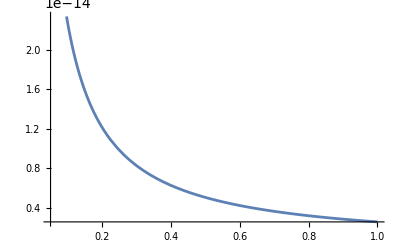

```mathematica
Plot[Subscript[NumE, 3],{Energy,0.5 10^9, 10^10}]
```

```mathematica
ReplaceAll[Eigenvalues[M],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^-3, δ->3.4383}]
```

{Root[-1.69407×10^-21-1.77613×10^-18 Energy+(0.0294749+8.88138×10^-17 Energy) #1+(-1.02947-8.89412×10^-17 Energy) #1^2+#1^3&,1],Root[-1.69407×10^-21-1.77613×10^-18 Energy+(0.0294749+8.88138×10^-17 Energy) #1+(-1.02947-8.89412×10^-17 Energy) #1^2+#1^3&,2],Root[-1.69407×10^-21-1.77613×10^-18 Energy+(0.0294749+8.88138×10^-17 Energy) #1+(-1.02947-8.89412×10^-17 Energy) #1^2+#1^3&,3]}

```mathematica
NumS=Exp[I Subscript[NumE, 1] L]/((Subscript[NumE, 1]-Subscript[NumE, 2])(Subscript[NumE, 1]-Subscript[NumE, 3])) (Subscript[NumE, 2] Subscript[NumE, 3] IdentityMatrix[3]-(Subscript[NumE, 2]+Subscript[NumE, 3]) H+H.H)+Exp[I Subscript[NumE, 2] L]/((Subscript[NumE, 2]-Subscript[NumE, 3])(Subscript[NumE, 2]-Subscript[NumE, 1])) (Subscript[NumE, 3] Subscript[NumE, 1] IdentityMatrix[3]-(Subscript[NumE, 3]+Subscript[NumE, 1]) H+H.H)+Exp[I Subscript[NumE, 3] L]/((Subscript[NumE, 3]-Subscript[NumE, 1])(Subscript[NumE, 3]-Subscript[NumE, 2])) (Subscript[NumE, 1] Subscript[NumE, 2] IdentityMatrix[3]-(Subscript[NumE, 1]+Subscript[NumE, 2]) H+H.H)
```

```mathematica
Subscript[NumP, ee]=ReplaceAll[(Abs[NumS[[1,1]]])^2,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(Abs[(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]/Energy^8]) ((3.37466×10^-8+0. ⅈ)/Energy^2+(1.58005×10^-6 (0.0309075+8.89412×10^-11 Energy)^2)/Energy^2-1/Energy 0.001257 (0.0309075+8.89412×10^-11 Energy) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]])+1.58005×10^-6 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]] Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]) (-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]/Energy^8]) ((3.37466×10^-8+0. ⅈ)/Energy^2+(1.58005×10^-6 (0.0309075+8.89412×10^-11 Energy)^2)/Energy^2-1/Energy 0.001257 (0.0309075+8.89412×10^-11 Energy) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])+1.58005×10^-6 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]] Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]/Energy^8]) ((3.37466×10^-8+0. ⅈ)/Energy^2+(1.58005×10^-6 (0.0309075+8.89412×10^-11 Energy)^2)/Energy^2-1/Energy 0.001257 (0.0309075+8.89412×10^-11 Energy) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])+1.58005×10^-6 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]] Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))/((0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))])^2

```mathematica
Subscript[ExpP, ee]=ReplaceAll[Subscript[P, ee],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->-3.4383}]
```

1+1/((-1+8.89412×10^-11 Energy)^2 Energy)4.95883×10^8 (1-0.741403 (-1+8.89412×10^-11 Energy)^2-1.77882×10^-10 Energy+7.91053×10^-21 Energy^2 Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]+(-1+8.89412×10^-11 Energy) (1+0.741403 (-1+8.89412×10^-11 Energy)-8.89412×10^-11 Energy Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))

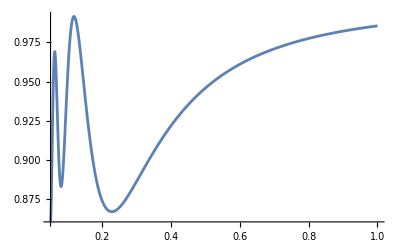

```mathematica
Plot[Subscript[NumP, ee],{Energy,0.5 10^9, 10^10}]
```

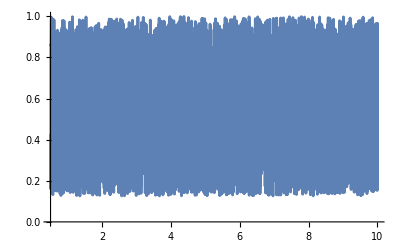

```mathematica
Plot[ReplaceAll[Subscript[NumP, ee],Energy->(Energy)× 10^9],{Energy,0.5, 10}]
```

```mathematica
Subscript[NumP, eμ]=ReplaceAll[(Abs[NumS[[1,2]]])^2,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(Abs[(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]/Energy^8]) (0.-(1.6256×10^-7-4.96936×10^-8 ⅈ)/Energy^2-((1.52291×10^-7-5.08135×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.000121155-0.0000404244 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]/Energy^8]) (0.-(1.6256×10^-7-4.96936×10^-8 ⅈ)/Energy^2-((1.52291×10^-7-5.08135×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.000121155-0.0000404244 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]/Energy^8]) (0.-(1.6256×10^-7-4.96936×10^-8 ⅈ)/Energy^2-((1.52291×10^-7-5.08135×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.000121155-0.0000404244 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]) (-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))])^2

```mathematica
Subscript[ExpP, eμ]=ReplaceAll[Subscript[P, eμ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->-3.4383}]
```

(2.24714×10^7 (-0.0510976+Cos[3.4383-(8.27106×10^9)/Energy]-Cos[3.4383+(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy) Energy)+(0.050395 Sin[(4.13553×10^9 (-1+8.89412×10^-11 Energy))/Energy]^2)/((-1+8.89412×10^-11 Energy)^2)

```mathematica
Subscript[NumP, eτ]=ReplaceAll[(Abs[NumS[[1,3]]])^2,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(Abs[(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]/Energy^8]) (0.-(1.40773×10^-7-4.30459×10^-8 ⅈ)/Energy^2-((1.60029×10^-7-4.4016×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.00012731-0.0000350167 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]/Energy^8]) (0.-(1.40773×10^-7-4.30459×10^-8 ⅈ)/Energy^2-((1.60029×10^-7-4.4016×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.00012731-0.0000350167 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]/Energy^8]) (0.-(1.40773×10^-7-4.30459×10^-8 ⅈ)/Energy^2-((1.60029×10^-7-4.4016×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.00012731-0.0000350167 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]) (-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))])^2

```mathematica
Subscript[ExpP, eτ]=ReplaceAll[Subscript[P, eτ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->-3.4383}]
```

(2.24714×10^7 (1-8.89412×10^-11 Energy) (-0.0510976+Cos[3.4383-(8.27106×10^9)/Energy]-Cos[3.4383+(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy)-(0.0189069 (-1+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2)

```mathematica
Subscript[NumP, μμ]=ReplaceAll[(Abs[NumS[[2,2]]])^2,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(Abs[(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]/Energy^8]) ((8.833×10^-7+0. ⅈ)/Energy^2-1/Energy(0.000715855+0. ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]])+1.58005×10^-6 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]] Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]) (-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]/Energy^8]) ((8.833×10^-7+0. ⅈ)/Energy^2-1/Energy(0.000715855+0. ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])+1.58005×10^-6 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]] Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]/Energy^8]) ((8.833×10^-7+0. ⅈ)/Energy^2-1/Energy(0.000715855+0. ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])+1.58005×10^-6 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]] Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))/((0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))])^2

```mathematica
Subscript[ExpP, μμ]=ReplaceAll[Subscript[P, μμ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

1-0.979657 Sin[(4.13553×10^9)/Energy]^2+(8.27296×10^7 Sin[(8.27106×10^9)/Energy])/Energy+0.0220522 (1/((-1+8.89412×10^-11 Energy)^2 Energy)1.2847×10^10 (0.741403-(-1+8.89412×10^-11 Energy)^2+8.89412×10^-11 (-2+8.89412×10^-11 Energy) Energy Cos[(8.27106×10^9)/Energy]+0.571314 (0.258597+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(-1-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])+(-1+8.89412×10^-11 Energy) (-0.258597+8.89412×10^-11 Energy-8.89412×10^-11 Energy Cos[(8.27106×10^9)/Energy]+0.571314 (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy])))+(0.360336 Sin[(8.27106×10^9)/Energy])/(-1+8.89412×10^-11 Energy))+1/((-1+8.89412×10^-11 Energy) Energy)4.29791×10^7 (0.258597-8.89412×10^-11 Energy+8.89412×10^-11 Energy Cos[(8.27106×10^9)/Energy]+2.53712×10^-11 (-1+8.89412×10^-11 Energy) Energy Sin[(4.13553×10^9)/Energy]^2+1.14263 Sin[(4.13553×10^9)/Energy] ((-1+1.77882×10^-10 Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (1-1.77882×10^-10 Energy))/Energy]))

```mathematica
Subscript[NumP, μτ]=ReplaceAll[(Abs[NumS[[2,3]]])^2,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(Abs[(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]/Energy^8]) (0.+(7.64225×10^-7-2.74952×10^-11 ⅈ)/Energy^2-1/Energy(0.000595432-7.42112×10^-7 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]/Energy^8]) (0.+(7.64225×10^-7-2.74952×10^-11 ⅈ)/Energy^2-1/Energy(0.000595432-7.42112×10^-7 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]/Energy^8]) (0.+(7.64225×10^-7-2.74952×10^-11 ⅈ)/Energy^2-1/Energy(0.000595432-7.42112×10^-7 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]) (-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))])^2

```mathematica
Subscript[ExpP, μτ]=ReplaceAll[Subscript[P, μτ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->-3.4383}]
```

-(8.49835×10^9 (-1.15276×10^-10 (-1+8.89412×10^-11 Energy)^2 Energy^2 Sin[(4.13553×10^9)/Energy]^2-0.00973478 (1-8.89412×10^-11 Energy) (-1+8.89412×10^-11 Energy) Energy Sin[(8.27106×10^9)/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy^2)-1/((-1+8.89412×10^-11 Energy)^2 Energy^2)1.87407×10^8 (0.648047 Energy (-0.258597-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(1+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]-(-1+8.89412×10^-11 Energy) (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))-4.24007×10^-11 (1-8.89412×10^-11 Energy) Energy^2 Sin[(8.27106×10^9)/Energy])-1/((-1+8.89412×10^-11 Energy) Energy)4.49429×10^7 Sin[(4.13553×10^9)/Energy] (0.292373 (Cos[(4.13553×10^9)/Energy]-Cos[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy])-0.136397 ((1-1.77882×10^-10 Energy-1.77882×10^-10 (-1+8.89412×10^-11 Energy) Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy]))

```mathematica
Subscript[NumP, ττ]=ReplaceAll[(Abs[NumS[[3,3]]])^2,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(Abs[(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]/Energy^8]) ((6.62866×10^-7-2.64698×10^-23 ⅈ)/Energy^2-1/Energy(0.000539344+2.71051×10^-20 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]])+1.58005×10^-6 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]] Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]) (-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]/Energy^8]) ((6.62866×10^-7-2.64698×10^-23 ⅈ)/Energy^2-1/Energy(0.000539344+2.71051×10^-20 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])+1.58005×10^-6 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]] Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]/Energy^8]) ((6.62866×10^-7-2.64698×10^-23 ⅈ)/Energy^2-1/Energy(0.000539344+2.71051×10^-20 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])+1.58005×10^-6 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]] Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))/((0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))])^2

```mathematica
Subscript[ExpP, ττ]=ReplaceAll[Subscript[P, ττ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

1-1/((-1+8.89412×10^-11 Energy) Energy)4.29791×10^7 (8.89412×10^-11 Energy+1.26856×10^-11 (-1+8.89412×10^-11 Energy) Energy (-1+Cos[(8.27106×10^9)/Energy])-(-1+8.89412×10^-11 Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]+0.571314 (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))-0.979657 Sin[(4.13553×10^9)/Energy]^2-(8.27296×10^7 (1-8.89412×10^-11 Energy) Sin[(8.27106×10^9)/Energy])/((-1+8.89412×10^-11 Energy) Energy)+0.0220522 (1/((-1+8.89412×10^-11 Energy)^2 Energy)9.63975×10^9 (8.89412×10^-11 (-2+8.89412×10^-11 Energy) Energy-(-1+8.89412×10^-11 Energy)^2 Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]+(-1+8.89412×10^-11 Energy) (-8.89412×10^-11 Energy+(-1+8.89412×10^-11 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))+1/((-1+8.89412×10^-11 Energy)^2 Energy)5.50733×10^9 (-0.258597-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(1+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]-(-1+8.89412×10^-11 Energy) (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))+(0.360336 Sin[(8.27106×10^9)/Energy])/(-1+8.89412×10^-11 Energy))

```mathematica
Subscript[CompE, 1]=ReplaceAll[Subscript[E, 1],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(0.001257 ((-1+8.89412×10^-11 Energy) (0.00905494+8.89412×10^-11 Energy)+1.96135×10^-12 Energy))/((-1+8.89412×10^-11 Energy) Energy)

```mathematica
Subscript[CompE, 2]=ReplaceAll[Subscript[E, 2],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

0.0000256679/Energy

```mathematica
Subscript[CompE, 3]=ReplaceAll[Subscript[E, 3],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(0.001257 (-1+8.69798×10^-11 Energy))/((-1+8.89412×10^-11 Energy) Energy)

```mathematica
Subscript[ExpP, μe]=ReplaceAll[Subscript[P, eμ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(2.24714×10^7 (-0.443497+Cos[3.4383+(8.27106×10^9)/Energy]-Cos[3.4383-(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy) Energy)+(0.050395 Sin[(4.13553×10^9 (-1+8.89412×10^-11 Energy))/Energy]^2)/((-1+8.89412×10^-11 Energy)^2)

```mathematica
Subscript[NumP, μe]=ReplaceAll[(Abs[NumS[[2,1]]])^2,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(Abs[(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]/Energy^8]) (0.-(1.6256×10^-7+4.96936×10^-8 ⅈ)/Energy^2-((1.52291×10^-7+5.08135×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.000121155+0.0000404244 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]/Energy^8]) (0.-(1.6256×10^-7+4.96936×10^-8 ⅈ)/Energy^2-((1.52291×10^-7+5.08135×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.000121155+0.0000404244 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]/Energy^8]) (0.-(1.6256×10^-7+4.96936×10^-8 ⅈ)/Energy^2-((1.52291×10^-7+5.08135×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.000121155+0.0000404244 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]) (-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))])^2

```mathematica
Subscript[ExpP, τe]=ReplaceAll[Subscript[P, eτ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(2.24714×10^7 (1-8.89412×10^-11 Energy) (-0.443497+Cos[3.4383+(8.27106×10^9)/Energy]-Cos[3.4383-(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy)-(0.0189069 (-1+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))/((-1+8.89412×10^-11 Energy)^2)

```mathematica
Subscript[NumP, τe]=ReplaceAll[(Abs[NumS[[3,1]]])^2,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(Abs[(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]/Energy^8]) (0.-(1.40773×10^-7+4.30459×10^-8 ⅈ)/Energy^2-((1.60029×10^-7+4.4016×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.00012731+0.0000350167 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]/Energy^8]) (0.-(1.40773×10^-7+4.30459×10^-8 ⅈ)/Energy^2-((1.60029×10^-7+4.4016×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.00012731+0.0000350167 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]/Energy^8]) (0.-(1.40773×10^-7+4.30459×10^-8 ⅈ)/Energy^2-((1.60029×10^-7+4.4016×10^-8 ⅈ) (0.0309075+8.89412×10^-11 Energy))/Energy^2+1/Energy(0.00012731+0.0000350167 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]) (-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))])^2

```mathematica
Subscript[ExpP, τμ]=ReplaceAll[Subscript[P, μτ],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

-(8.49835×10^9 (-1.15276×10^-10 (-1+8.89412×10^-11 Energy)^2 Energy^2 Sin[(4.13553×10^9)/Energy]^2-0.00973478 (1-8.89412×10^-11 Energy) (-1+8.89412×10^-11 Energy) Energy Sin[(8.27106×10^9)/Energy]))/((-1+8.89412×10^-11 Energy)^2 Energy^2)-1/((-1+8.89412×10^-11 Energy)^2 Energy^2)1.87407×10^8 (0.648047 Energy (-0.258597-1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy+(1+1.77882×10^-10 (-2+8.89412×10^-11 Energy) Energy) Cos[(8.27106×10^9)/Energy]-Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]-(-1+8.89412×10^-11 Energy) (0.258597-1.77882×10^-10 Energy+(-1+1.77882×10^-10 Energy) Cos[(8.27106×10^9)/Energy]+Cos[(8.27106×10^9 (-1+8.89412×10^-11 Energy))/Energy]))-4.24007×10^-11 (1-8.89412×10^-11 Energy) Energy^2 Sin[(8.27106×10^9)/Energy])-1/((-1+8.89412×10^-11 Energy) Energy)4.49429×10^7 Sin[(4.13553×10^9)/Energy] (-0.292373 (Cos[(4.13553×10^9)/Energy]-Cos[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy])-0.136397 ((1-1.77882×10^-10 Energy-1.77882×10^-10 (-1+8.89412×10^-11 Energy) Energy) Sin[(4.13553×10^9)/Energy]+Sin[(4.13553×10^9 (-1+1.77882×10^-10 Energy))/Energy]))

```mathematica
Subscript[NumP, τμ]=ReplaceAll[(Abs[NumS[[3,2]]])^2,{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->3.4383}]
```

(Abs[(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]/Energy^8]) (0.+(7.64225×10^-7+2.74952×10^-11 ⅈ)/Energy^2-1/Energy(0.000595432+7.42112×10^-7 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]/Energy^8]) (0.+(7.64225×10^-7+2.74952×10^-11 ⅈ)/Energy^2-1/Energy(0.000595432+7.42112×10^-7 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))+(ⅇ^((0.+8.27106×10^9 ⅈ) Abs[Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]/Energy^8]) (0.+(7.64225×10^-7+2.74952×10^-11 ⅈ)/Energy^2-1/Energy(0.000595432+7.42112×10^-7 ⅈ) (0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]])))/((-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,1]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]) (-0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,2]]+0.001257 Abs[1/Energy^8 Root[(-8.13152×10^-20+1.6263×10^-19 ⅈ) Energy^21-(1.04402×10^-12-1.43689×10^-12 ⅈ) Energy^22+((-0.0269265-0.011989 ⅈ) Energy^14-(8.11348×10^-11+3.61252×10^-11 ⅈ) Energy^15) #1+((0.214048-1.00698 ⅈ) Energy^7+(1.84926×10^-11-8.69974×10^-11 ⅈ) Energy^8) #1^2+#1^3&,3]]))])^2

## plotting

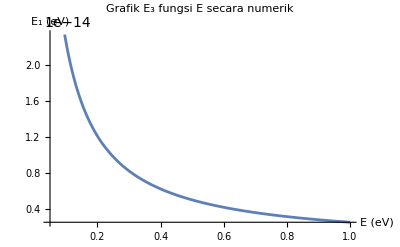

```mathematica
Plot[Abs[Subscript[NumE, 3]],{Energy, 0.5 10^9, 10^10},AxesLabel->{"E (eV)"," E_1 (eV)"},PlotLabel->"Grafik E_3 fungsi E secara numerik"]
```

```mathematica
Plot[Subscript[CompE, 1],{Energy, 0.5 10^16,2 10^17},AxesLabel->{"E (GeV)"," E_1 (GeV)"},PlotLabel->"Grafik E_1 fungsi E secara numerik"]
```

-Graphics-

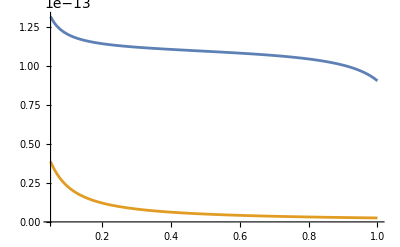

```mathematica
Plot[{Abs[Subscript[CompE, 1]],Abs[Subscript[NumE, 3]]},{Energy, 0.5 10^9, 10 10^9}]
```

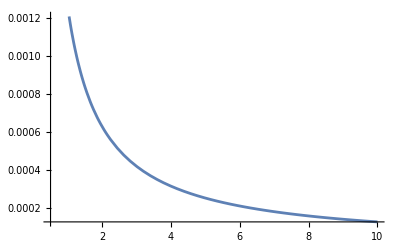

```mathematica
Plot[ReplaceAll[Abs[Subscript[CompE, 3]],Energy->Energy 10^9],{Energy, 0.5, 10}]
```

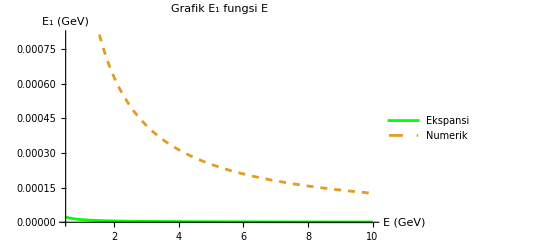

```mathematica
Plot[{ReplaceAll[Abs[Subscript[CompE, 1]],Energy->Energy 10^9],ReplaceAll[Abs[Subscript[NumE, 1]],Energy->Energy 10^9]},{Energy, 0.5, 10},PlotLegends->{"Ekspansi","Numerik"},AxesLabel->{"E (GeV)"," E_1 (GeV)"},PlotStyle->{Green, Dashed},PlotLabel->"Grafik E_1 fungsi E"]
```

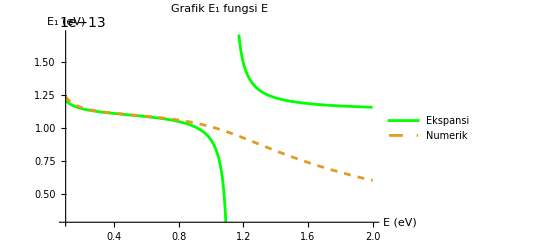

```mathematica
Plot[{Subscript[CompE, 1],Abs[Subscript[NumE, 2]]},{Energy,10^9,2 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.8}],AxesLabel->{"E (eV)"," E_1 (eV)"},PlotStyle->{Green, Dashed},PlotLabel->"Grafik E_1 fungsi E"]
```

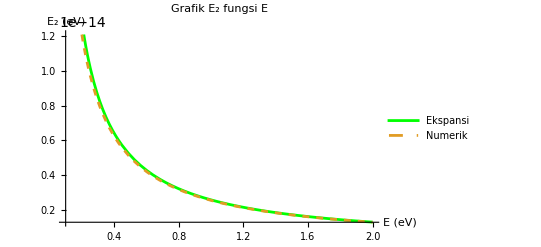

```mathematica
Plot[{Subscript[CompE, 2],Abs[Subscript[NumE, 3]]},{Energy, 10^9,2 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.8}],AxesLabel->{"E (eV)"," E_2 (eV)"},PlotStyle->{Green, Dashed},PlotLabel->"Grafik E_2 fungsi E"]
```

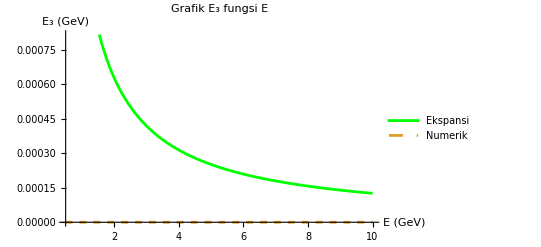

```mathematica
Plot[{ReplaceAll[Abs[Subscript[CompE, 3]],Energy->Energy 10^9],ReplaceAll[Abs[Subscript[NumE, 3]],Energy->Energy 10^9]},{Energy, 0.5, 10},PlotLegends->{"Ekspansi","Numerik"},AxesLabel->{"E (GeV)"," E_3 (GeV)"},PlotStyle->{Green, Dashed},PlotLabel->"Grafik E_3 fungsi E"]
```

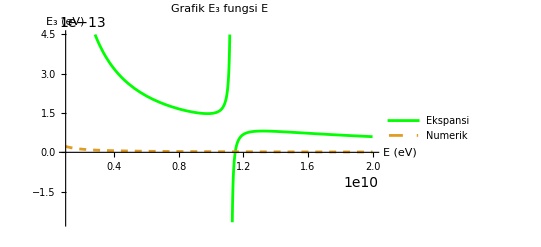

```mathematica
Plot[{Subscript[CompE, 3],Abs[Subscript[NumE, 3]]},{Energy, 10^9,2 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.8}],AxesLabel->{"E (eV)"," E_3 (eV)"},PlotStyle->{Green, Dashed},PlotLabel->"Grafik E_3 fungsi E"]
```

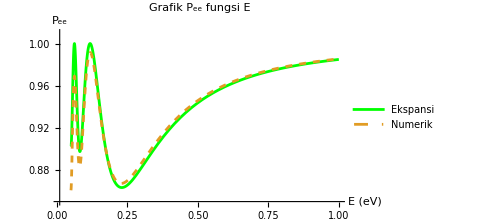

```mathematica
Plot[{Subscript[ExpP, ee],Subscript[NumP, ee]},{Energy,0.5 10^9,  10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.5}],AxesLabel->{"E (eV)","P_ee"},PlotStyle->{Green, Dashed},PlotRange->{{0.1 10^9,10^10},{0.85,1.01}},PlotLabel->"Grafik P_ee fungsi E"]
```

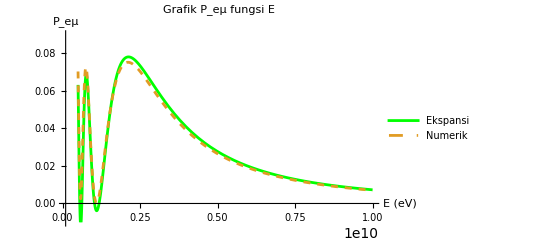

```mathematica
Plot[{Subscript[ExpP, eμ],Subscript[NumP, eμ]},{Energy, 0.5 10^9, 10 10^9},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.5}],AxesLabel->{"E (eV)","P_eμ"},PlotRange->{{0.1 10^9,10^10},{-0.01,0.09}},PlotStyle->{Green, Dashed},PlotLabel->"Grafik P_eμ fungsi E"]
```

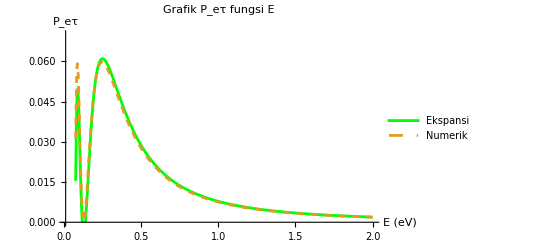

```mathematica
Plot[{Subscript[ExpP, eτ],Subscript[NumP, eτ]},{Energy, 0.75 10^9, 2 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.5}],AxesLabel->{"E (eV)","P_eτ"},PlotRange->{{0.1 10^9,2 10^10},{0,0.07}},PlotStyle->{Green, Dashed},PlotStyle->{Green, Dashed},PlotLabel->"Grafik P_eτ fungsi E"]
```

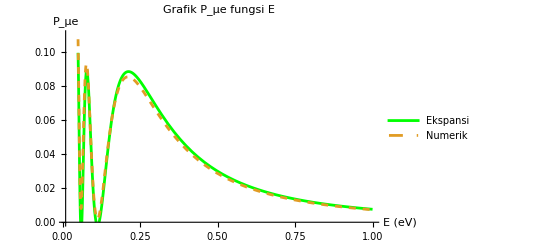

```mathematica
Plot[{Subscript[ExpP, μe],Subscript[NumP, μe]},{Energy,0.5 10^9, 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.5}],AxesLabel->{"E (eV)","P_μe"},PlotRange->{{0.1 10^9,10^10},{0,0.11}},PlotStyle->{Green, Dashed},PlotLabel->"Grafik P_μe fungsi E"]
```

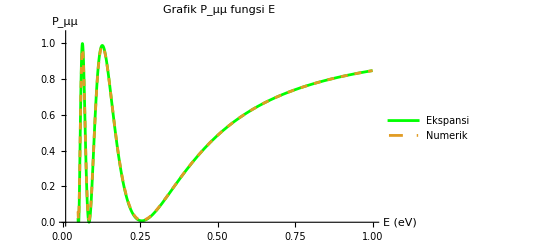

```mathematica
Plot[{Subscript[ExpP, μμ],Subscript[NumP, μμ]},{Energy,0.5 10^9, 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.5}],AxesLabel->{"E (eV)","P_μμ"},PlotRange->{{0.1 10^9,10^10},{0,1.05}},PlotStyle->{Green, Dashed},PlotLabel->"Grafik P_μμ fungsi E"]
```

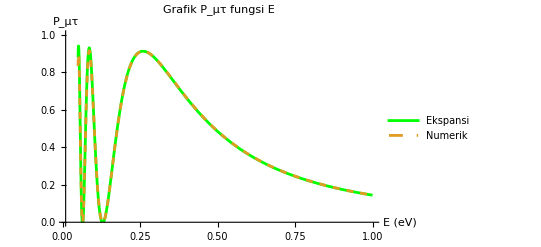

```mathematica
Plot[{Subscript[ExpP, μτ],Subscript[NumP, μτ]},{Energy, 0.5 10^9, 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.8}],AxesLabel->{"E (eV)","P_μτ"},PlotRange->{{0.1 10^9,10^10},{0,1}},PlotStyle->{Green, Dashed},PlotLabel->"Grafik P_μτ fungsi E"]
```

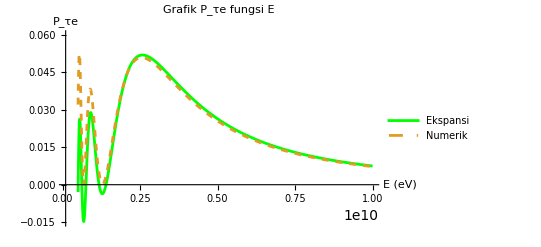

```mathematica
Plot[{Subscript[ExpP, τe],Subscript[NumP, τe]},{Energy, 0.5 10^9, 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.5}],AxesLabel->{"E (eV)","P_τe"},PlotRange->{{0.1 10^9,10^10},{-0.015,0.06}},PlotStyle->{Green, Dashed},PlotLabel->"Grafik P_τe fungsi E"]
```

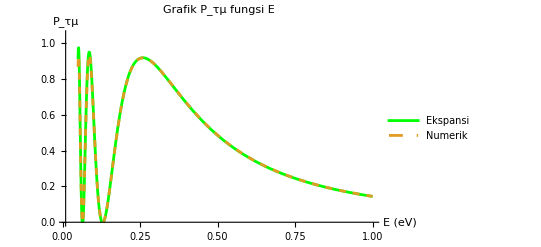

```mathematica
Plot[{Subscript[ExpP, τμ],Subscript[NumP, τμ]},{Energy,0.5 10^9, 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.5}],AxesLabel->{"E (eV)","P_τμ"},PlotRange->{{0.1 10^9,10^10},{0,1.05}},PlotStyle->{Green, Dashed},PlotLabel->"Grafik P_τμ fungsi E"]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

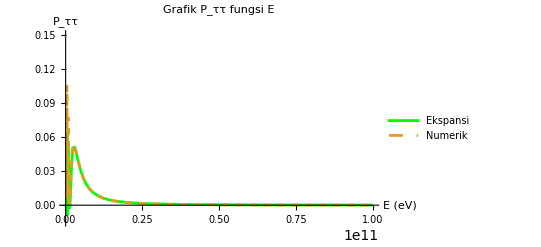

```mathematica
Plot[{ReplaceAll[Subscript[P, eμ vac],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2,A->2 Energy 7.56 10^-14 3 0.5/2.55 10^3, δ->0}],ReplaceAll[Limit[(Abs[NumS[[2,1]]])^2,A->0],{L->6.58 10^12, Subscript[m, 31]->2.514 10^-3, Subscript[s, 12]->Sin[33.66 Degree],Subscript[c, 12]->Cos[33.66 Degree],Subscript[s, 13]->Sin[8.54 Degree],Subscript[c, 13]->Cos[8.54 Degree], Subscript[s, 23]->Sin[49.1 Degree], Subscript[c, 23]->Cos[49.1 Degree], α->(7.41/2.514) 10^-2, δ->0}]},{Energy, 0.5 10^9, 10 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.5}],AxesLabel->{"E (eV)","P_ττ"},PlotRange->{{0.1 10^9,10^11},{-0.015,0.15}},PlotStyle->{Green, Dashed},PlotLabel->"Grafik P_ττ fungsi E"]
```

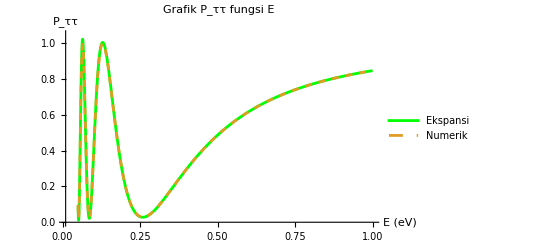

```mathematica
Plot[{Subscript[ExpP, ττ],Subscript[NumP, ττ]},{Energy, 0.5 10^9, 10^10},PlotLegends->Placed[{"Ekspansi","Numerik"},{0.8,0.5}],AxesLabel->{"E (eV)","P_ττ"},PlotRange->{{0.1 10^9,10^10},{0,1.05}},PlotStyle->{Green, Dashed},PlotLabel->"Grafik P_ττ fungsi E"]
```

```mathematica
Limit[NumS,A->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

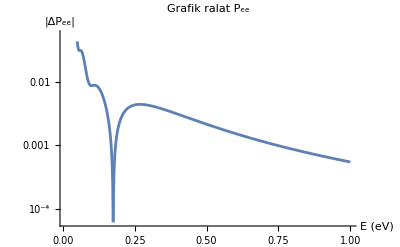

```mathematica
LogPlot[Abs[Subscript[ExpP, ee]-Subscript[NumP, ee]],{Energy, 0.5 10^9, 10 10^9},AxesLabel->{"E (eV)","|ΔP_ee|"},PlotRange->{{0.1 10^9,10^10},{0,0.055}},PlotLabel->"Grafik ralat P_ee"]
```

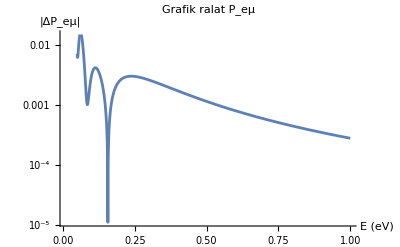

```mathematica
LogPlot[Abs[Subscript[ExpP, eμ]-Subscript[NumP, eμ]],{Energy, 0.5 10^9, 10 10^9},AxesLabel->{"E (eV)","|ΔP_eμ|"},PlotRange->{{0.1 10^9,10^10},{0,0.015}},PlotLabel->"Grafik ralat P_eμ"]
```

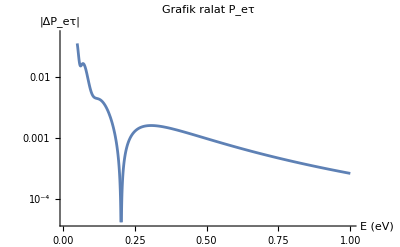

```mathematica
LogPlot[Abs[Subscript[ExpP, eτ]-Subscript[NumP, eτ]],{Energy, 0.5 10^9, 10 10^9},AxesLabel->{"E (eV)","|ΔP_eτ|"},PlotRange->{{0.1 10^9,10^10},{0,0.05}},PlotLabel->"Grafik ralat P_eτ"]
```

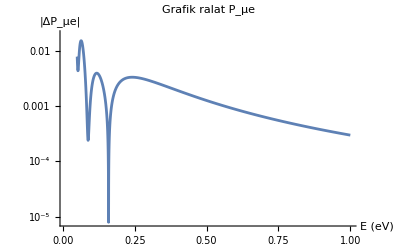

```mathematica
LogPlot[Abs[Subscript[ExpP, μe]-Subscript[NumP, μe]],{Energy, 0.5 10^9, 10 10^9},AxesLabel->{"E (eV)","|ΔP_μe|"},PlotRange->{{0.1 10^9,10^10},{0,0.02}},PlotLabel->"Grafik ralat P_μe"]
```

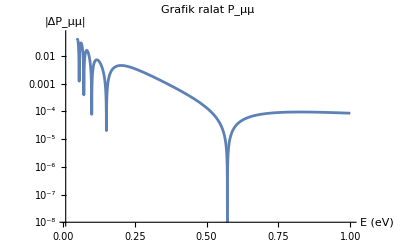

```mathematica
LogPlot[Abs[Subscript[ExpP, μμ]-Subscript[NumP, μμ]],{Energy, 0.5 10^9, 10 10^9},AxesLabel->{"E (eV)","|ΔP_μμ|"},PlotRange->{{0.1 10^9,10^10},{10^-8,0.06}},PlotLabel->"Grafik ralat P_μμ"]
```

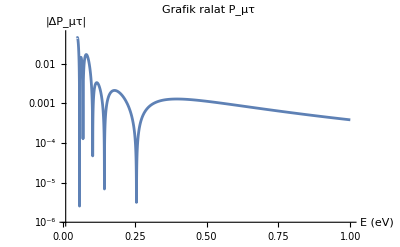

```mathematica
LogPlot[Abs[Subscript[ExpP, μτ]-Subscript[NumP, μτ]],{Energy, 0.5 10^9, 10 10^9},AxesLabel->{"E (eV)","|ΔP_μτ|"},PlotRange->{{0.1 10^9,10^10},{10^-6,0.055}},PlotLabel->"Grafik ralat P_μτ"]
```

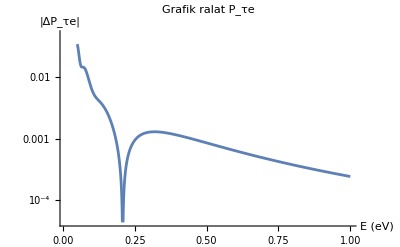

```mathematica
LogPlot[Abs[Subscript[ExpP, τe]-Subscript[NumP, τe]],{Energy, 0.5 10^9, 10 10^9},AxesLabel->{"E (eV)","|ΔP_τe|"},PlotRange->{{0.1 10^9,10^10},{0,0.05}},PlotLabel->"Grafik ralat P_τe"]
```

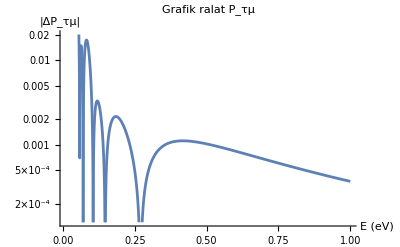

```mathematica
LogPlot[Abs[Subscript[ExpP, τμ]-Subscript[NumP, τμ]],{Energy, 0.5 10^9, 10 10^9},AxesLabel->{"E (eV)","|ΔP_τμ|"},PlotRange->{{0.1 10^9,10^10},{0,0.02}},PlotLabel->"Grafik ralat P_τμ"]
```

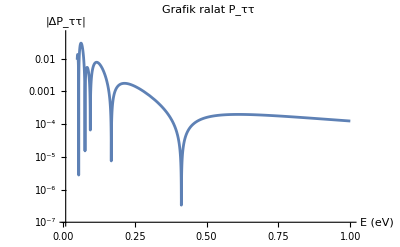

```mathematica
LogPlot[Abs[Subscript[ExpP, ττ]-Subscript[NumP, ττ]],{Energy, 0.5 10^9, 10 10^9},AxesLabel->{"E (eV)","|ΔP_ττ|"},PlotRange->{{0.1 10^9,10^10},{10^-7,0.055}},PlotLabel->"Grafik ralat P_ττ"]
```

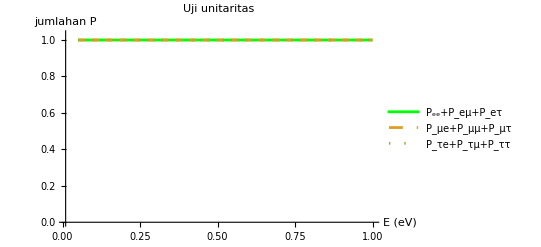

```mathematica
Plot[{Subscript[ExpP, ee]+Subscript[ExpP, eμ]+Subscript[ExpP, eτ],Subscript[ExpP, μe]+Subscript[ExpP, μμ]+Subscript[ExpP, μτ],Subscript[ExpP, τe]+Subscript[ExpP, τμ]+Subscript[ExpP, ττ]},{Energy, 0.5 10^9, 10 10^9},PlotLegends->Placed[{"P_ee+P_eμ+P_eτ","P_μe+P_μμ+P_μτ","P_τe+P_τμ+P_ττ"},{0.8,0.5}],AxesLabel->{"E (eV)","jumlahan P"},PlotRange->{{0.1 10^9,10^10},{0,1.03}},PlotStyle->{Green, Dashed,Dotted},PlotLabel->"Uji unitaritas"]
```

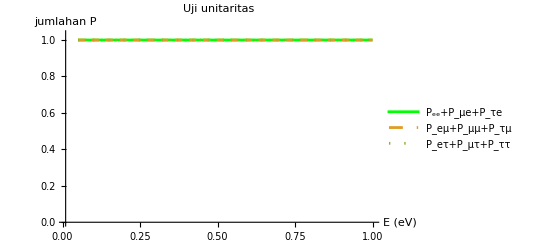

```mathematica
Plot[{Subscript[ExpP, ee]+Subscript[ExpP, μe]+Subscript[ExpP, τe],Subscript[ExpP, eμ]+Subscript[ExpP, μμ]+Subscript[ExpP, τμ],Subscript[ExpP, eτ]+Subscript[ExpP, μτ]+Subscript[ExpP, ττ]},{Energy, 0.5 10^9, 10 10^9},PlotLegends->Placed[{"P_ee+P_μe+P_τe","P_eμ+P_μμ+P_τμ","P_eτ+P_μτ+P_ττ"},{0.8,0.5}],AxesLabel->{"E (eV)","jumlahan P"},PlotRange->{{0.1 10^9,10^10},{0,1.03}},PlotStyle->{Green, Dashed,Dotted},PlotLabel->"Uji unitaritas"]
```